### initializing notebook

```mathematica
Needs["Carlos`"]
Needs["Quantum`"]
Needs["SpinChain`"]
Needs["TheoreticalRMT`"]
Needs["Quantum2`"]
pathdata=NotebookDirectory[]<>"data/";
Reshqubit=KroneckerProduct[IdentityMatrix[2],KroneckerProduct[{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}},IdentityMatrix[2]]];Reshqutrit=KroneckerProduct[IdentityMatrix[3],KroneckerProduct[{{1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0},{0,1,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,0},{0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,1}},IdentityMatrix[3]]];
listvalid=Import[pathdata<>"list_valid_two_qubits.mat"]//First;
vectorr[state_]:=1/4Table[Tr[state.KroneckerProduct[PauliMatrix[i],PauliMatrix[j]]],{i,0,3},{j,0,3}];
Principalminors[mat_,r_]:=DeleteDuplicates[Flatten[Diagonal[Map[Reverse,Minors[mat, #], {0, 1}]] & /@ r]];
reduceeigenvalues[list_]:=Reduce[And @@Thread[list≥0],Reals];
```

Import::nffil: File /home/david/Escritorio/Maestria/Proyectos/JoseAlfredo/component-erasing-maps/mathematica/data/list_valid_two_qubits.mat not found during Import.

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

```mathematica
$memLimit=8*10^9;
$Pre=Function[expr,MemoryConstrained[expr,$memLimit,Print["memory limit exceded"]],{HoldAll}];
```

## Cosas a organizar, tal vez ya no son importantes

```mathematica
ch1={{1,0,0,0},{0,Subscript[λ, 1],0,0},{0,0,Subscript[λ, 2],0},{0,0,0,Subscript[λ, 3]}};
ch1//MatrixForm
ch2={{1,0,0,0},{0,Subscript[κ, 1],0,0},{0,0,Subscript[κ, 2],0},{0,0,0,Subscript[κ, 3]}};ch2//MatrixForm
```

(1 | 0 | 0 | 0
0 | λ_1 | 0 | 0
0 | 0 | λ_2 | 0
0 | 0 | 0 | λ_3)

(1 | 0 | 0 | 0
0 | κ_1 | 0 | 0
0 | 0 | κ_2 | 0
0 | 0 | 0 | κ_3)

```mathematica
mat=Reshqubit.KroneckerProduct[ch1,ch2].Reshqubit;mat//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | κ_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | λ_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | κ_1 λ_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | κ_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | κ_3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | κ_2 λ_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_3 λ_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_1 λ_2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ_3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_1 λ_3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_2 λ_2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_3 λ_2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_2 λ_3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_3 λ_3)

```mathematica
ChoiJamiStateFromPauliProductBasis[mat]//Eigenvalues
```

{1/16 (1+κ_1-κ_2-κ_3) (1+λ_1-λ_2-λ_3),-1/16 (-1+κ_1+κ_2-κ_3) (1+λ_1-λ_2-λ_3),-1/16 (-1+κ_1-κ_2+κ_3) (1+λ_1-λ_2-λ_3),1/16 (1+κ_1+κ_2+κ_3) (1+λ_1-λ_2-λ_3),-1/16 (1+κ_1-κ_2-κ_3) (-1+λ_1+λ_2-λ_3),1/16 (-1+κ_1+κ_2-κ_3) (-1+λ_1+λ_2-λ_3),1/16 (-1+κ_1-κ_2+κ_3) (-1+λ_1+λ_2-λ_3),-1/16 (1+κ_1+κ_2+κ_3) (-1+λ_1+λ_2-λ_3),-1/16 (1+κ_1-κ_2-κ_3) (-1+λ_1-λ_2+λ_3),1/16 (-1+κ_1+κ_2-κ_3) (-1+λ_1-λ_2+λ_3),1/16 (-1+κ_1-κ_2+κ_3) (-1+λ_1-λ_2+λ_3),-1/16 (1+κ_1+κ_2+κ_3) (-1+λ_1-λ_2+λ_3),1/16 (1+κ_1-κ_2-κ_3) (1+λ_1+λ_2+λ_3),-1/16 (-1+κ_1+κ_2-κ_3) (1+λ_1+λ_2+λ_3),-1/16 (-1+κ_1-κ_2+κ_3) (1+λ_1+λ_2+λ_3),1/16 (1+κ_1+κ_2+κ_3) (1+λ_1+λ_2+λ_3)}

```mathematica
ρ1=IdentityMatrix[2]/2+1/2Sum[Subscript[r, i] PauliMatrix[i],{i,1,3}];
```

```mathematica
ρext=KroneckerProduct[IdentityMatrix[2]/2,ρ1];
```

```mathematica
Table[Tr[ρext.KroneckerProduct[PauliMatrix[i],PauliMatrix[j]]],{i,0,3},{j,0,3}]
```

{{1,1/2 (r_1-ⅈ r_2)+1/2 (r_1+ⅈ r_2),1/2 ⅈ (r_1-ⅈ r_2)-1/2 ⅈ (r_1+ⅈ r_2),r_3},{0,0,0,0},{0,0,0,0},{1/2 (-1/2-r_3/2)+1/2 (1/2-r_3/2)+1/2 (-1/2+r_3/2)+1/2 (1/2+r_3/2),1/4 (-r_1-ⅈ r_2)+1/4 (r_1-ⅈ r_2)+1/4 (-r_1+ⅈ r_2)+1/4 (r_1+ⅈ r_2),0,1/2 (-1/2-r_3/2)+1/2 (1/2-r_3/2)+1/2 (-1/2+r_3/2)+1/2 (1/2+r_3/2)}}

```mathematica
rext=Flatten[Table[Tr[ρext.KroneckerProduct[PauliMatrix[i],PauliMatrix[j]]],{i,0,3},{j,0,3}]]
```

{1,1/2 (r_1-ⅈ r_2)+1/2 (r_1+ⅈ r_2),1/2 ⅈ (r_1-ⅈ r_2)-1/2 ⅈ (r_1+ⅈ r_2),r_3,0,0,0,0,0,0,0,0,1/2 (-1/2-r_3/2)+1/2 (1/2-r_3/2)+1/2 (-1/2+r_3/2)+1/2 (1/2+r_3/2),1/4 (-r_1-ⅈ r_2)+1/4 (r_1-ⅈ r_2)+1/4 (-r_1+ⅈ r_2)+1/4 (r_1+ⅈ r_2),0,1/2 (-1/2-r_3/2)+1/2 (1/2-r_3/2)+1/2 (-1/2+r_3/2)+1/2 (1/2+r_3/2)}

```mathematica
Sum[Partition[rext,4][[i,j]]*KroneckerProduct[PauliMatrix[i-1],PauliMatrix[j-1]],{i,1,4},{j,1,4}]
```

{{1+r_3,-ⅈ (1/2 ⅈ (r_1-ⅈ r_2)-1/2 ⅈ (r_1+ⅈ r_2))+1/4 (-r_1-ⅈ r_2)+3/4 (r_1-ⅈ r_2)+1/4 (-r_1+ⅈ r_2)+3/4 (r_1+ⅈ r_2),0,0},{ⅈ (1/2 ⅈ (r_1-ⅈ r_2)-1/2 ⅈ (r_1+ⅈ r_2))+1/4 (-r_1-ⅈ r_2)+3/4 (r_1-ⅈ r_2)+1/4 (-r_1+ⅈ r_2)+3/4 (r_1+ⅈ r_2),1-r_3,0,0},{0,0,1+r_3,-ⅈ (1/2 ⅈ (r_1-ⅈ r_2)-1/2 ⅈ (r_1+ⅈ r_2))+1/4 (-r_1-ⅈ r_2)+3/4 (r_1-ⅈ r_2)+1/4 (-r_1+ⅈ r_2)+3/4 (r_1+ⅈ r_2)},{0,0,ⅈ (1/2 ⅈ (r_1-ⅈ r_2)-1/2 ⅈ (r_1+ⅈ r_2))+1/4 (-r_1-ⅈ r_2)+3/4 (r_1-ⅈ r_2)+1/4 (-r_1+ⅈ r_2)+3/4 (r_1+ⅈ r_2),1-r_3}}

```mathematica
rout=Partition[mat.rext,4];
```

```mathematica
rout[[2,3]]
```

0

```mathematica
ρout=Sum[rout[[i,j]]*KroneckerProduct[PauliMatrix[i-1],PauliMatrix[j-1]],{i,1,4},{j,1,4}];
```

```mathematica
KroneckerProduct[PauliMatrix[2-1],PauliMatrix[3-1]]//MatrixForm
```

(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0)

```mathematica
ρout//MatrixForm
```

(1+r_3 κ_1+(1/2 (-1/2-r_3/2)+1/2 (1/2-r_3/2)+1/2 (-1/2+r_3/2)+1/2 (1/2+r_3/2)) κ_2+(1/2 (-1/2-r_3/2)+1/2 (1/2-r_3/2)+1/2 (-1/2+r_3/2)+1/2 (1/2+r_3/2)) κ_3 | -ⅈ (1/2 ⅈ (r_1-ⅈ r_2)-1/2 ⅈ (r_1+ⅈ r_2))+(1/2 (r_1-ⅈ r_2)+1/2 (r_1+ⅈ r_2)) κ_1+(1/4 (-r_1-ⅈ r_2)+1/4 (r_1-ⅈ r_2)+1/4 (-r_1+ⅈ r_2)+1/4 (r_1+ⅈ r_2)) κ_3 | 0 | 0
ⅈ (1/2 ⅈ (r_1-ⅈ r_2)-1/2 ⅈ (r_1+ⅈ r_2))+(1/2 (r_1-ⅈ r_2)+1/2 (r_1+ⅈ r_2)) κ_1+(1/4 (-r_1-ⅈ r_2)+1/4 (r_1-ⅈ r_2)+1/4 (-r_1+ⅈ r_2)+1/4 (r_1+ⅈ r_2)) κ_3 | 1-r_3 κ_1+(1/2 (-1/2-r_3/2)+1/2 (1/2-r_3/2)+1/2 (-1/2+r_3/2)+1/2 (1/2+r_3/2)) κ_2-(1/2 (-1/2-r_3/2)+1/2 (1/2-r_3/2)+1/2 (-1/2+r_3/2)+1/2 (1/2+r_3/2)) κ_3 | 0 | 0
0 | 0 | 1+r_3 κ_1-(1/2 (-1/2-r_3/2)+1/2 (1/2-r_3/2)+1/2 (-1/2+r_3/2)+1/2 (1/2+r_3/2)) κ_2-(1/2 (-1/2-r_3/2)+1/2 (1/2-r_3/2)+1/2 (-1/2+r_3/2)+1/2 (1/2+r_3/2)) κ_3 | -ⅈ (1/2 ⅈ (r_1-ⅈ r_2)-1/2 ⅈ (r_1+ⅈ r_2))+(1/2 (r_1-ⅈ r_2)+1/2 (r_1+ⅈ r_2)) κ_1-(1/4 (-r_1-ⅈ r_2)+1/4 (r_1-ⅈ r_2)+1/4 (-r_1+ⅈ r_2)+1/4 (r_1+ⅈ r_2)) κ_3
0 | 0 | ⅈ (1/2 ⅈ (r_1-ⅈ r_2)-1/2 ⅈ (r_1+ⅈ r_2))+(1/2 (r_1-ⅈ r_2)+1/2 (r_1+ⅈ r_2)) κ_1-(1/4 (-r_1-ⅈ r_2)+1/4 (r_1-ⅈ r_2)+1/4 (-r_1+ⅈ r_2)+1/4 (r_1+ⅈ r_2)) κ_3 | 1-r_3 κ_1-(1/2 (-1/2-r_3/2)+1/2 (1/2-r_3/2)+1/2 (-1/2+r_3/2)+1/2 (1/2+r_3/2)) κ_2+(1/2 (-1/2-r_3/2)+1/2 (1/2-r_3/2)+1/2 (-1/2+r_3/2)+1/2 (1/2+r_3/2)) κ_3)

```mathematica
PartialTrace[ρout,1]
```

{{2+2 r_3 κ_1,-2 ⅈ (1/2 ⅈ (r_1-ⅈ r_2)-1/2 ⅈ (r_1+ⅈ r_2))+2 (1/2 (r_1-ⅈ r_2)+1/2 (r_1+ⅈ r_2)) κ_1},{2 ⅈ (1/2 ⅈ (r_1-ⅈ r_2)-1/2 ⅈ (r_1+ⅈ r_2))+2 (1/2 (r_1-ⅈ r_2)+1/2 (r_1+ⅈ r_2)) κ_1,2-2 r_3 κ_1}}

```mathematica
mat=Reshqubit.KroneckerProduct[ch1,ch2].Reshqubit;mat//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | κ_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | λ_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | κ_1 λ_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | κ_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | κ_3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | κ_2 λ_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_3 λ_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_1 λ_2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ_3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_1 λ_3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_2 λ_2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_3 λ_2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_2 λ_3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_3 λ_3)

```mathematica
corrs=Diagonal[mat];
```

```mathematica
corrs
```

{1,κ_1,λ_1,κ_1 λ_1,κ_2,κ_3,κ_2 λ_1,κ_3 λ_1,λ_2,κ_1 λ_2,λ_3,κ_1 λ_3,κ_2 λ_2,κ_3 λ_2,κ_2 λ_3,κ_3 λ_3}

## Checando orden

```mathematica
ch1={{1,0,0,0},{0,Subscript[λ, 1],0,0},{0,0,Subscript[λ, 2],0},{0,0,0,Subscript[λ, 3]}}//FromPauliToUnit;
ch1//MatrixForm
ch2={{1,0,0,0},{0,Subscript[κ, 1],0,0},{0,0,Subscript[κ, 2],0},{0,0,0,Subscript[κ, 3]}}//FromPauliToUnit;ch2//MatrixForm
```

(1/2+λ_3/2 | 0 | 0 | 1/2-λ_3/2
0 | λ_1/2+λ_2/2 | λ_1/2-λ_2/2 | 0
0 | λ_1/2-λ_2/2 | λ_1/2+λ_2/2 | 0
1/2-λ_3/2 | 0 | 0 | 1/2+λ_3/2)

(1/2+κ_3/2 | 0 | 0 | 1/2-κ_3/2
0 | κ_1/2+κ_2/2 | κ_1/2-κ_2/2 | 0
0 | κ_1/2-κ_2/2 | κ_1/2+κ_2/2 | 0
1/2-κ_3/2 | 0 | 0 | 1/2+κ_3/2)

```mathematica
matcontrol=Reshqubit.KroneckerProduct[ch1,ch2].Reshqubit;
```

```mathematica
ρ1=IdentityMatrix[2]/2+1/2Sum[Subscript[r, i] PauliMatrix[i],{i,1,3}];
```

```mathematica
ρext=KroneckerProduct[IdentityMatrix[2]/2,ρ1];
```

```mathematica
ρin=Sum[Subscript[r, i-1,j-1]*KroneckerProduct[PauliMatrix[i-1],PauliMatrix[j-1]],{i,1,4},{j,1,4}];
```

```mathematica
ρout=Partition[matcontrol.Flatten[ρin]//Expand,4];
```

```mathematica
rout=1/4Flatten[Table[Tr[ρout.KroneckerProduct[PauliMatrix[i],PauliMatrix[j]]],{i,0,3},{j,0,3}]]//FullSimplify//TableForm
```

r_(0,0)
κ_1 r_(0,1)
κ_2 r_(0,2)
κ_3 r_(0,3)
λ_1 r_(1,0)
κ_1 λ_1 r_(1,1)
κ_2 λ_1 r_(1,2)
κ_3 λ_1 r_(1,3)
λ_2 r_(2,0)
κ_1 λ_2 r_(2,1)
κ_2 λ_2 r_(2,2)
κ_3 λ_2 r_(2,3)
λ_3 r_(3,0)
κ_1 λ_3 r_(3,1)
κ_2 λ_3 r_(3,2)
κ_3 λ_3 r_(3,3)

```mathematica
mat=KroneckerProduct[ch1,ch2];mat//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | κ_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | κ_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | κ_3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | λ_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | κ_1 λ_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | κ_2 λ_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_3 λ_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_1 λ_2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_2 λ_2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_3 λ_2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | λ_3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_1 λ_3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_2 λ_3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ_3 λ_3)

## Checanco CP

```mathematica
particles=3;U1=CUEMember[2^particles];U2=CUEMember[2^particles];channel[ρ_]:=0.4 U1.ρ.Dagger[U1]+0.6U2.ρ.Dagger[U2];
```

```mathematica
channprod=QuantumMapInProductPauliBasis[channel,particles];
```

```mathematica
choi=ChoiJamiStateFromPauliProductBasis[channprod];
```

```mathematica
choi//Tr
```

1.

```mathematica
choi//PositiveSemidefiniteMatrixQ
```

True

```mathematica
choi//HermitianMatrixQ
```

True

```mathematica
choi//MatrixRank
```

2

## Jugando con canales diagonales

Borrando una correlacion

```mathematica
particles=2;diagchan=DiagonalMatrix[Table[α[IntegerDigits[i-1,4,particles]],{i,1,2^(2particles)}]];
$Assumptions=Element[diagchan,Reals];α[IntegerDigits[1-1,4,particles]]=1;
```

```mathematica
eig=ChoiJamiStateFromPauliProductBasis[diagchan]//Eigenvalues;
```

```mathematica
Reduce[And@@Thread[eig≥0],Reals]
```

(α[{1}]==-1&&-1≤α[{2}]≤1&&α[{3}]==-α[{2}])||(-1<α[{1}]≤0&&((α[{2}]==-1&&α[{3}]==-α[{1}])||(-1<α[{2}]≤α[{1}]&&-1-α[{1}]-α[{2}]≤α[{3}]≤1-α[{1}]+α[{2}])||(α[{1}]<α[{2}]≤-α[{1}]&&-1-α[{1}]-α[{2}]≤α[{3}]≤1+α[{1}]-α[{2}])||(-α[{1}]<α[{2}]<1&&-1+α[{1}]+α[{2}]≤α[{3}]≤1+α[{1}]-α[{2}])||(α[{2}]==1&&α[{3}]==α[{1}])))||(0<α[{1}]<1&&((α[{2}]==-1&&α[{3}]==-α[{1}])||(-1<α[{2}]≤-α[{1}]&&-1-α[{1}]-α[{2}]≤α[{3}]≤1-α[{1}]+α[{2}])||(-α[{1}]<α[{2}]≤α[{1}]&&-1+α[{1}]+α[{2}]≤α[{3}]≤1-α[{1}]+α[{2}])||(α[{1}]<α[{2}]<1&&-1+α[{1}]+α[{2}]≤α[{3}]≤1+α[{1}]-α[{2}])||(α[{2}]==1&&α[{3}]==α[{1}])))||(α[{1}]==1&&((α[{2}]==-1&&α[{3}]==-1)||(-1<α[{2}]≤1&&α[{3}]==α[{2}])))

Ejemplos de JA

```mathematica
{1,1,0,0,1,0,0,0,0,0,1,0,0,0,0,0}//DiagonalMatrix//ChoiJamiStateFromPauliProductBasis//PositiveSemidefiniteMatrixQ
```

False

```mathematica
{1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0}//DiagonalMatrix//ChoiJamiStateFromPauliProductBasis//PositiveSemidefiniteMatrixQ
```

True

```mathematica
Partition[{1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0},4]//MatrixForm
```

(1 | 1 | 0 | 0
1 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
permsone=Select[PermutationMatrices[4],#[[1,1]]==1&];
```

```mathematica
perms//Length
```

6

```mathematica
PositiveSemidefiniteMatrixQ/@ChoiJamiStateFromPauliProductBasis/@perms
```

{True,False,False,True,True,False}

```mathematica
randperm:=permsone[[RandomInteger[{1,Length[permsone]}]]]
```

```mathematica
randperm
```

{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}}

## Valid diagonal channels and equivalence classes two qubits

```mathematica
(*listvalid=Select[Tuples[{1,0},16],PositiveSemidefiniteMatrixQ[ChoiJamiStateFromPauliProductBasis[DiagonalMatrix[#]]]==True&]*)
listvalid=Import[pathdata<>"list_valid_two_qubits.mat"]//First;listvalid=Select[listvalid,#[[1]]==1&];count=Table[{Count[listvalid[[i]],1],listvalid[[i]]},{i,1,Length[listvalid]}];ones=DeleteDuplicates[count[[All,1]]];
(*Export[pathdata<>"list_valid_two_qubits.mat",listvalid]*)
perms=PermutationMatrices[4];permsone=Select[perms,#[[1,1]]==1&];
byones=Table[Select[count,#[[1]]==ones[[i]]&],{i,Length[ones]}];
```

Import::nffil: File /home/david/Escritorio/Maestria/Proyectos/JoseAlfredo/component-erasing-maps/mathematica/data/list_valid_two_qubits.mat not found during Import.

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

First::argt: First called with 0 arguments; 1 or 2 arguments are expected.

```mathematica
Length/@byones
```

{1,15,35,15,1}

### Matrices with 8 ones

```mathematica
m=2;len=byones[[m]]//Length
15
preclasses=Table[mat=Partition[byones[[m]][[k]][[2]],4];Sort[DeleteDuplicates[Flatten[{Flatten[Table[permsone[[i]].mat.Transpose[permsone[[j]]],{i,1,6},{j,1,6}],1],Flatten[Table[permsone[[i]].Transpose[mat].Transpose[permsone[[j]]],{i,1,6},{j,1,6}],1]},1]]],{k,1,len}];
Length/@preclasses
{6,6,6,6,9,9,9,6,9,9,9,6,9,9,9}
classes=DeleteDuplicates[preclasses];classes//Length
1
Length/@classes//Total
15
class81=classes[[1]][[1]];
class82=classes[[2]][[1]];
```

Part::partw: Part 2 of {} does not exist.

2

15

Part::partw: Part 2 of {} does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification 2⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

{72,72}

{6,6,6,6,9,9,9,6,9,9,9,6,9,9,9}

1

1

72

15

Part::partw: Part 2 of {{{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}.Part[].{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}},{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}.Part[].{{1,0,0,0},{0,0,0,1},{0,1,0,0},{0,0,1,0}},{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}.Part[].{{1,0,0,0},{0,0,1,0},{0,0,0,1},{0,1,0,0}},«6»,{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}.Transpose[Part[]].{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}},«62»}} does not exist.

```mathematica
MatrixPlot[#,ColorFunction->"Monochrome",FrameTicks->None,Frame->True,FrameStyle->Thick]&/@classes[[1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot[#,ColorFunction->"Monochrome",FrameTicks->None,Frame->True,FrameStyle->Thick]&/@classes[[2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Matrices with 4 ones

```mathematica
m=3;len=byones[[m]]//Length
35
preclasses=Table[mat=Partition[byones[[m]][[k]][[2]],4];Sort[DeleteDuplicates[Flatten[{Flatten[Table[permsone[[i]].mat.Transpose[permsone[[j]]],{i,1,6},{j,1,6}],1],Flatten[Table[permsone[[i]].Transpose[mat].Transpose[permsone[[j]]],{i,1,6},{j,1,6}],1]},1]]],{k,1,len}];
Length/@preclasses
{2,9,18,9,18,9,18,9,18,9,18,9,18,9,18,9,18,9,18,2,18,18,18,18,18,6,6,18,6,18,6,18,6,6,18}
classes=DeleteDuplicates[preclasses];classes//Length
4
Length/@classes//Total
35
class41=classes[[1]][[1]];
class42=classes[[2]][[1]];
class43=classes[[3]][[1]];
class44=classes[[4]][[1]];
```

Part::partw: Part 3 of {} does not exist.

2

35

Part::partw: Part 3 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification 3⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

{72,72}

{2,9,18,9,18,9,18,9,18,9,18,9,18,9,18,9,18,9,18,2,18,18,18,18,18,6,6,18,6,18,6,18,6,6,18}

1

4

72

35

Part::partw: Part 2 of {{{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}.Part[].{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}},{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}.Part[].{{1,0,0,0},{0,0,0,1},{0,1,0,0},{0,0,1,0}},{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}.Part[].{{1,0,0,0},{0,0,1,0},{0,0,0,1},{0,1,0,0}},«6»,{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}.Transpose[Part[]].{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}},«62»}} does not exist.

Part::partw: Part 3 of {{{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}.Part[].{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}},{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}.Part[].{{1,0,0,0},{0,0,0,1},{0,1,0,0},{0,0,1,0}},{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}.Part[].{{1,0,0,0},{0,0,1,0},{0,0,0,1},{0,1,0,0}},«6»,{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}.Transpose[Part[]].{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}},«62»}} does not exist.

Part::partw: Part 4 of {{{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}.Part[].{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}},{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}.Part[].{{1,0,0,0},{0,0,0,1},{0,1,0,0},{0,0,1,0}},{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}.Part[].{{1,0,0,0},{0,0,1,0},{0,0,0,1},{0,1,0,0}},«6»,{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}.Transpose[Part[]].{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}},«62»}} does not exist.

```mathematica
MatrixPlot[#,ColorFunction->"Monochrome",FrameTicks->None,Frame->True,FrameStyle->Thick]&/@classes[[1]]
```

{-Graphics-,-Graphics-}

```mathematica
MatrixPlot[#,ColorFunction->"Monochrome",FrameTicks->None,Frame->True,FrameStyle->Thick]&/@classes[[2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot[#,ColorFunction->"Monochrome",FrameTicks->None,Frame->True,FrameStyle->Thick]&/@classes[[3]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot[#,ColorFunction->"Monochrome",FrameTicks->None,Frame->True,FrameStyle->Thick]&/@classes[[4]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Matrices with 2 ones

```mathematica
m=4;len=byones[[m]]//Length
15
preclasses=Table[mat=Partition[byones[[m]][[k]][[2]],4];Sort[DeleteDuplicates[Flatten[{Flatten[Table[permsone[[i]].mat.Transpose[permsone[[j]]],{i,1,6},{j,1,6}],1],Flatten[Table[permsone[[i]].Transpose[mat].Transpose[permsone[[j]]],{i,1,6},{j,1,6}],1]},1]]],{k,1,len}];
Length/@preclasses
{6,6,6,6,9,9,9,6,9,9,9,6,9,9,9}
classes=DeleteDuplicates[preclasses];classes//Length
2
Length/@classes//Total
15
class21=classes[[1]][[1]];
class22=classes[[2]][[1]];
```

Part::partw: Part 4 of {} does not exist.

2

15

Part::partw: Part 4 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 4 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification 4⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

{72,72}

{6,6,6,6,9,9,9,6,9,9,9,6,9,9,9}

1

2

72

15

Part::partw: Part 2 of {{{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}.Part[].{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}},{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}.Part[].{{1,0,0,0},{0,0,0,1},{0,1,0,0},{0,0,1,0}},{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}.Part[].{{1,0,0,0},{0,0,1,0},{0,0,0,1},{0,1,0,0}},«6»,{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}.Transpose[Part[]].{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}},«62»}} does not exist.

```mathematica
MatrixPlot[#,ColorFunction->"Monochrome",FrameTicks->None,Frame->True,FrameStyle->Thick]&/@classes[[1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot[#,ColorFunction->"Monochrome",FrameTicks->None,Frame->True,FrameStyle->Thick]&/@classes[[2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Valid diagonal channels and equivalence classes two qubits --including 0,0

```mathematica
listvalid=Import[pathdata<>"list_valid_two_qubits.mat"]//First;
```

```mathematica
Select[listvalid,#[[1]]==0&]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

## Canal en L y trazas parciales

```mathematica
trazas[ρ_]:=KroneckerProduct[PartialTrace[ρ,2],PartialTrace[ρ,1]]
```

```mathematica
trazas[KroneckerProduct[{1,0},{1,0}]//Flatten//Proyector]
```

{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
vectorr[state_]:=1/4Table[Tr[state.KroneckerProduct[PauliMatrix[i],PauliMatrix[j]]],{i,0,3},{j,0,3}]
```

```mathematica
vectorr[KroneckerProduct[{1,0},{1,0}]//Flatten//Proyector]//Flatten
```

{1/4,0,0,1/4,0,0,0,0,0,0,0,0,1/4,0,0,1/4}

```mathematica
vectorr2[state_]:=1/2Table[Tr[state.PauliMatrix[i]],{i,0,3}]
```

```mathematica
vectorr2[{1,0}//Proyector]
```

{1/2,0,0,1/2}

```mathematica
QuantumMapInProductPauliBasis[trazas,2]//ChoiJamiStateFromPauliProductBasis//Eigenvalues
```

{1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4}

```mathematica
And@@Thread[({{1,a,a,a},{a,0,0,0},{a,0,0,0},{a,0,0,0}}//Flatten//DiagonalMatrix//ChoiJamiStateFromPauliProductBasis//Eigenvalues//FullSimplify)≥0]//Reduce
```

-1/6≤a≤1/2

```mathematica
Proyector[KroneckerProduct[{1,1}/Sqrt[2],{1,1}/Sqrt[2]]//Flatten]//vectorr//Flatten
```

{1/4,1/4,0,0,1/4,1/4,0,0,0,0,0,0,0,0,0,0}

```mathematica
final=({{1,a,a,a},{a,0,0,0},{a,0,0,0},{a,0,0,0}}//Flatten//DiagonalMatrix).{1/4,1/4,0,0,1/4,1/4,0,0,0,0,0,0,0,0,0,0}
```

{1/4,a/4,0,0,a/4,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(Sum[Partition[final,4][[i+1,j+1]]KroneckerProduct[PauliMatrix[i],PauliMatrix[j]],{i,0,3},{j,0,3}]//Eigenvalues)/.{a->1/2}
```

{1/4,1/4,0,1/2}

```mathematica
state=Sum[Partition[final,4][[i+1,j+1]]KroneckerProduct[PauliMatrix[i],PauliMatrix[j]],{i,0,3},{j,0,3}]
```

{{1/4,a/4,a/4,0},{a/4,1/4,0,a/4},{a/4,0,1/4,a/4},{0,a/4,a/4,1/4}}

```mathematica
$Assumptions=Element[a,Reals]&&a>-1/6&&a<1/2
```

a∈ℝ&&a>-1/6&&a<1/2

```mathematica
-1/6≤a≤1/2
```

```mathematica
f=Concurrence[state]//FullSimplify
```

0

```mathematica
Sum[Partition[final,4][[i+1,j+1]]KroneckerProduct[PauliMatrix[i],PauliMatrix[j]],{i,0,3},{j,0,3}]/.{a->1/2}//MatrixForm
```

(1/4 | 1/8 | 1/8 | 0
1/8 | 1/4 | 0 | 1/8
1/8 | 0 | 1/4 | 1/8
0 | 1/8 | 1/8 | 1/4)

```mathematica
And@@Thread[(Table[If[i>0&&j>0&&k>0,0,If[j==0&&i==0&&k==0,1,a]],{i,0,3},{j,0,3},{k,0,3}]//Flatten//DiagonalMatrix//ChoiJamiStateFromPauliProductBasis//Eigenvalues)≥0]//Reduce
```

```mathematica
-1/36≤a≤1/4
```

```mathematica
And@@Thread[(Table[If[i>0&&j>0&&k>0&&l>0,0,If[j==0&&i==0&&k==0&&l==0,1,a]],{i,0,3},{j,0,3},{k,0,3},{l,0,3}]//Flatten//DiagonalMatrix//ChoiJamiStateFromPauliProductBasis//Eigenvalues)≥0]//Reduce
```

-1/174≤a≤1/10

```mathematica
And@@Thread[(Table[If[i>0&&j>0&&k>0&&l>0&&m>0,0,If[j==0&&i==0&&k==0&&l==0&&m==0,1,a]],{i,0,3},{j,0,3},{k,0,3},{l,0,3},{m,0,3}]//Flatten//DiagonalMatrix//ChoiJamiStateFromPauliProductBasis//Eigenvalues)≥0]//Reduce
```

$Aborted

## Concurrence distribution of JA channels

```mathematica
gen={class21,class22,class41,class42,class43,class44,class81,class82};
```

```mathematica
gen[[1]]
```

{{1,0,0,0},{0,0,0,0},{0,0,0,0},{1,0,0,0}}

```mathematica
class84
```

lasses

```mathematica
r
```

{{0.25,-0.182564,0.115426,0.0887727},{0.102781,-0.0505169,0.124057,0.0242544},{-0.136384,0.155215,-0.0497525,-0.000186665},{0.159276,-0.121047,0.058518,0.123526}}

```mathematica
RandomState[4]//Proyector//Chop//HermitianMatrixQ
```

True

```mathematica
RandomState[4]//Proyector//Concurrence
```

0.917095

```mathematica
??vectorr
```

```mathematica
tab=Table[r=vectorr[state=RandomState[4]//Proyector]//Chop;
final=DiagonalMatrix[gen[[1]]//Flatten].Flatten[r];
finalstate=Sum[Partition[final,4][[i+1,j+1]]KroneckerProduct[PauliMatrix[i],PauliMatrix[j]],{i,0,3},{j,0,3}];
{state//Concurrence,finalstate//Concurrence}
,{100}];
```

```mathematica
tab
```

{{0.732584,0},{0.712088,0},{0.925009,0},{0.31515,0},{0.210669,0},{0.698876,0},{0.299229,0},{0.167818,0},{0.70285,0},{0.503559,0},{0.536303,0},{0.465838,0},{0.498065,0},{0.570625,0},{0.623473,0},{0.419299,0},{0.929941,0},{0.644263,0},{0.671191,0},{0.767255,0},{0.552221,0},{0.612577,0},{0.639091,0},{0.610333,0},{0.876368,0},{0.267807,0},{0.63695,0},{0.650472,0},{0.318497,0},{0.536308,0},{0.548882,0},{0.877073,0},{0.807847,0},{0.394661,0},{0.570152,0},{0.443907,0},{0.072296,0},{0.77534,0},{0.400229,0},{0.585565,0},{0.826948,0},{0.68468,0},{0.454032,0},{0.760495,0},{0.607552,0},{0.27394,0},{0.193335,0},{0.223328,0},{0.491362,0},{0.095726,0},{0.708169,0},{0.977239,0},{0.671159,0},{0.535651,0},{0.508035,0},{0.7439,0},{0.915665,0},{0.711763,0},{0.715543,0},{0.578712,0},{0.901125,0},{0.437264,0},{0.467904,0},{0.281608,0},{0.395596,0},{0.627839,0},{0.819344,0},{0.887013,0},{0.495424,0},{0.0881114,0},{0.679944,0},{0.199009,0},{0.528928,0},{0.450831,0},{0.560962,0},{0.655881,0},{0.757415,0},{0.753525,0},{0.901176,0},{0.799067,0},{0.981499,0},{0.499512,0},{0.778258,0},{0.871162,0},{0.246538,0},{0.171435,0},{0.665328,0},{0.544732,0},{0.522406,0},{0.470454,0},{0.555728,0},{0.700287,0},{0.242594,0},{0.559199,0},{0.953044,0},{0.784348,0},{0.676066,0},{0.24688,0},{0.338103,0},{0.923397,0}}

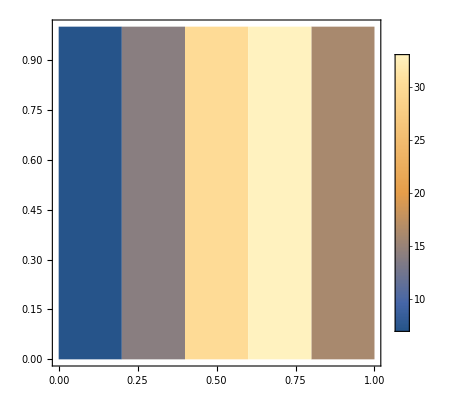

```mathematica
DensityHistogram[tab,ChartLegends->Automatic]
```

```mathematica
final
```

{1/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
finalstate//Concurrence
```

0

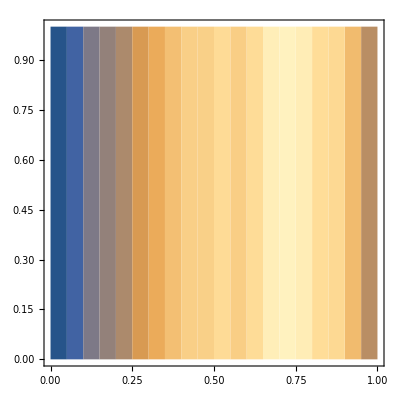
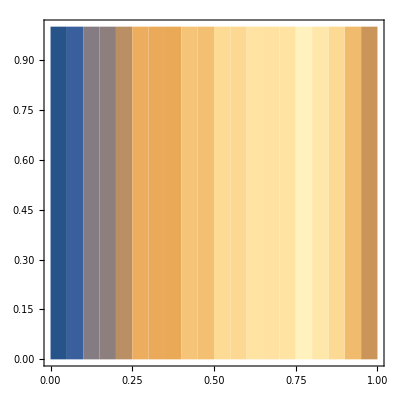
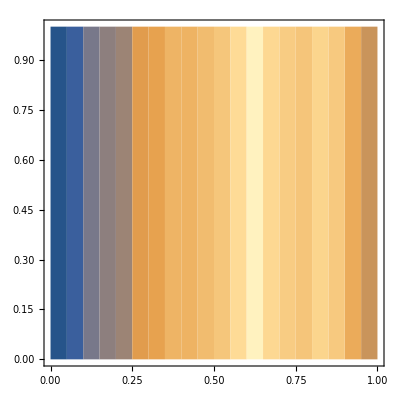
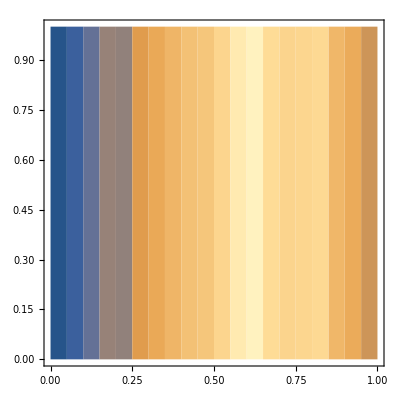
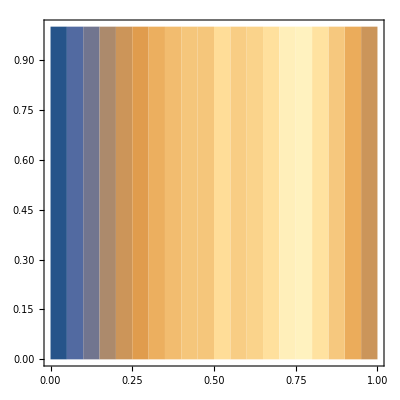
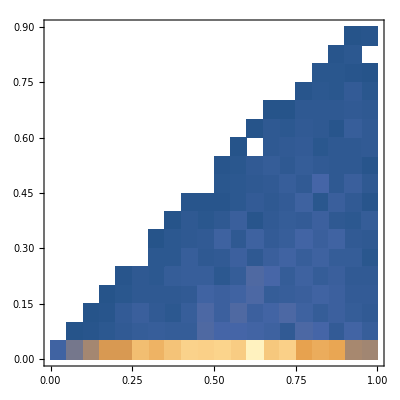
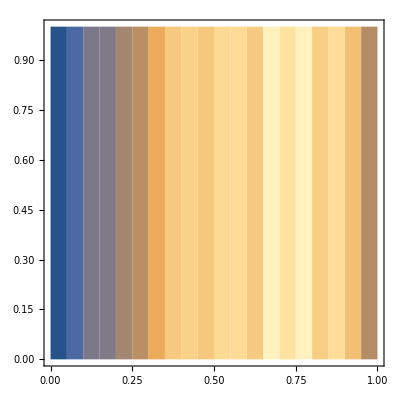
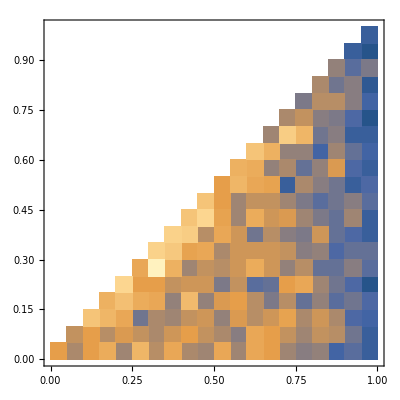

```mathematica
Table[DensityHistogram[ParallelTable[state=Proyector[RandomState[4]];
r=vectorr[state]//Chop;
final=DiagonalMatrix[chan//Flatten].Flatten[r];
finalstate=Sum[Partition[final,4][[i+1,j+1]]KroneckerProduct[PauliMatrix[i],PauliMatrix[j]],{i,0,3},{j,0,3}];
{Concurrence[state],Concurrence[finalstate]},{3000},DistributedContexts->All],Automatic,"Probability"],{chan,gen}]
```

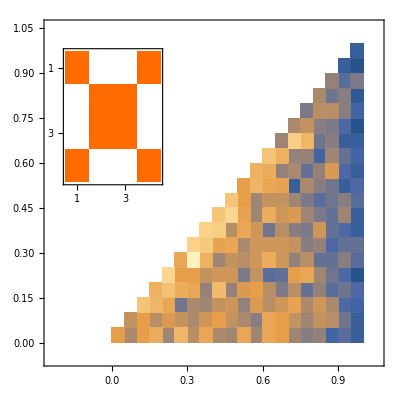

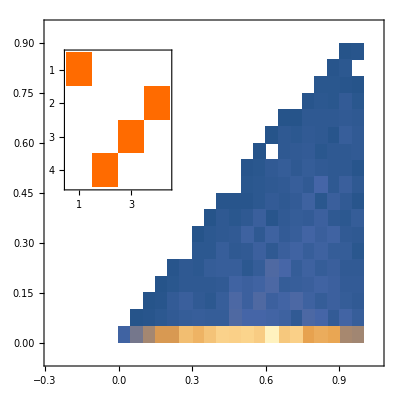

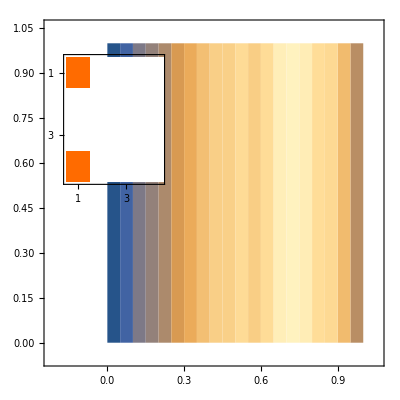

```mathematica
gen={class21,class22,class41,class42,class43,class44,class81,class82};
```

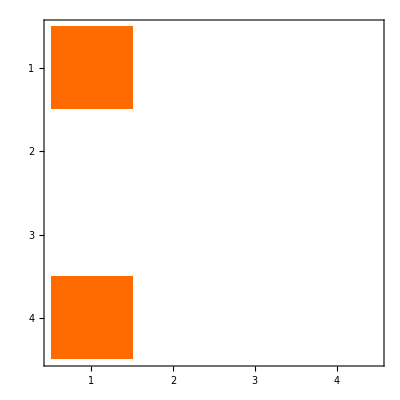
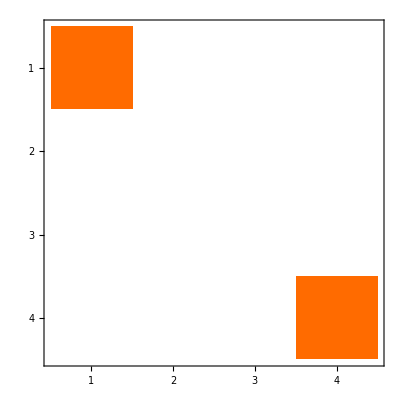
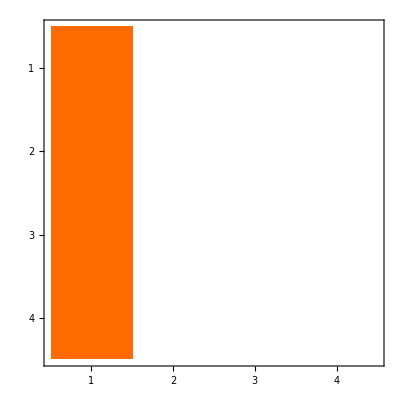
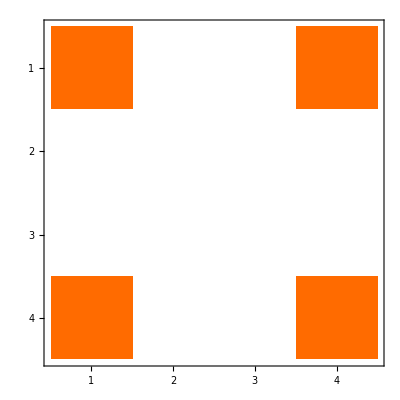
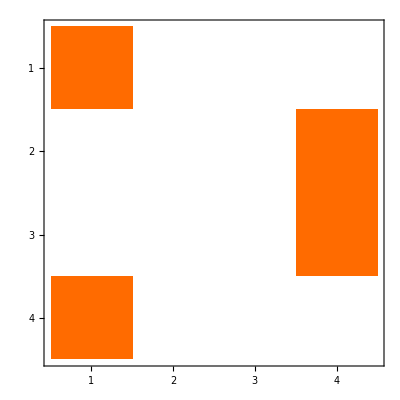
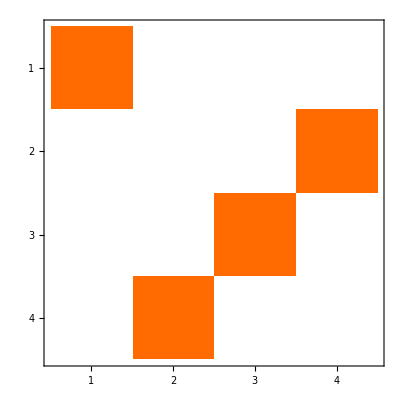
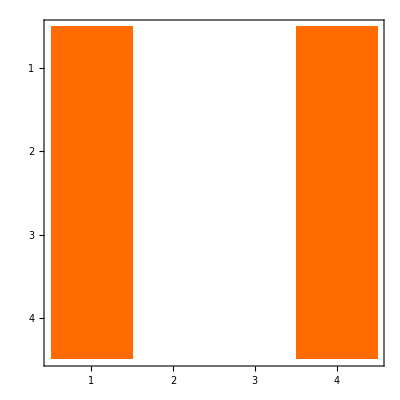
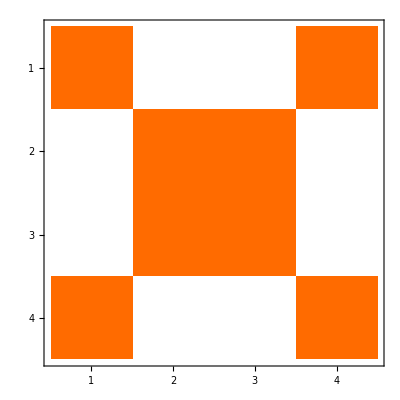

```mathematica
MatrixPlot/@gen
```

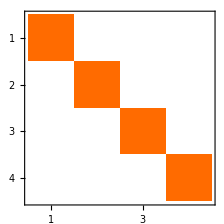

```mathematica
DiagonalMatrix[{1,1,1,1}]//MatrixPlot
```

## Entanglement breakability

### Clase 8

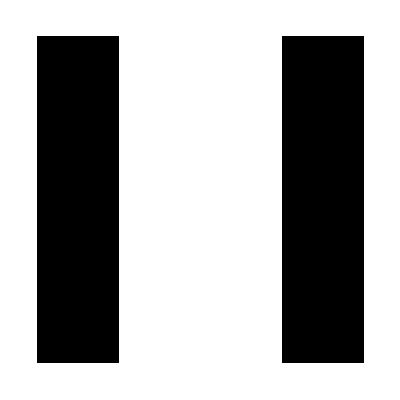
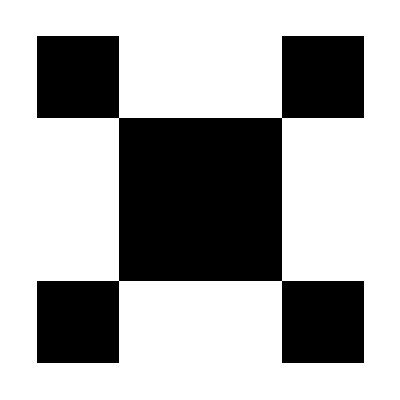

```mathematica
ArrayPlot/@{class81,class82}
```

```mathematica
mat=ChoiJamiStateFromPauliProductBasis[DiagonalMatrix[class81//Flatten]];mat//MatrixForm
```

(1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4)

```mathematica
{vals,vecs}=mat//Eigensystem;
```

```mathematica
{vals,StateToDirac[#,4]&/@vecs}//Transpose//TableForm
```

1/2 | |1 1⟩+|3 3⟩
1/2 | |0 0⟩+|2 2⟩
0 | -|1 1⟩+|3 3⟩
0 | |3 2⟩
0 | |3 1⟩
0 | |3 0⟩
0 | |2 3⟩
0 | -|0 0⟩+|2 2⟩
0 | |2 1⟩
0 | |2 0⟩
0 | |1 3⟩
0 | |1 2⟩
0 | |1 0⟩
0 | |0 3⟩
0 | |0 2⟩
0 | |0 1⟩

```mathematica
{mat//PositiveSemidefiniteMatrixQ,PartialTranspose[mat,1]//PositiveSemidefiniteMatrixQ}
```

{True,True}

```mathematica
mat=ChoiJamiStateFromPauliProductBasis[DiagonalMatrix[class82//Flatten]];mat//MatrixForm
```

(1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4)

```mathematica
{vals,vecs}=mat//Eigensystem;
```

```mathematica
{vals,StateToDirac[#,4]&/@vecs}//Transpose//TableForm
```

1/2 | |0 0⟩+|3 3⟩
1/2 | |1 1⟩+|2 2⟩
0 | -|0 0⟩+|3 3⟩
0 | |3 2⟩
0 | |3 1⟩
0 | |3 0⟩
0 | |2 3⟩
0 | -|1 1⟩+|2 2⟩
0 | |2 1⟩
0 | |2 0⟩
0 | |1 3⟩
0 | |1 2⟩
0 | |1 0⟩
0 | |0 3⟩
0 | |0 2⟩
0 | |0 1⟩

```mathematica
{mat//PositiveSemidefiniteMatrixQ,PartialTranspose[mat,1]//PositiveSemidefiniteMatrixQ}
```

{True,False}

```mathematica
mat//HermitianPart//PositiveSemidefiniteMatrixQ
```

True

### Clase 4

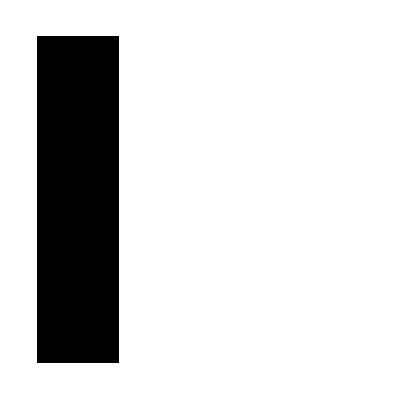
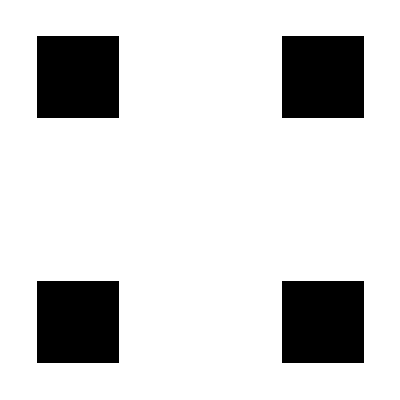
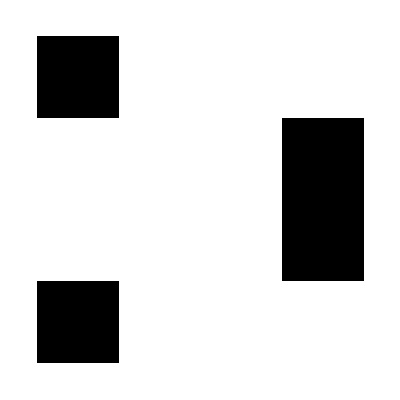
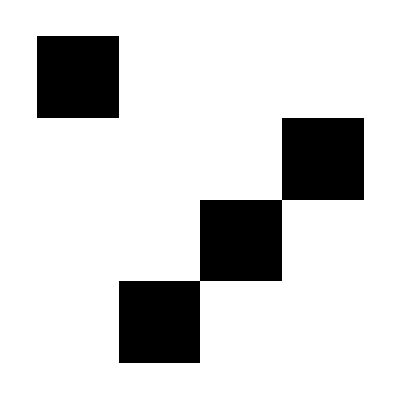

```mathematica
ArrayPlot/@{class41,class42,class43,class44}
```

```mathematica
mat=ChoiJamiStateFromPauliProductBasis[DiagonalMatrix[class41//Flatten]];mat//MatrixForm
```

(1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0
0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0
0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0
0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0
0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8)

```mathematica
{vals,vecs}=mat//Eigensystem;
```

```mathematica
{vals,StateToDirac[#,4]&/@vecs}//Transpose//TableForm
```

1/4 | |1 1⟩+|3 3⟩
1/4 | |1 0⟩+|3 2⟩
1/4 | |0 1⟩+|2 3⟩
1/4 | |0 0⟩+|2 2⟩
0 | -|1 1⟩+|3 3⟩
0 | -|1 0⟩+|3 2⟩
0 | |3 1⟩
0 | |3 0⟩
0 | -|0 1⟩+|2 3⟩
0 | -|0 0⟩+|2 2⟩
0 | |2 1⟩
0 | |2 0⟩
0 | |1 3⟩
0 | |1 2⟩
0 | |0 3⟩
0 | |0 2⟩

```mathematica
{mat//PositiveSemidefiniteMatrixQ,PartialTranspose[mat,1]//HermitianPart//PositiveSemidefiniteMatrixQ}
```

{True,True}

```mathematica
mat=ChoiJamiStateFromPauliProductBasis[DiagonalMatrix[class42//Flatten]];mat//MatrixForm
```

(1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4)

```mathematica
{vals,vecs}=mat//Eigensystem;
```

```mathematica
{vals,StateToDirac[#,4]&/@vecs}//Transpose//TableForm
```

1/4 | |3 3⟩
1/4 | |2 2⟩
1/4 | |1 1⟩
1/4 | |0 0⟩
0 | |3 2⟩
0 | |3 1⟩
0 | |3 0⟩
0 | |2 3⟩
0 | |2 1⟩
0 | |2 0⟩
0 | |1 3⟩
0 | |1 2⟩
0 | |1 0⟩
0 | |0 3⟩
0 | |0 2⟩
0 | |0 1⟩

```mathematica
{mat//PositiveSemidefiniteMatrixQ,PartialTranspose[mat,1]//PositiveSemidefiniteMatrixQ}
```

{True,True}

```mathematica
mat//HermitianPart//PositiveSemidefiniteMatrixQ
```

True

```mathematica
mat=ChoiJamiStateFromPauliProductBasis[DiagonalMatrix[class43//Flatten]];mat//MatrixForm
```

(1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0
0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/8 | 0
0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0
0 | -1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0
0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8)

```mathematica
{vals,vecs}=mat//Eigensystem;
```

```mathematica
{vals,StateToDirac[#,4]&/@vecs}//Transpose//TableForm
```

1/4 | |1 1⟩+|3 3⟩
1/4 | -|1 0⟩+|3 2⟩
1/4 | -|0 1⟩+|2 3⟩
1/4 | |0 0⟩+|2 2⟩
0 | -|1 1⟩+|3 3⟩
0 | |1 0⟩+|3 2⟩
0 | |3 1⟩
0 | |3 0⟩
0 | |0 1⟩+|2 3⟩
0 | -|0 0⟩+|2 2⟩
0 | |2 1⟩
0 | |2 0⟩
0 | |1 3⟩
0 | |1 2⟩
0 | |0 3⟩
0 | |0 2⟩

```mathematica
{mat//PositiveSemidefiniteMatrixQ,PartialTranspose[mat,1]//PositiveSemidefiniteMatrixQ}
```

{True,True}

```mathematica
mat//HermitianPart//PositiveSemidefiniteMatrixQ
```

True

```mathematica
mat=ChoiJamiStateFromPauliProductBasis[DiagonalMatrix[class44//Flatten]];mat//MatrixForm
```

(1/16 | 0 | 0 | 0 | 0 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 0 | 0 | 0 | 0 | 1/16
0 | 1/16 | 0 | 0 | 1/16 | 0 | 0 | 0 | 0 | 0 | 0 | -1/16 | 0 | 0 | -1/16 | 0
0 | 0 | 1/16 | 0 | 0 | 0 | 0 | -1/16 | 1/16 | 0 | 0 | 0 | 0 | -1/16 | 0 | 0
0 | 0 | 0 | 1/16 | 0 | 0 | -1/16 | 0 | 0 | -1/16 | 0 | 0 | 1/16 | 0 | 0 | 0
0 | 1/16 | 0 | 0 | 1/16 | 0 | 0 | 0 | 0 | 0 | 0 | -1/16 | 0 | 0 | -1/16 | 0
1/16 | 0 | 0 | 0 | 0 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 0 | 0 | 0 | 0 | 1/16
0 | 0 | 0 | -1/16 | 0 | 0 | 1/16 | 0 | 0 | 1/16 | 0 | 0 | -1/16 | 0 | 0 | 0
0 | 0 | -1/16 | 0 | 0 | 0 | 0 | 1/16 | -1/16 | 0 | 0 | 0 | 0 | 1/16 | 0 | 0
0 | 0 | 1/16 | 0 | 0 | 0 | 0 | -1/16 | 1/16 | 0 | 0 | 0 | 0 | -1/16 | 0 | 0
0 | 0 | 0 | -1/16 | 0 | 0 | 1/16 | 0 | 0 | 1/16 | 0 | 0 | -1/16 | 0 | 0 | 0
1/16 | 0 | 0 | 0 | 0 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 0 | 0 | 0 | 0 | 1/16
0 | -1/16 | 0 | 0 | -1/16 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 | 0 | 0 | 1/16 | 0
0 | 0 | 0 | 1/16 | 0 | 0 | -1/16 | 0 | 0 | -1/16 | 0 | 0 | 1/16 | 0 | 0 | 0
0 | 0 | -1/16 | 0 | 0 | 0 | 0 | 1/16 | -1/16 | 0 | 0 | 0 | 0 | 1/16 | 0 | 0
0 | -1/16 | 0 | 0 | -1/16 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 | 0 | 0 | 1/16 | 0
1/16 | 0 | 0 | 0 | 0 | 1/16 | 0 | 0 | 0 | 0 | 1/16 | 0 | 0 | 0 | 0 | 1/16)

```mathematica
{vals,vecs}=mat//Eigensystem;
```

```mathematica
{vals,StateToDirac[#,4]&/@vecs}//Transpose//TableForm
```

1/4 | |0 0⟩+|1 1⟩+|2 2⟩+|3 3⟩
1/4 | -|0 1⟩-|1 0⟩+|2 3⟩+|3 2⟩
1/4 | -|0 2⟩+|1 3⟩-|2 0⟩+|3 1⟩
1/4 | |0 3⟩-|1 2⟩-|2 1⟩+|3 0⟩
0 | -|0 0⟩+|3 3⟩
0 | |0 1⟩+|3 2⟩
0 | |0 2⟩+|3 1⟩
0 | -|0 3⟩+|3 0⟩
0 | |0 1⟩+|2 3⟩
0 | -|0 0⟩+|2 2⟩
0 | |0 3⟩+|2 1⟩
0 | -|0 2⟩+|2 0⟩
0 | |0 2⟩+|1 3⟩
0 | |0 3⟩+|1 2⟩
0 | -|0 0⟩+|1 1⟩
0 | -|0 1⟩+|1 0⟩

```mathematica
{mat//PositiveSemidefiniteMatrixQ,PartialTranspose[mat,1]//PositiveSemidefiniteMatrixQ}
```

{True,False}

```mathematica
mat//HermitianPart//PositiveSemidefiniteMatrixQ
```

True

### Clase 2

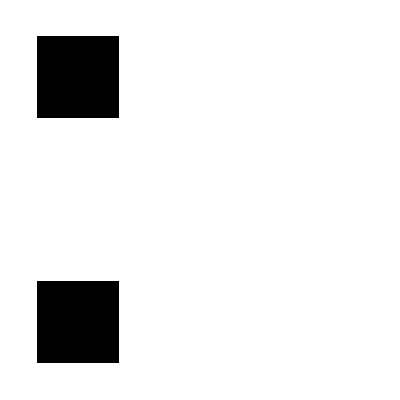
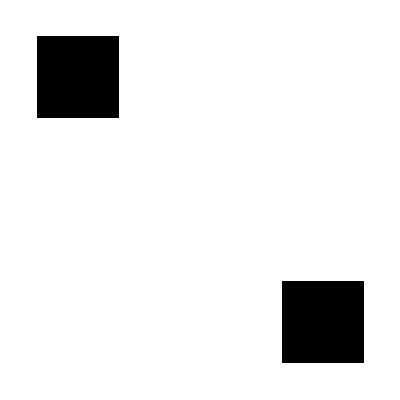

```mathematica
ArrayPlot/@{class21,class22}
```

```mathematica
mat=ChoiJamiStateFromPauliProductBasis[DiagonalMatrix[class21//Flatten]];mat//MatrixForm
```

(1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8)

```mathematica
{vals,vecs}=mat//Eigensystem;
```

```mathematica
{vals,StateToDirac[#,4]&/@vecs}//Transpose//TableForm
```

1/8 | |3 3⟩
1/8 | |3 2⟩
1/8 | |2 3⟩
1/8 | |2 2⟩
1/8 | |1 1⟩
1/8 | |1 0⟩
1/8 | |0 1⟩
1/8 | |0 0⟩
0 | |3 1⟩
0 | |3 0⟩
0 | |2 1⟩
0 | |2 0⟩
0 | |1 3⟩
0 | |1 2⟩
0 | |0 3⟩
0 | |0 2⟩

```mathematica
{mat//PositiveSemidefiniteMatrixQ,PartialTranspose[mat,1]//HermitianPart//PositiveSemidefiniteMatrixQ}
```

{True,True}

```mathematica
mat=ChoiJamiStateFromPauliProductBasis[DiagonalMatrix[class22//Flatten]];mat//MatrixForm
```

(1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8)

```mathematica
{vals,vecs}=mat//Eigensystem;
```

```mathematica
{vals,StateToDirac[#,4]&/@vecs}//Transpose//TableForm
```

1/8 | |3 3⟩
1/8 | |3 0⟩
1/8 | |2 2⟩
1/8 | |2 1⟩
1/8 | |1 2⟩
1/8 | |1 1⟩
1/8 | |0 3⟩
1/8 | |0 0⟩
0 | |3 2⟩
0 | |3 1⟩
0 | |2 3⟩
0 | |2 0⟩
0 | |1 3⟩
0 | |1 0⟩
0 | |0 2⟩
0 | |0 1⟩

### test de transpuesta parcial

```mathematica
test=Flatten[Table[Flatten[Table[Subscript[ρ, i,j,k,l],{i,0,3},{j,0,3}]],{k,0,3},{l,0,3}],1]//Transpose;test//MatrixForm
```

(ρ_(0,0,0,0) | ρ_(0,0,0,1) | ρ_(0,0,0,2) | ρ_(0,0,0,3) | ρ_(0,0,1,0) | ρ_(0,0,1,1) | ρ_(0,0,1,2) | ρ_(0,0,1,3) | ρ_(0,0,2,0) | ρ_(0,0,2,1) | ρ_(0,0,2,2) | ρ_(0,0,2,3) | ρ_(0,0,3,0) | ρ_(0,0,3,1) | ρ_(0,0,3,2) | ρ_(0,0,3,3)
ρ_(0,1,0,0) | ρ_(0,1,0,1) | ρ_(0,1,0,2) | ρ_(0,1,0,3) | ρ_(0,1,1,0) | ρ_(0,1,1,1) | ρ_(0,1,1,2) | ρ_(0,1,1,3) | ρ_(0,1,2,0) | ρ_(0,1,2,1) | ρ_(0,1,2,2) | ρ_(0,1,2,3) | ρ_(0,1,3,0) | ρ_(0,1,3,1) | ρ_(0,1,3,2) | ρ_(0,1,3,3)
ρ_(0,2,0,0) | ρ_(0,2,0,1) | ρ_(0,2,0,2) | ρ_(0,2,0,3) | ρ_(0,2,1,0) | ρ_(0,2,1,1) | ρ_(0,2,1,2) | ρ_(0,2,1,3) | ρ_(0,2,2,0) | ρ_(0,2,2,1) | ρ_(0,2,2,2) | ρ_(0,2,2,3) | ρ_(0,2,3,0) | ρ_(0,2,3,1) | ρ_(0,2,3,2) | ρ_(0,2,3,3)
ρ_(0,3,0,0) | ρ_(0,3,0,1) | ρ_(0,3,0,2) | ρ_(0,3,0,3) | ρ_(0,3,1,0) | ρ_(0,3,1,1) | ρ_(0,3,1,2) | ρ_(0,3,1,3) | ρ_(0,3,2,0) | ρ_(0,3,2,1) | ρ_(0,3,2,2) | ρ_(0,3,2,3) | ρ_(0,3,3,0) | ρ_(0,3,3,1) | ρ_(0,3,3,2) | ρ_(0,3,3,3)
ρ_(1,0,0,0) | ρ_(1,0,0,1) | ρ_(1,0,0,2) | ρ_(1,0,0,3) | ρ_(1,0,1,0) | ρ_(1,0,1,1) | ρ_(1,0,1,2) | ρ_(1,0,1,3) | ρ_(1,0,2,0) | ρ_(1,0,2,1) | ρ_(1,0,2,2) | ρ_(1,0,2,3) | ρ_(1,0,3,0) | ρ_(1,0,3,1) | ρ_(1,0,3,2) | ρ_(1,0,3,3)
ρ_(1,1,0,0) | ρ_(1,1,0,1) | ρ_(1,1,0,2) | ρ_(1,1,0,3) | ρ_(1,1,1,0) | ρ_(1,1,1,1) | ρ_(1,1,1,2) | ρ_(1,1,1,3) | ρ_(1,1,2,0) | ρ_(1,1,2,1) | ρ_(1,1,2,2) | ρ_(1,1,2,3) | ρ_(1,1,3,0) | ρ_(1,1,3,1) | ρ_(1,1,3,2) | ρ_(1,1,3,3)
ρ_(1,2,0,0) | ρ_(1,2,0,1) | ρ_(1,2,0,2) | ρ_(1,2,0,3) | ρ_(1,2,1,0) | ρ_(1,2,1,1) | ρ_(1,2,1,2) | ρ_(1,2,1,3) | ρ_(1,2,2,0) | ρ_(1,2,2,1) | ρ_(1,2,2,2) | ρ_(1,2,2,3) | ρ_(1,2,3,0) | ρ_(1,2,3,1) | ρ_(1,2,3,2) | ρ_(1,2,3,3)
ρ_(1,3,0,0) | ρ_(1,3,0,1) | ρ_(1,3,0,2) | ρ_(1,3,0,3) | ρ_(1,3,1,0) | ρ_(1,3,1,1) | ρ_(1,3,1,2) | ρ_(1,3,1,3) | ρ_(1,3,2,0) | ρ_(1,3,2,1) | ρ_(1,3,2,2) | ρ_(1,3,2,3) | ρ_(1,3,3,0) | ρ_(1,3,3,1) | ρ_(1,3,3,2) | ρ_(1,3,3,3)
ρ_(2,0,0,0) | ρ_(2,0,0,1) | ρ_(2,0,0,2) | ρ_(2,0,0,3) | ρ_(2,0,1,0) | ρ_(2,0,1,1) | ρ_(2,0,1,2) | ρ_(2,0,1,3) | ρ_(2,0,2,0) | ρ_(2,0,2,1) | ρ_(2,0,2,2) | ρ_(2,0,2,3) | ρ_(2,0,3,0) | ρ_(2,0,3,1) | ρ_(2,0,3,2) | ρ_(2,0,3,3)
ρ_(2,1,0,0) | ρ_(2,1,0,1) | ρ_(2,1,0,2) | ρ_(2,1,0,3) | ρ_(2,1,1,0) | ρ_(2,1,1,1) | ρ_(2,1,1,2) | ρ_(2,1,1,3) | ρ_(2,1,2,0) | ρ_(2,1,2,1) | ρ_(2,1,2,2) | ρ_(2,1,2,3) | ρ_(2,1,3,0) | ρ_(2,1,3,1) | ρ_(2,1,3,2) | ρ_(2,1,3,3)
ρ_(2,2,0,0) | ρ_(2,2,0,1) | ρ_(2,2,0,2) | ρ_(2,2,0,3) | ρ_(2,2,1,0) | ρ_(2,2,1,1) | ρ_(2,2,1,2) | ρ_(2,2,1,3) | ρ_(2,2,2,0) | ρ_(2,2,2,1) | ρ_(2,2,2,2) | ρ_(2,2,2,3) | ρ_(2,2,3,0) | ρ_(2,2,3,1) | ρ_(2,2,3,2) | ρ_(2,2,3,3)
ρ_(2,3,0,0) | ρ_(2,3,0,1) | ρ_(2,3,0,2) | ρ_(2,3,0,3) | ρ_(2,3,1,0) | ρ_(2,3,1,1) | ρ_(2,3,1,2) | ρ_(2,3,1,3) | ρ_(2,3,2,0) | ρ_(2,3,2,1) | ρ_(2,3,2,2) | ρ_(2,3,2,3) | ρ_(2,3,3,0) | ρ_(2,3,3,1) | ρ_(2,3,3,2) | ρ_(2,3,3,3)
ρ_(3,0,0,0) | ρ_(3,0,0,1) | ρ_(3,0,0,2) | ρ_(3,0,0,3) | ρ_(3,0,1,0) | ρ_(3,0,1,1) | ρ_(3,0,1,2) | ρ_(3,0,1,3) | ρ_(3,0,2,0) | ρ_(3,0,2,1) | ρ_(3,0,2,2) | ρ_(3,0,2,3) | ρ_(3,0,3,0) | ρ_(3,0,3,1) | ρ_(3,0,3,2) | ρ_(3,0,3,3)
ρ_(3,1,0,0) | ρ_(3,1,0,1) | ρ_(3,1,0,2) | ρ_(3,1,0,3) | ρ_(3,1,1,0) | ρ_(3,1,1,1) | ρ_(3,1,1,2) | ρ_(3,1,1,3) | ρ_(3,1,2,0) | ρ_(3,1,2,1) | ρ_(3,1,2,2) | ρ_(3,1,2,3) | ρ_(3,1,3,0) | ρ_(3,1,3,1) | ρ_(3,1,3,2) | ρ_(3,1,3,3)
ρ_(3,2,0,0) | ρ_(3,2,0,1) | ρ_(3,2,0,2) | ρ_(3,2,0,3) | ρ_(3,2,1,0) | ρ_(3,2,1,1) | ρ_(3,2,1,2) | ρ_(3,2,1,3) | ρ_(3,2,2,0) | ρ_(3,2,2,1) | ρ_(3,2,2,2) | ρ_(3,2,2,3) | ρ_(3,2,3,0) | ρ_(3,2,3,1) | ρ_(3,2,3,2) | ρ_(3,2,3,3)
ρ_(3,3,0,0) | ρ_(3,3,0,1) | ρ_(3,3,0,2) | ρ_(3,3,0,3) | ρ_(3,3,1,0) | ρ_(3,3,1,1) | ρ_(3,3,1,2) | ρ_(3,3,1,3) | ρ_(3,3,2,0) | ρ_(3,3,2,1) | ρ_(3,3,2,2) | ρ_(3,3,2,3) | ρ_(3,3,3,0) | ρ_(3,3,3,1) | ρ_(3,3,3,2) | ρ_(3,3,3,3))

```mathematica
(test-PartialTranspose[test,1])//MatrixForm
```

(0 | ρ_(0,0,0,1)-ρ_(0,1,0,0) | 0 | ρ_(0,0,0,3)-ρ_(0,1,0,2) | 0 | ρ_(0,0,1,1)-ρ_(0,1,1,0) | 0 | ρ_(0,0,1,3)-ρ_(0,1,1,2) | 0 | ρ_(0,0,2,1)-ρ_(0,1,2,0) | 0 | ρ_(0,0,2,3)-ρ_(0,1,2,2) | 0 | ρ_(0,0,3,1)-ρ_(0,1,3,0) | 0 | ρ_(0,0,3,3)-ρ_(0,1,3,2)
-ρ_(0,0,0,1)+ρ_(0,1,0,0) | 0 | -ρ_(0,0,0,3)+ρ_(0,1,0,2) | 0 | -ρ_(0,0,1,1)+ρ_(0,1,1,0) | 0 | -ρ_(0,0,1,3)+ρ_(0,1,1,2) | 0 | -ρ_(0,0,2,1)+ρ_(0,1,2,0) | 0 | -ρ_(0,0,2,3)+ρ_(0,1,2,2) | 0 | -ρ_(0,0,3,1)+ρ_(0,1,3,0) | 0 | -ρ_(0,0,3,3)+ρ_(0,1,3,2) | 0
0 | ρ_(0,2,0,1)-ρ_(0,3,0,0) | 0 | ρ_(0,2,0,3)-ρ_(0,3,0,2) | 0 | ρ_(0,2,1,1)-ρ_(0,3,1,0) | 0 | ρ_(0,2,1,3)-ρ_(0,3,1,2) | 0 | ρ_(0,2,2,1)-ρ_(0,3,2,0) | 0 | ρ_(0,2,2,3)-ρ_(0,3,2,2) | 0 | ρ_(0,2,3,1)-ρ_(0,3,3,0) | 0 | ρ_(0,2,3,3)-ρ_(0,3,3,2)
-ρ_(0,2,0,1)+ρ_(0,3,0,0) | 0 | -ρ_(0,2,0,3)+ρ_(0,3,0,2) | 0 | -ρ_(0,2,1,1)+ρ_(0,3,1,0) | 0 | -ρ_(0,2,1,3)+ρ_(0,3,1,2) | 0 | -ρ_(0,2,2,1)+ρ_(0,3,2,0) | 0 | -ρ_(0,2,2,3)+ρ_(0,3,2,2) | 0 | -ρ_(0,2,3,1)+ρ_(0,3,3,0) | 0 | -ρ_(0,2,3,3)+ρ_(0,3,3,2) | 0
0 | ρ_(1,0,0,1)-ρ_(1,1,0,0) | 0 | ρ_(1,0,0,3)-ρ_(1,1,0,2) | 0 | ρ_(1,0,1,1)-ρ_(1,1,1,0) | 0 | ρ_(1,0,1,3)-ρ_(1,1,1,2) | 0 | ρ_(1,0,2,1)-ρ_(1,1,2,0) | 0 | ρ_(1,0,2,3)-ρ_(1,1,2,2) | 0 | ρ_(1,0,3,1)-ρ_(1,1,3,0) | 0 | ρ_(1,0,3,3)-ρ_(1,1,3,2)
-ρ_(1,0,0,1)+ρ_(1,1,0,0) | 0 | -ρ_(1,0,0,3)+ρ_(1,1,0,2) | 0 | -ρ_(1,0,1,1)+ρ_(1,1,1,0) | 0 | -ρ_(1,0,1,3)+ρ_(1,1,1,2) | 0 | -ρ_(1,0,2,1)+ρ_(1,1,2,0) | 0 | -ρ_(1,0,2,3)+ρ_(1,1,2,2) | 0 | -ρ_(1,0,3,1)+ρ_(1,1,3,0) | 0 | -ρ_(1,0,3,3)+ρ_(1,1,3,2) | 0
0 | ρ_(1,2,0,1)-ρ_(1,3,0,0) | 0 | ρ_(1,2,0,3)-ρ_(1,3,0,2) | 0 | ρ_(1,2,1,1)-ρ_(1,3,1,0) | 0 | ρ_(1,2,1,3)-ρ_(1,3,1,2) | 0 | ρ_(1,2,2,1)-ρ_(1,3,2,0) | 0 | ρ_(1,2,2,3)-ρ_(1,3,2,2) | 0 | ρ_(1,2,3,1)-ρ_(1,3,3,0) | 0 | ρ_(1,2,3,3)-ρ_(1,3,3,2)
-ρ_(1,2,0,1)+ρ_(1,3,0,0) | 0 | -ρ_(1,2,0,3)+ρ_(1,3,0,2) | 0 | -ρ_(1,2,1,1)+ρ_(1,3,1,0) | 0 | -ρ_(1,2,1,3)+ρ_(1,3,1,2) | 0 | -ρ_(1,2,2,1)+ρ_(1,3,2,0) | 0 | -ρ_(1,2,2,3)+ρ_(1,3,2,2) | 0 | -ρ_(1,2,3,1)+ρ_(1,3,3,0) | 0 | -ρ_(1,2,3,3)+ρ_(1,3,3,2) | 0
0 | ρ_(2,0,0,1)-ρ_(2,1,0,0) | 0 | ρ_(2,0,0,3)-ρ_(2,1,0,2) | 0 | ρ_(2,0,1,1)-ρ_(2,1,1,0) | 0 | ρ_(2,0,1,3)-ρ_(2,1,1,2) | 0 | ρ_(2,0,2,1)-ρ_(2,1,2,0) | 0 | ρ_(2,0,2,3)-ρ_(2,1,2,2) | 0 | ρ_(2,0,3,1)-ρ_(2,1,3,0) | 0 | ρ_(2,0,3,3)-ρ_(2,1,3,2)
-ρ_(2,0,0,1)+ρ_(2,1,0,0) | 0 | -ρ_(2,0,0,3)+ρ_(2,1,0,2) | 0 | -ρ_(2,0,1,1)+ρ_(2,1,1,0) | 0 | -ρ_(2,0,1,3)+ρ_(2,1,1,2) | 0 | -ρ_(2,0,2,1)+ρ_(2,1,2,0) | 0 | -ρ_(2,0,2,3)+ρ_(2,1,2,2) | 0 | -ρ_(2,0,3,1)+ρ_(2,1,3,0) | 0 | -ρ_(2,0,3,3)+ρ_(2,1,3,2) | 0
0 | ρ_(2,2,0,1)-ρ_(2,3,0,0) | 0 | ρ_(2,2,0,3)-ρ_(2,3,0,2) | 0 | ρ_(2,2,1,1)-ρ_(2,3,1,0) | 0 | ρ_(2,2,1,3)-ρ_(2,3,1,2) | 0 | ρ_(2,2,2,1)-ρ_(2,3,2,0) | 0 | ρ_(2,2,2,3)-ρ_(2,3,2,2) | 0 | ρ_(2,2,3,1)-ρ_(2,3,3,0) | 0 | ρ_(2,2,3,3)-ρ_(2,3,3,2)
-ρ_(2,2,0,1)+ρ_(2,3,0,0) | 0 | -ρ_(2,2,0,3)+ρ_(2,3,0,2) | 0 | -ρ_(2,2,1,1)+ρ_(2,3,1,0) | 0 | -ρ_(2,2,1,3)+ρ_(2,3,1,2) | 0 | -ρ_(2,2,2,1)+ρ_(2,3,2,0) | 0 | -ρ_(2,2,2,3)+ρ_(2,3,2,2) | 0 | -ρ_(2,2,3,1)+ρ_(2,3,3,0) | 0 | -ρ_(2,2,3,3)+ρ_(2,3,3,2) | 0
0 | ρ_(3,0,0,1)-ρ_(3,1,0,0) | 0 | ρ_(3,0,0,3)-ρ_(3,1,0,2) | 0 | ρ_(3,0,1,1)-ρ_(3,1,1,0) | 0 | ρ_(3,0,1,3)-ρ_(3,1,1,2) | 0 | ρ_(3,0,2,1)-ρ_(3,1,2,0) | 0 | ρ_(3,0,2,3)-ρ_(3,1,2,2) | 0 | ρ_(3,0,3,1)-ρ_(3,1,3,0) | 0 | ρ_(3,0,3,3)-ρ_(3,1,3,2)
-ρ_(3,0,0,1)+ρ_(3,1,0,0) | 0 | -ρ_(3,0,0,3)+ρ_(3,1,0,2) | 0 | -ρ_(3,0,1,1)+ρ_(3,1,1,0) | 0 | -ρ_(3,0,1,3)+ρ_(3,1,1,2) | 0 | -ρ_(3,0,2,1)+ρ_(3,1,2,0) | 0 | -ρ_(3,0,2,3)+ρ_(3,1,2,2) | 0 | -ρ_(3,0,3,1)+ρ_(3,1,3,0) | 0 | -ρ_(3,0,3,3)+ρ_(3,1,3,2) | 0
0 | ρ_(3,2,0,1)-ρ_(3,3,0,0) | 0 | ρ_(3,2,0,3)-ρ_(3,3,0,2) | 0 | ρ_(3,2,1,1)-ρ_(3,3,1,0) | 0 | ρ_(3,2,1,3)-ρ_(3,3,1,2) | 0 | ρ_(3,2,2,1)-ρ_(3,3,2,0) | 0 | ρ_(3,2,2,3)-ρ_(3,3,2,2) | 0 | ρ_(3,2,3,1)-ρ_(3,3,3,0) | 0 | ρ_(3,2,3,3)-ρ_(3,3,3,2)
-ρ_(3,2,0,1)+ρ_(3,3,0,0) | 0 | -ρ_(3,2,0,3)+ρ_(3,3,0,2) | 0 | -ρ_(3,2,1,1)+ρ_(3,3,1,0) | 0 | -ρ_(3,2,1,3)+ρ_(3,3,1,2) | 0 | -ρ_(3,2,2,1)+ρ_(3,3,2,0) | 0 | -ρ_(3,2,2,3)+ρ_(3,3,2,2) | 0 | -ρ_(3,2,3,1)+ρ_(3,3,3,0) | 0 | -ρ_(3,2,3,3)+ρ_(3,3,3,2) | 0)

## Trazas aproximada

```mathematica
PartialTrace[KroneckerProduct[Proyector[RandomState[2]],IdentityMatrix[2]/2],2]
```

{{0.435512+0. ⅈ,0.00798202-0.49576 ⅈ},{0.00798202+0.49576 ⅈ,0.564488+0. ⅈ}}

### Copying one particle state

```mathematica
channel[ρ_]:=(1-μ)KroneckerProduct[PartialTrace[ρ,2],PartialTrace[ρ,2]]+μ Tr[ρ]IdentityMatrix[4]/4
```

```mathematica
final=channel[KroneckerProduct[init=Proyector[RandomState[2]],Proyector[RandomState[2]]]]//Chop//FullSimplify;
```

```mathematica
Tr[PartialTrace[final,1].init]//FullSimplify
```

1.-0.5 μ

```mathematica
Reduce[And@@Thread[(QuantumMapInProductPauliBasis[channel,2]//ChoiJamiStateFromPauliProductBasis//Eigenvalues)≥0],Reals]
```

(-4+4 √3)/(-3+4 √3)≤μ≤(4+4 √3)/(3+4 √3)

```mathematica
QuantumMapInProductPauliBasis[channel,2]//ChoiJamiStateFromPauliProductBasis//FullSimplify//MatrixForm
```

(1/16 (8-7 μ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1/4+ⅈ/4) (-1+μ) | 0
0 | 1/16 (8-7 μ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1/4+ⅈ/4) (-1+μ)
0 | 0 | μ/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1/4-ⅈ/4) (-1+μ) | 0 | 0 | 0
0 | 0 | 0 | μ/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1/4-ⅈ/4) (-1+μ) | 0 | 0
0 | 0 | 0 | 0 | μ/16 | 0 | 0 | 0 | 0 | 0 | (-1/4-ⅈ/4) (-1+μ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | μ/16 | 0 | 0 | 0 | 0 | 0 | (-1/4-ⅈ/4) (-1+μ) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/16 (8-7 μ) | 0 | (-1/4+ⅈ/4) (-1+μ) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 (8-7 μ) | 0 | (-1/4+ⅈ/4) (-1+μ) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (-1/4-ⅈ/4) (-1+μ) | 0 | μ/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1/4-ⅈ/4) (-1+μ) | 0 | μ/16 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (-1/4+ⅈ/4) (-1+μ) | 0 | 0 | 0 | 0 | 0 | 1/16 (8-7 μ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (-1/4+ⅈ/4) (-1+μ) | 0 | 0 | 0 | 0 | 0 | 1/16 (8-7 μ) | 0 | 0 | 0 | 0
0 | 0 | (-1/4+ⅈ/4) (-1+μ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 (8-7 μ) | 0 | 0 | 0
0 | 0 | 0 | (-1/4+ⅈ/4) (-1+μ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 (8-7 μ) | 0 | 0
(-1/4-ⅈ/4) (-1+μ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | μ/16 | 0
0 | (-1/4-ⅈ/4) (-1+μ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | μ/16)

## Trazas aproximada 2

```mathematica
PartialTrace[KroneckerProduct[Proyector[RandomState[2]],IdentityMatrix[2]/2],1]
```

{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.5+0. ⅈ}}

### Copying one particle state

```mathematica
channel[ρ_]:=(1-μ)KroneckerProduct[PartialTrace[ρ,2],IdentityMatrix[2]/2]+μ KroneckerProduct[IdentityMatrix[2]/2,PartialTrace[ρ,1]]
```

```mathematica
final=channel[KroneckerProduct[init=Proyector[RandomState[2]],Proyector[RandomState[2]]]]//Chop//FullSimplify;
```

```mathematica
Tr[PartialTrace[final,1].init]//FullSimplify
```

0.600273-0.600273 μ

```mathematica
channel[Proyector[RandomState[4]]]//Chop//Tr//Expand
```

1.

```mathematica
Reduce[And@@Thread[(QuantumMapInProductPauliBasis[channel,2]//ChoiJamiStateFromPauliProductBasis//Eigenvalues)≥0],Reals]
```

μ≤1

```mathematica
init=Table[Subscript[r, i,j],{i,0,3},{j,0,3}]//Flatten;final=QuantumMapInProductPauliBasis[channel,2].init;Partition[final,4]//FullSimplify//Simplify//MatrixForm
```

(r_(0,0) | μ r_(0,1) | μ r_(0,2) | μ r_(0,3)
-(-1+μ) r_(1,0) | 0 | 0 | 0
-(-1+μ) r_(2,0) | 0 | 0 | 0
-(-1+μ) r_(3,0) | 0 | 0 | 0)

```mathematica
QuantumMapInProductPauliBasis[channel,2]//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | μ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | μ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | μ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1-μ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1-μ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1-μ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
QuantumMapInProductPauliBasis[channel,2]//ChoiJamiStateFromPauliProductBasis//FullSimplify//MatrixForm
```

((1-μ)/4 | 0 | 0 | 0 | 0 | (1-μ)/8 | 0 | 0 | 0 | 0 | (1-μ)/8 | 0 | 0 | 0 | 0 | 0
0 | (1-μ)/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (1-μ)/8 | 0 | 0 | 0 | 0
0 | 0 | (1-μ)/8 | 0 | 0 | 0 | 0 | (1-μ)/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (1-μ)/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (1-μ)/8 | 0
(1-μ)/8 | 0 | 0 | 0 | 0 | (1-μ)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (1-μ)/8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (1-μ)/8 | 0 | 0 | 0 | 0 | (1-μ)/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (1-μ)/8 | 0 | 0 | 0 | 0 | (1-μ)/8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(1-μ)/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (1-μ)/4 | 0 | 0 | 0 | 0 | (1-μ)/8
0 | (1-μ)/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (1-μ)/8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (1-μ)/8 | 0 | 0 | 0 | 0 | (1-μ)/8 | 0 | 0
0 | 0 | 0 | 0 | (1-μ)/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (1-μ)/8 | 0
0 | 0 | 0 | 0 | 0 | (1-μ)/8 | 0 | 0 | 0 | 0 | (1-μ)/8 | 0 | 0 | 0 | 0 | (1-μ)/4)

## Calculating Kraus operators

```mathematica
tmp
```

{1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1}

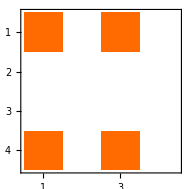

```mathematica
tmp=listvalid[[25]];chanetest=tmp//DiagonalMatrix;Partition[tmp,4]//MatrixPlot
```

```mathematica
MatrixForm/@KrausQubitParticlesFromPauliProductBasis[chanetest]
```

{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1/2 | 0
0 | 0 | 0 | 1/2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/2
0 | 0 | -1/2 | 0),(1/2 | 0 | 0 | 0
0 | 1/2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 1/2 | 0 | 0
-1/2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

```mathematica
StateToDirac/@KrausQubitParticlesFromPauliProductBasis[chanetest]//TableForm
```

(|1 0⟩⟨1 0|)/2+(|1 1⟩⟨1 1|)/2
(|1 0⟩⟨1 1|)/2-(|1 1⟩⟨1 0|)/2
(|0 0⟩⟨0 0|)/2+(|0 1⟩⟨0 1|)/2
(|0 0⟩⟨0 1|)/2-(|0 1⟩⟨0 0|)/2

```mathematica
ChoiJamiStateFromPauliProductBasis[chanetest]//MatrixRank
```

2

```mathematica
Log2[Length[chanetest]]/2
```

2

```mathematica
ChoiJamiStateFromPauliProductBasis[chanetest]//Eigensystem//Transpose
```

{{1/2,{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1}},{1/2,{0,0,1,0,0,0,0,1,1,0,0,0,0,1,0,0}},{0,{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}},{0,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0}},{0,{0,0,-1,0,0,0,0,0,0,0,0,0,0,1,0,0}},{0,{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0}},{0,{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0}},{0,{-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0}},{0,{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0}},{0,{0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0}},{0,{0,0,-1,0,0,0,0,1,0,0,0,0,0,0,0,0}},{0,{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0}},{0,{-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}},{0,{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}},{0,{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0}},{0,{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
Map[Sqrt[#[[1]]]Transpose[Partition[#[[2]],Sqrt[Length[chanetest]]]]&,ChoiJamiStateFromPauliProductBasis[chanetest]//Eigensystem//Transpose]//Chop
```

{{{1/(√2),0,0,0},{0,1/(√2),0,0},{0,0,1/(√2),0},{0,0,0,1/(√2)}},{{0,0,1/(√2),0},{0,0,0,1/(√2)},{1/(√2),0,0,0},{0,1/(√2),0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
??ChoiJamiStateFromPauliProductBasis
```

```mathematica
Log2[Length[chanetest]]/2
```

2

## Stinespring dilations

```mathematica
PartialUnitary[state_,indices_]:=Flatten[1/Sqrt[2]KroneckerProduct[state,BasisState[0,2]]+1/Sqrt[2]KroneckerProduct[If[Length[indices]==1,PauliMatrix[First[indices]],KroneckerProduct@@Table[PauliMatrix[i],{i,indices}]].state,BasisState[1,2]]]
```

```mathematica
PauliMatrix[2].{1,0}
```

{0,ⅈ}

```mathematica
PauliMatrix[2].{0,1}
```

{-ⅈ,0}

```mathematica
PartialUnitary[BasisState[1,2],{3}]
```

{0,0,1/(√2),-1/(√2)}

```mathematica
AbstractMap[ρ_,t_]:=((Sqrt[2]-1)Exp[-γ t]+1)/Sqrt[2]ρ+(1-Exp[-γ t])/Sqrt[2] A.ρ.A
```

```mathematica
$Assumptions=Element[{γ,Subscript[t, 1],Subscript[t, 2]},Reals]
```

(γ|t_1|t_2)∈ℝ

```mathematica
AbstractMap[AbstractMap[ρ,Subscript[t, 1]],Subscript[t, 2]]
```

((1+(-1+√2) ⅇ^(-γ t_2)) (((1+(-1+√2) ⅇ^(-γ t_1)) ρ)/(√2)+((1-ⅇ^(-γ t_1)) A.ρ.A)/(√2)))/(√2)+((1-ⅇ^(-γ t_2)) A.(((1+(-1+√2) ⅇ^(-γ t_1)) ρ)/(√2)+((1-ⅇ^(-γ t_1)) A.ρ.A)/(√2)).A)/(√2)

```mathematica
((1+(-1+√2) ⅇ^(-γ Subscript[t, 2])) (((1+(-1+√2) ⅇ^(-γ Subscript[t, 1])) ρ)/(√2)+((1-ⅇ^(-γ Subscript[t, 1])) A.ρ.A)/(√2)))/(√2)+((1-ⅇ^(-γ Subscript[t, 2])) (((1+(-1+√2) ⅇ^(-γ Subscript[t, 1])) A.ρ.A)/(√2)+((1-ⅇ^(-γ Subscript[t, 1])) ρ)/(√2)))/(√2)//Expand
```

ρ-ⅇ^(-γ t_1) ρ+(ⅇ^(-γ t_1) ρ)/(√2)-ⅇ^(-γ t_2) ρ+(ⅇ^(-γ t_2) ρ)/(√2)+2 ⅇ^(-γ t_1-γ t_2) ρ-√2 ⅇ^(-γ t_1-γ t_2) ρ+A.ρ.A-ⅇ^(-γ t_1) A.ρ.A+(ⅇ^(-γ t_1) A.ρ.A)/(√2)-ⅇ^(-γ t_2) A.ρ.A+(ⅇ^(-γ t_2) A.ρ.A)/(√2)+ⅇ^(-γ t_1-γ t_2) A.ρ.A-√2 ⅇ^(-γ t_1-γ t_2) A.ρ.A

```mathematica
1/2 ⅇ^(-γ (Subscript[t, 1]+Subscript[t, 2])) (-1+√2+ⅇ^(γ Subscript[t, 2])) ((-1+√2+ⅇ^(γ Subscript[t, 1])) ρ+(-1+ⅇ^(γ Subscript[t, 1])) A.ρ.A)//FullSimplify
```

1/2 ⅇ^(-γ (t_1+t_2)) (-1+√2+ⅇ^(γ t_2)) ((-1+√2+ⅇ^(γ t_1)) ρ+(-1+ⅇ^(γ t_1)) A.ρ.A)

## Confirmando reglas

```mathematica
{{1,0,a1,0},{0,0,0,0},{a2,0,b,0},{0,0,0,0}}//MatrixForm//TraditionalForm
```

(1 | 0 | a1 | 0
0 | 0 | 0 | 0
a2 | 0 | b | 0
0 | 0 | 0 | 0)

#### Tomando b = 1

```mathematica
Reduce[(And@@Thread[({{1,0,a1,0},{0,0,0,0},{a2,0,b,0},{0,0,0,0}}//Flatten//DiagonalMatrix//ChoiJamiStateFromPauliProductBasis//Eigenvalues)≥0])&&b==1,Reals]//FullSimplify//TraditionalForm
```

-1≤a2≤1∧a1==a2∧b==1

```mathematica
{{1,0,1,0},{0,a1,0,a2},{1,0,1,0},{0,b1,0,b3}}//MatrixForm//TraditionalForm
```

(1 | 0 | 1 | 0
0 | a1 | 0 | a2
1 | 0 | 1 | 0
0 | b1 | 0 | b3)

#### Tomando b = 1

```mathematica
Reduce[(And@@Thread[({{1,0,1,0},{0,a1,0,a2},{1,0,1,0},{0,b1,0,b3}}//Flatten//DiagonalMatrix//ChoiJamiStateFromPauliProductBasis//Eigenvalues)≥0]),Reals]//FullSimplify//TraditionalForm
```

-1≤b3≤1∧b1==b3∧a2==b3∧a1+b3==a2+b1

```mathematica
?CPQPauli
```

```mathematica
{1,1,0}//CPQPauli
```

False

```mathematica
DiagonalMatrix[{1,1,1,0}]//FromPauliToUnit//Reshuffle//MatrixForm
```

(1/2 | 0 | 0 | 1
0 | 1/2 | 0 | 0
0 | 0 | 1/2 | 0
1 | 0 | 0 | 1/2)

```mathematica
PositiveSemidefiniteMatrixQ
```

## Estudiando la equivalencia unitaria

```mathematica
listchois=ChoiJamiStateFromPauliProductBasis/@DiagonalMatrix/@Flatten/@gen;
```

```mathematica
eiglists=Eigenvalues/@listchois;
```

```mathematica
eiglistsclass=DeleteDuplicates[eiglists];eiglistsclass//Length
```

3

```mathematica
{Position[eiglists,eiglistsclass[[1]]],Position[eiglists,eiglistsclass[[2]]],Position[eiglists,eiglistsclass[[3]]]}
```

{{{1},{2}},{{3},{4},{5},{6}},{{7},{8}}}

```mathematica
toproof1=gen[[1]];
choi1=ChoiJamiStateFromPauliProductBasis[toproof1//Flatten//DiagonalMatrix];
toproof1//MatrixPlot
```

-Graphics-

```mathematica
toproof2=gen[[1]]//Transpose;
choi2=ChoiJamiStateFromPauliProductBasis[toproof2//Flatten//DiagonalMatrix];
toproof2//MatrixPlot
```

-Graphics-

```mathematica
swap1=KroneckerProduct[IdentityMatrix[4],{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}}];
swap2=KroneckerProduct[{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}},IdentityMatrix[4]];
```

```mathematica
swap=swap1;(DiagonalMatrix[Flatten[gen[[1]]]]//ChoiJamiStateFromPauliProductBasis)-swap.(DiagonalMatrix[Flatten[gen[[1]]//Transpose]]//ChoiJamiStateFromPauliProductBasis).swap
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1/8,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1/8,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1/8,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1/8,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1/8,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1/8,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1/8,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1/8,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Prueba usando matrices unitarias aleatorias

```mathematica
v=KroneckerProduct[a=CUEMember[4],b=CUEMember[4]];
w1tilde=PartialTrace[v,4+8];
w2tilde=PartialTrace[v,1+2];
w1tilde=w1tilde/Tr[w2tilde];
w2tilde=w2tilde/Tr[w1tilde];
(v-KroneckerProduct[w1tilde,w2tilde])//N//Chop//Flatten//Abs//Total
```

0

Posiblemente no conectado

```mathematica
MatrixForm/@gen[[{1,2}]]
```

{(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)}

```mathematica
Unitary[ρ_]:=Module[{len,aux},
len=Dimensions[ρ][[1]];
aux=ρ;
Table[ρ[[i,j]],{i,1,len},{j,1,len}]
]
```

```mathematica
{StateToDirac[listchois[[7]],4],StateToDirac[listchois[[8]],4]}
```

{(|0 0⟩⟨0 0|)/4+(|0 0⟩⟨2 2|)/4+(|1 1⟩⟨1 1|)/4+(|1 1⟩⟨3 3|)/4+(|2 2⟩⟨0 0|)/4+(|2 2⟩⟨2 2|)/4+(|3 3⟩⟨1 1|)/4+(|3 3⟩⟨3 3|)/4,(|0 0⟩⟨0 0|)/4+(|0 0⟩⟨3 3|)/4+(|1 1⟩⟨1 1|)/4+(|1 1⟩⟨2 2|)/4+(|2 2⟩⟨1 1|)/4+(|2 2⟩⟨2 2|)/4+(|3 3⟩⟨0 0|)/4+(|3 3⟩⟨3 3|)/4}

```mathematica
{BasisContribution[listchois[[7]],4][[All,2]],BasisContribution[listchois[[8]],4][[All,2]]}[[2]]
```

{{{0,0},{0,0}},{{0,0},{3,3}},{{1,1},{1,1}},{{1,1},{2,2}},{{2,2},{1,1}},{{2,2},{2,2}},{{3,3},{0,0}},{{3,3},{3,3}}}

Conectado

```mathematica
{StateToDirac[listchois[[1]],4],StateToDirac[gen[[1]]//Transpose//Flatten//DiagonalMatrix//ChoiJamiStateFromPauliProductBasis,4]}
```

{(|0 0⟩⟨0 0|)/8+(|0 1⟩⟨0 1|)/8+(|1 0⟩⟨1 0|)/8+(|1 1⟩⟨1 1|)/8+(|2 2⟩⟨2 2|)/8+(|2 3⟩⟨2 3|)/8+(|3 2⟩⟨3 2|)/8+(|3 3⟩⟨3 3|)/8,(|0 0⟩⟨0 0|)/8+(|0 2⟩⟨0 2|)/8+(|1 1⟩⟨1 1|)/8+(|1 3⟩⟨1 3|)/8+(|2 0⟩⟨2 0|)/8+(|2 2⟩⟨2 2|)/8+(|3 1⟩⟨3 1|)/8+(|3 3⟩⟨3 3|)/8}

```mathematica
{StateToDirac[listchois[[1]],2],StateToDirac[gen[[1]]//Transpose//Flatten//DiagonalMatrix//ChoiJamiStateFromPauliProductBasis,2]}
```

{(|0 0 0 0⟩⟨0 0 0 0|)/8+(|0 0 0 1⟩⟨0 0 0 1|)/8+(|0 1 0 0⟩⟨0 1 0 0|)/8+(|0 1 0 1⟩⟨0 1 0 1|)/8+(|1 0 1 0⟩⟨1 0 1 0|)/8+(|1 0 1 1⟩⟨1 0 1 1|)/8+(|1 1 1 0⟩⟨1 1 1 0|)/8+(|1 1 1 1⟩⟨1 1 1 1|)/8,(|0 0 0 0⟩⟨0 0 0 0|)/8+(|0 0 1 0⟩⟨0 0 1 0|)/8+(|0 1 0 1⟩⟨0 1 0 1|)/8+(|0 1 1 1⟩⟨0 1 1 1|)/8+(|1 0 0 0⟩⟨1 0 0 0|)/8+(|1 0 1 0⟩⟨1 0 1 0|)/8+(|1 1 0 1⟩⟨1 1 0 1|)/8+(|1 1 1 1⟩⟨1 1 1 1|)/8}

### Testing equivalence using Carlo’s routine

```mathematica
RuleForPermutation[orig_,perm_]:=Table[orig[[k]]->perm[[k]],{k,Length[orig]}]

ChangeNonDiagonal[l1_,r1_,r2_]:=Transpose[{l1[[All,1]]/.r1,l1[[All,2]]/.r2,l1[[All,3]]/.r1,l1[[All,4]]/.r2}]

TestNonDiagonal[m1_,m2_,i_,j_,ps_]:=Module[{original},original=ps[[1]];
Sort[ChangeNonDiagonal[m1,RuleForPermutation[original,ps[[i]]],RuleForPermutation[original,ps[[j]]]]]==Sort[m2]]

EscupirReglas[nd1_,nd2_,ps_]:=Module[{r2a},r2a=Position[Table[TestNonDiagonal[Flatten/@nd1,Flatten/@nd2,i,j,ps],{i,Length[ps]},{j,Length[ps]}],True];ps[[#]]&/@r2a]
```

```mathematica
ps=Permutations[Range[4]-1];
```

#### Clases 2

```mathematica
nd1=BasisContribution[listchois[[1]],4][[All,2]];
nd2=BasisContribution[listchois[[2]],4][[All,2]];
EscupirReglas[nd1,nd2,ps]
```

{{{0,3,1,2},{0,3,1,2}},{{0,3,1,2},{0,3,2,1}},{{0,3,1,2},{3,0,1,2}},{{0,3,1,2},{3,0,2,1}},{{0,3,2,1},{0,3,1,2}},{{0,3,2,1},{0,3,2,1}},{{0,3,2,1},{3,0,1,2}},{{0,3,2,1},{3,0,2,1}},{{1,2,0,3},{1,2,0,3}},{{1,2,0,3},{1,2,3,0}},{{1,2,0,3},{2,1,0,3}},{{1,2,0,3},{2,1,3,0}},{{1,2,3,0},{1,2,0,3}},{{1,2,3,0},{1,2,3,0}},{{1,2,3,0},{2,1,0,3}},{{1,2,3,0},{2,1,3,0}},{{2,1,0,3},{1,2,0,3}},{{2,1,0,3},{1,2,3,0}},{{2,1,0,3},{2,1,0,3}},{{2,1,0,3},{2,1,3,0}},{{2,1,3,0},{1,2,0,3}},{{2,1,3,0},{1,2,3,0}},{{2,1,3,0},{2,1,0,3}},{{2,1,3,0},{2,1,3,0}},{{3,0,1,2},{0,3,1,2}},{{3,0,1,2},{0,3,2,1}},{{3,0,1,2},{3,0,1,2}},{{3,0,1,2},{3,0,2,1}},{{3,0,2,1},{0,3,1,2}},{{3,0,2,1},{0,3,2,1}},{{3,0,2,1},{3,0,1,2}},{{3,0,2,1},{3,0,2,1}}}

#### Clases 8

```mathematica
MatrixPlot/@{gen[[1]],gen[[2]]}
```

{-Graphics-,-Graphics-}

```mathematica
nd1=BasisContribution[listchois[[7]],4][[All,2]];
nd2=BasisContribution[listchois[[8]],4][[All,2]];
EscupirReglas[nd1,nd2,ps]
```

{{{0,1,3,2},{0,1,3,2}},{{0,2,3,1},{0,2,3,1}},{{1,0,2,3},{1,0,2,3}},{{1,3,2,0},{1,3,2,0}},{{2,0,1,3},{2,0,1,3}},{{2,3,1,0},{2,3,1,0}},{{3,1,0,2},{3,1,0,2}},{{3,2,0,1},{3,2,0,1}}}

```mathematica
StateToDirac[listchois[[7]],4]
```

(|0 0⟩⟨0 0|)/4+(|0 0⟩⟨2 2|)/4+(|1 1⟩⟨1 1|)/4+(|1 1⟩⟨3 3|)/4+(|2 2⟩⟨0 0|)/4+(|2 2⟩⟨2 2|)/4+(|3 3⟩⟨1 1|)/4+(|3 3⟩⟨3 3|)/4

```mathematica
StateToDirac[listchois[[8]],4]
```

(|0 0⟩⟨0 0|)/4+(|0 0⟩⟨3 3|)/4+(|1 1⟩⟨1 1|)/4+(|1 1⟩⟨2 2|)/4+(|2 2⟩⟨1 1|)/4+(|2 2⟩⟨2 2|)/4+(|3 3⟩⟨0 0|)/4+(|3 3⟩⟨3 3|)/4

#### Clases 4

```mathematica
nd1=BasisContribution[listchois[[3]],4][[All,2]];
nd2=BasisContribution[listchois[[4]],4][[All,2]];
EscupirReglas[nd1,nd2,ps]
```

{}

```mathematica
MatrixPlot/@{gen[[3]],gen[[5]]}
```

{-Graphics-,-Graphics-}

```mathematica
nd1=BasisContribution[listchois[[3]],4][[All,2]];
nd2=BasisContribution[listchois[[5]],4][[All,2]];
EscupirReglas[nd1,nd2,ps]
```

{{{0,1,2,3},{0,1,2,3}},{{0,1,2,3},{1,0,3,2}},{{1,0,3,2},{0,1,2,3}},{{1,0,3,2},{1,0,3,2}},{{2,3,0,1},{2,3,0,1}},{{2,3,0,1},{3,2,1,0}},{{3,2,1,0},{2,3,0,1}},{{3,2,1,0},{3,2,1,0}}}

```mathematica
StateToDirac[listchois[[3]],4]
```

(|0 0⟩⟨0 0|)/8+(|0 0⟩⟨2 2|)/8+(|0 1⟩⟨0 1|)/8+(|0 1⟩⟨2 3|)/8+(|1 0⟩⟨1 0|)/8+(|1 0⟩⟨3 2|)/8+(|1 1⟩⟨1 1|)/8+(|1 1⟩⟨3 3|)/8+(|2 2⟩⟨0 0|)/8+(|2 2⟩⟨2 2|)/8+(|2 3⟩⟨0 1|)/8+(|2 3⟩⟨2 3|)/8+(|3 2⟩⟨1 0|)/8+(|3 2⟩⟨3 2|)/8+(|3 3⟩⟨1 1|)/8+(|3 3⟩⟨3 3|)/8

```mathematica
StateToDirac[listchois[[5]],4]
```

(|0 0⟩⟨0 0|)/8+(|0 0⟩⟨2 2|)/8+(|0 1⟩⟨0 1|)/8-(|0 1⟩⟨2 3|)/8+(|1 0⟩⟨1 0|)/8-(|1 0⟩⟨3 2|)/8+(|1 1⟩⟨1 1|)/8+(|1 1⟩⟨3 3|)/8+(|2 2⟩⟨0 0|)/8+(|2 2⟩⟨2 2|)/8-(|2 3⟩⟨0 1|)/8+(|2 3⟩⟨2 3|)/8-(|3 2⟩⟨1 0|)/8+(|3 2⟩⟨3 2|)/8+(|3 3⟩⟨1 1|)/8+(|3 3⟩⟨3 3|)/8

```mathematica
nd1=BasisContribution[listchois[[3]],4][[All,2]];
nd2=BasisContribution[listchois[[6]],4][[All,2]];
EscupirReglas[nd1,nd2,ps]
```

{}

```mathematica
nd1=BasisContribution[listchois[[4]],4][[All,2]];
nd2=BasisContribution[listchois[[5]],4][[All,2]];
EscupirReglas[nd1,nd2,ps]
```

{}

```mathematica
nd1=BasisContribution[listchois[[5]],4][[All,2]];
nd2=BasisContribution[listchois[[6]],4][[All,2]];
EscupirReglas[nd1,nd2,ps]
```

{}

#### Checando explicitamente las Chois

```mathematica
StateToDirac[listchois[[3]],4]
```

(|0 0⟩⟨0 0|)/8+(|0 0⟩⟨2 2|)/8+(|0 1⟩⟨0 1|)/8+(|0 1⟩⟨2 3|)/8+(|1 0⟩⟨1 0|)/8+(|1 0⟩⟨3 2|)/8+(|1 1⟩⟨1 1|)/8+(|1 1⟩⟨3 3|)/8+(|2 2⟩⟨0 0|)/8+(|2 2⟩⟨2 2|)/8+(|2 3⟩⟨0 1|)/8+(|2 3⟩⟨2 3|)/8+(|3 2⟩⟨1 0|)/8+(|3 2⟩⟨3 2|)/8+(|3 3⟩⟨1 1|)/8+(|3 3⟩⟨3 3|)/8

```mathematica
StateToDirac[listchois[[4]],4]
```

(|0 0⟩⟨0 0|)/4+(|1 1⟩⟨1 1|)/4+(|2 2⟩⟨2 2|)/4+(|3 3⟩⟨3 3|)/4

##### Analyzing eigenshits

```mathematica
StateToDirac[#,4]&/@Orthogonalize[Normalize/@Eigenvectors[listchois[[3]]]]//TableForm
```

(|1 1⟩)/(√2)+(|3 3⟩)/(√2)
(|1 0⟩)/(√2)+(|3 2⟩)/(√2)
(|0 1⟩)/(√2)+(|2 3⟩)/(√2)
(|0 0⟩)/(√2)+(|2 2⟩)/(√2)
-(|1 1⟩)/(√2)+(|3 3⟩)/(√2)
-(|1 0⟩)/(√2)+(|3 2⟩)/(√2)
|3 1⟩
|3 0⟩
-(|0 1⟩)/(√2)+(|2 3⟩)/(√2)
-(|0 0⟩)/(√2)+(|2 2⟩)/(√2)
|2 1⟩
|2 0⟩
|1 3⟩
|1 2⟩
|0 3⟩
|0 2⟩

```mathematica
{vals,vecs}=Eigensystem[listchois[[3]]];vecs=Orthogonalize[Normalize/@vecs];vecs=StateToDirac[#,4]&/@vecs;{vals,vecs}//TableForm
```

1/4 | 1/4 | 1/4 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(|1 1⟩)/(√2)+(|3 3⟩)/(√2) | (|1 0⟩)/(√2)+(|3 2⟩)/(√2) | (|0 1⟩)/(√2)+(|2 3⟩)/(√2) | (|0 0⟩)/(√2)+(|2 2⟩)/(√2) | -(|1 1⟩)/(√2)+(|3 3⟩)/(√2) | -(|1 0⟩)/(√2)+(|3 2⟩)/(√2) | |3 1⟩ | |3 0⟩ | -(|0 1⟩)/(√2)+(|2 3⟩)/(√2) | -(|0 0⟩)/(√2)+(|2 2⟩)/(√2) | |2 1⟩ | |2 0⟩ | |1 3⟩ | |1 2⟩ | |0 3⟩ | |0 2⟩

```mathematica
{vals,vecs}=Eigensystem[listchois[[4]]];vecs=Orthogonalize[Normalize/@vecs];vecs=StateToDirac[#,4]&/@vecs;{vals,vecs}//TableForm
```

1/4 | 1/4 | 1/4 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
|3 3⟩ | |2 2⟩ | |1 1⟩ | |0 0⟩ | |3 2⟩ | |3 1⟩ | |3 0⟩ | |2 3⟩ | |2 1⟩ | |2 0⟩ | |1 3⟩ | |1 2⟩ | |1 0⟩ | |0 3⟩ | |0 2⟩ | |0 1⟩

```mathematica
StateToDirac[#,4]&/@Orthogonalize[Normalize/@Eigenvectors[listchois[[4]]]]//TableForm
```

|3 3⟩
|2 2⟩
|1 1⟩
|0 0⟩
|3 2⟩
|3 1⟩
|3 0⟩
|2 3⟩
|2 1⟩
|2 0⟩
|1 3⟩
|1 2⟩
|1 0⟩
|0 3⟩
|0 2⟩
|0 1⟩

#### Developing shit

```mathematica
u1=PhasesEliminator[HilbertSpaceBasisParametrization[4]]/.{θ->θ1,ϕ->ϕ1};
u2=PhasesEliminator[HilbertSpaceBasisParametrization[4]]/.{θ->θ2,ϕ->ϕ2};
u=KroneckerProduct[u1,u2];
Reduce[listchois[[1]]==u.listchois[[2]].Dagger[u]]
```

```mathematica
BasisContribution[state_?MatrixQ,base_]:=Select[Flatten[Table[
{state[[i,j]],{IntegerDigits[i-1,base,Log[base,Length[state]]//Round],IntegerDigits[j-1,base,Log[base,Length[state]]]}},{i,1,Length[state]},{j,1,Length[state]}],1],#[[1]]≠0&];
```

```mathematica
mats=PermutationMatrices[4];
```

```mathematica
rules=Table[mats[[i]].{0,1,2,3},{i,Length[mats]}];
```

```mathematica
test=BasisContribution[listchois[[1]],4][[All,2]]
```

{{{0,0},{0,0}},{{0,1},{0,1}},{{1,0},{1,0}},{{1,1},{1,1}},{{2,2},{2,2}},{{2,3},{2,3}},{{3,2},{3,2}},{{3,3},{3,3}}}

```mathematica
target=BasisContribution[listchois[[2]],4][[All,2]]
```

{{{0,0},{0,0}},{{0,3},{0,3}},{{1,1},{1,1}},{{1,2},{1,2}},{{2,1},{2,1}},{{2,2},{2,2}},{{3,0},{3,0}},{{3,3},{3,3}}}

```mathematica
testp=test;
```

```mathematica
ruletest={0,3,1,2};
```

```mathematica
ReplaceAll
```

```mathematica
testp/.{0->x,1->y,2->z,3->g}
```

{{{x,x},{x,x}},{{x,y},{x,y}},{{y,x},{y,x}},{{y,y},{y,y}},{{z,z},{z,z}},{{z,g},{z,g}},{{g,z},{g,z}},{{g,g},{g,g}}}

```mathematica
Thread[{x,y,z,g}-> ruletest]
```

{x→0,y→3,z→1,g→2}

```mathematica
testp/.{x->0,y->3,z->1,g->2}
```

{{{0,0},{0,0}},{{0,1},{0,1}},{{1,0},{1,0}},{{1,1},{1,1}},{{2,2},{2,2}},{{2,3},{2,3}},{{3,2},{3,2}},{{3,3},{3,3}}}

```mathematica
target
```

{{{0,0},{0,0}},{{0,3},{0,3}},{{1,1},{1,1}},{{1,2},{1,2}},{{2,1},{2,1}},{{2,2},{2,2}},{{3,0},{3,0}},{{3,3},{3,3}}}

```mathematica
Table[testp =testp/.i->ruletest[[i]],{i,1,4}];
```

```mathematica
testp
```

{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}},{{1,1},{1,1}},{{1,1},{1,1}},{{1,1},{1,1}},{{1,1},{1,1}}}

```mathematica
testp
```

{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}},{{1,1},{1,1}},{{1,3},{1,3}},{{3,1},{3,1}},{{3,3},{3,3}}}

```mathematica
test
```

{{{0,0},{0,0}},{{0,1},{0,1}},{{1,0},{1,0}},{{1,1},{1,1}},{{2,2},{2,2}},{{2,3},{2,3}},{{3,2},{3,2}},{{3,3},{3,3}}}

```mathematica
RuleGenerator[]
```

```mathematica
Applyrule[obj_]:=
```

```mathematica
RuleForPermutation[orig_,perm_]:=Table[orig[[k]]->perm[[k]],{k,Length[orig]}]

ChangeNonDiagonal[l1_,r1_,r2_]:=Transpose[{l1[[All,1]]/.r1,l1[[All,2]]/.r2,l1[[All,3]]/.r1,l1[[All,4]]/.r2}]

TestNonDiagonal[m1_,m2_,i_,j_,ps_]:=Module[{original},original=ps[[1]];
Sort[ChangeNonDiagonal[m1,RuleForPermutation[original,ps[[i]]],RuleForPermutation[original,ps[[j]]]]]==Sort[m2]]

EscupirReglas[nd1_,nd2_,ps_]:=Module[{r2a},r2a=Position[Table[TestNonDiagonal[Flatten/@nd1,Flatten/@nd2,i,j,ps],{i,Length[ps]},{j,Length[ps]}],True];ps[[#]]&/@r2a]
```

```mathematica
ps=Permutations[Range[4]-1];

nd1={{{0,0},{0,0}},{{0,0},{2,2}},{{1,1},{1,1}},{{1,1},{3,3}},{{2,2},{0,0}},{{2,2},{2,2}},{{3,3},{1,1}},{{3,3},{3,3}}};
nd2={{{0,0},{0,0}},{{0,0},{3,3}},{{1,1},{1,1}},{{1,1},{2,2}},{{2,2},{1,1}},{{2,2},{2,2}},{{3,3},{0,0}},{{3,3},{3,3}}};
EscupirReglas[nd1,nd2,ps]
```

{{{0,1,3,2},{0,1,3,2}},{{0,2,3,1},{0,2,3,1}},{{1,0,2,3},{1,0,2,3}},{{1,3,2,0},{1,3,2,0}},{{2,0,1,3},{2,0,1,3}},{{2,3,1,0},{2,3,1,0}},{{3,1,0,2},{3,1,0,2}},{{3,2,0,1},{3,2,0,1}}}

### Matrices de Choi explicitas

### A organizar

```mathematica
a.a
```

{{0.320659-0.203913 ⅈ,0.359301-0.110167 ⅈ,0.503952+0.370746 ⅈ,0.206252+0.529532 ⅈ},{0.142578-0.0305271 ⅈ,0.712908+0.380163 ⅈ,-0.242521-0.494929 ⅈ,0.148058+0.0169283 ⅈ},{0.356531+0.334081 ⅈ,0.217289-0.00115463 ⅈ,0.367698+0.197445 ⅈ,0.0285142-0.734207 ⅈ},{0.638466+0.433559 ⅈ,-0.296958-0.265716 ⅈ,-0.216142-0.289664 ⅈ,0.236594+0.242896 ⅈ}}

```mathematica
w1tilde//Eigenvalues
```

{1.0053-0.708 ⅈ,1.14415-0.450339 ⅈ,0.078215+1.2271 ⅈ,-1.22766-0.0687597 ⅈ}

```mathematica
v-KroneckerProduct[a,b]
```

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

```mathematica
v//OrthogonalMatrixQ
```

True

```mathematica
v.Transpose[v]//FullSimplify
```

{{1,0,0,-1/(2 √2),0,1/4,0,0,0,0,0,0,0,0,0,-1/4},{0,1,-1/(2 √2),0,1/4,0,0,0,0,0,0,0,0,0,1/4,0},{0,-1/(2 √2),1,0,-1/(2 √2),0,0,0,0,0,0,-1/(2 √2),0,0,-1/(2 √2),0},{-1/(2 √2),0,0,1,0,-1/(2 √2),0,0,0,0,1/(2 √2),0,0,0,0,1/(2 √2)},{0,1/4,-1/(2 √2),0,1,0,0,0,0,0,0,1/4,0,0,0,0},{1/4,0,0,-1/(2 √2),0,1,0,0,0,0,-1/4,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,1/2,0,0,-1/2,0,0,0},{0,0,0,0,0,0,0,1,-1/2,0,0,0,0,1/2,0,0},{0,0,0,0,0,0,0,-1/2,1,0,0,0,0,-1/2,0,0},{0,0,0,0,0,0,1/2,0,0,1,0,0,-1/2,0,0,0},{0,0,0,1/(2 √2),0,-1/4,0,0,0,0,1,0,0,0,0,1/4},{0,0,-1/(2 √2),0,1/4,0,0,0,0,0,0,1,0,0,1/4,0},{0,0,0,0,0,0,-1/2,0,0,-1/2,0,0,1,0,0,0},{0,0,0,0,0,0,0,1/2,-1/2,0,0,0,0,1,0,0},{0,1/4,-1/(2 √2),0,0,0,0,0,0,0,0,1/4,0,0,1,0},{-1/4,0,0,1/(2 √2),0,0,0,0,0,0,1/4,0,0,0,0,1}}

```mathematica
vecs2//OrthogonalMatrixQ
```

False

```mathematica
vecsp=Normalize/@vecs1;vecsp//OrthogonalMatrixQ
```

True

```mathematica
vecsp.listchois[[i]].Transpose[vecsp]-DiagonalMatrix[vals1]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
vecsp.Transpose[vecsp]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
(Normalize/@vecs2).Transpose[Normalize/@vecs1]//MatrixForm
```

(1/(√2) | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(√2) | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 0 | -1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | -1/2 | 1/2 | 0
1/2 | 0 | 0 | -1/2 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | -1/2 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 1/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | -1/(√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 1/(√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 1/(√2) | 0
1/2 | 0 | 0 | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
w.Dagger[w]//MatrixForm
```

(1 | 0 | 0 | 1/4 | 0 | -1/4 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/4
0 | 1 | -1/4 | 0 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 1/4 | 0
0 | -1/4 | 3/4 | 0 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 1/4 | 0
1/4 | 0 | 0 | 3/4 | 0 | 1/4 | 0 | 0 | 0 | 0 | -1/4 | 0 | 0 | 0 | 0 | -1/4
0 | -1/4 | -1/4 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | -1/2 | 0
-1/4 | 0 | 0 | 1/4 | 0 | 1 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | -1/2
0 | 0 | 0 | 0 | 0 | 0 | 3/4 | 0 | 0 | -1/4 | 0 | 0 | 1/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/4 | 1/4 | 0 | 0 | 0 | 0 | -1/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 3/4 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/4 | 0 | 0 | 3/4 | 0 | 0 | 1/4 | 0 | 0 | 0
-1/2 | 0 | 0 | -1/4 | 0 | 1/4 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1/4
0 | -1/2 | 1/4 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 1/4 | 0 | 0 | 3/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 | 1/4 | 0 | 0 | 0 | 0 | 3/4 | 0 | 0
0 | 1/4 | 1/4 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 | 0 | 0 | 1 | 0
1/4 | 0 | 0 | -1/4 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/4 | 0 | 0 | 0 | 0 | 1)

```mathematica
{vals,vecs}=Eigensystem[listchois[[i]]]
```

{{1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
w//OrthogonalMatrixQ
```

True

```mathematica
j1-j2
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
w//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1)

```mathematica
j2
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1/4,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1/4,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4}}

```mathematica
w1=CUEMember[4];w2=CUEMember[4];
w=KroneckerProduct[w1,w2];
w1tilde=PartialTrace[w,4+8];
w2tilde=PartialTrace[w,1+2];
w1tilde=w1tilde/Tr[w2tilde];
w2tilde=w2tilde/Tr[w1tilde];
(w-KroneckerProduct[w1tilde,w2tilde])//Chop//Flatten//Abs//Total
```

0

```mathematica
PartialTrace[KroneckerProduct[DiagonalMatrix[{a,b,c,d}],DiagonalMatrix[{1,1,1,1}]],1+2]//MatrixForm
```

(a+b+c+d | 0 | 0 | 0
0 | a+b+c+d | 0 | 0
0 | 0 | a+b+c+d | 0
0 | 0 | 0 | a+b+c+d)

```mathematica
w1tilde=PartialTrace[w,4+8];
w2tilde=PartialTrace[w,1+2];
```

```mathematica
w//UnitaryMatrixQ
```

True

```mathematica
w//UnitaryMatrixQ
```

False

```mathematica
PartialTrace[w,4+8]//UnitaryMatrixQ
```

False

## Other calculations --pura madre hasta ahora

```mathematica
assign1=Flatten[Table[{θ[i][j]->θ1[i][j],ϕ[i][j]->ϕ1[i][j]},{i,0,3},{j,0,3}]];
assign2=Flatten[Table[{θ[i][j]->θ2[i][j],ϕ[i][j]->ϕ2[i][j]},{i,0,3},{j,0,3}]];
```

```mathematica
$Assumptions=Element[Flatten[{Flatten[Table[{θ1[i][j],ϕ1[i][j]},{i,0,3},{j,0,3}]],
,Flatten[Table[{θ2[i][j],ϕ2[i][j]},{i,0,3},{j,0,3}]]}],Reals];
```

```mathematica
state1=(HilbertSpaceBasisParametrization[4]//PhasesEliminator)[[1]]/.assign1
```

{Cos[θ1[0][1]],ⅇ^(ⅈ ϕ1[0][1]) Cos[θ1[0][2]] Sin[θ1[0][1]],ⅇ^(ⅈ ϕ1[0][2]) Cos[θ1[0][3]] Sin[θ1[0][1]] Sin[θ1[0][2]],ⅇ^(ⅈ ϕ1[0][3]) Sin[θ1[0][1]] Sin[θ1[0][2]] Sin[θ1[0][3]]}

```mathematica
{Cos[θ1[0][1]],ⅇ^(ⅈ ϕ1[0][1]) Cos[θ1[0][2]] Sin[θ1[0][1]],ⅇ^(ⅈ ϕ1[0][2]) Cos[θ1[0][3]] Sin[θ1[0][1]] Sin[θ1[0][2]],ⅇ^(ⅈ ϕ1[0][3]) Sin[θ1[0][1]] Sin[θ1[0][2]] Sin[θ1[0][3]]}
```

{Cos[θ1[0][1]],ⅇ^(ⅈ ϕ1[0][1]) Cos[θ1[0][2]] Sin[θ1[0][1]],ⅇ^(ⅈ ϕ1[0][2]) Cos[θ1[0][3]] Sin[θ1[0][1]] Sin[θ1[0][2]],ⅇ^(ⅈ ϕ1[0][3]) Sin[θ1[0][1]] Sin[θ1[0][2]] Sin[θ1[0][3]]}

```mathematica
state2=(HilbertSpaceBasisParametrization[4]//PhasesEliminator)[[1]]/.assign2
```

{Cos[θ2[0][1]],ⅇ^(ⅈ ϕ2[0][1]) Cos[θ2[0][2]] Sin[θ2[0][1]],ⅇ^(ⅈ ϕ2[0][2]) Cos[θ2[0][3]] Sin[θ2[0][1]] Sin[θ2[0][2]],ⅇ^(ⅈ ϕ2[0][3]) Sin[θ2[0][1]] Sin[θ2[0][2]] Sin[θ2[0][3]]}

```mathematica
final=PartialTrace[Cos[θ]state1+Sin[θ]Exp[I ϕ] state2,1+2];
```

```mathematica
purity=Purity[final];
```

```mathematica
purity//FullSimplify
```

$Aborted

```mathematica
Solve[purity==1,θ]
```

$Aborted

```mathematica
Collect[purity//Expand,{Cθ,iϕ}]//TraditionalForm
```

```mathematica
Reduce[purity==1,{Cθ,iϕ}]
```

$Aborted

```mathematica
Reduce[purity==1,{θ,ϕ}]
```

$Aborted

### Segundo intento

```mathematica
$Assumptions=Element[{α1,β1,δ1,γ1,α2,β2,δ2,γ2},Reals];
```

```mathematica
state1={α1,β1,δ1,γ1}/.{γ1->Sqrt[1-α1^1+β1^2+δ1^2]};
state2={α2,β2,δ2,γ2}/.{γ2->Sqrt[1-α2^1+β2^2+δ2^2]};
state=Cos[θ]state1+Sin[θ] state2;
```

```mathematica
final=PartialTrace[state,1+2];
```

```mathematica
purity=Purity[final];
```

```mathematica
Solve[ComplexExpand[purity]==1,θ]
```

$Aborted[]

## Checking CP with principal minors

### Principal minors testing qubit case

```mathematica
Subscript[r, 0]=1;diag=Table[Subscript[r, i],{i,0,3}]//Flatten;
```

```mathematica
choi=4*ChoiJamiStateFromPauliProductBasis[DiagonalMatrix[diag]]//Expand//FullSimplify;
```

```mathematica
choi//Expand//FullSimplify//MatrixForm
```

(1+r_3 | 0 | 0 | r_1+r_2
0 | 1-r_3 | r_1-r_2 | 0
0 | r_1-r_2 | 1-r_3 | 0
r_1+r_2 | 0 | 0 | 1+r_3)

```mathematica
Principalminors[choi,{1}]//Expand//Transpose//TableForm
```

1+r_3
1-r_3

```mathematica
Principalminors[choi,{2}]//Expand//FullSimplify//Transpose//TableForm
```

1-r_3^2
-(r_1-r_2)^2+(-1+r_3)^2
-((-1+r_1+r_2-r_3) (1+r_1+r_2+r_3))

```mathematica
Principalminors[choi,{3}]//Expand//FullSimplify//Transpose//TableForm
```

(-(r_1-r_2)^2+(-1+r_3)^2) (1+r_3)
(-1+r_1+r_2-r_3) (-1+r_3) (1+r_1+r_2+r_3)

```mathematica
Principalminors[choi,{4}]//FullSimplify//Transpose//TableForm
```

(1+r_1-r_2-r_3) (-1+r_1+r_2-r_3) (-1+r_1-r_2+r_3) (1+r_1+r_2+r_3)

### Principal minors testing

Number of minors for two qubits

```mathematica
Sum[Binomial[16,i],{i,1,16}]
```

65535

```mathematica
Subscript[r, 0,0]=1;diag=Table[Subscript[r, i,j],{i,0,3},{j,0,3}]//Flatten;
choi=16*ChoiJamiStateFromPauliProductBasis[DiagonalMatrix[diag]]//Expand//FullSimplify;
choi//Expand//FullSimplify//MatrixForm;
```

```mathematica
choi//Eigenvalues
```

{1+r_(0,1)+r_(0,2)+r_(0,3)+r_(1,0)+r_(1,1)+r_(1,2)+r_(1,3)-r_(2,0)-r_(2,1)-r_(2,2)-r_(2,3)-r_(3,0)-r_(3,1)-r_(3,2)-r_(3,3),1+r_(0,1)+r_(0,2)+r_(0,3)-r_(1,0)-r_(1,1)-r_(1,2)-r_(1,3)+r_(2,0)+r_(2,1)+r_(2,2)+r_(2,3)-r_(3,0)-r_(3,1)-r_(3,2)-r_(3,3),1+r_(0,1)-r_(0,2)-r_(0,3)+r_(1,0)+r_(1,1)-r_(1,2)-r_(1,3)+r_(2,0)+r_(2,1)-r_(2,2)-r_(2,3)+r_(3,0)+r_(3,1)-r_(3,2)-r_(3,3),1+r_(0,1)-r_(0,2)-r_(0,3)-r_(1,0)-r_(1,1)+r_(1,2)+r_(1,3)-r_(2,0)-r_(2,1)+r_(2,2)+r_(2,3)+r_(3,0)+r_(3,1)-r_(3,2)-r_(3,3),1-r_(0,1)+r_(0,2)-r_(0,3)+r_(1,0)-r_(1,1)+r_(1,2)-r_(1,3)+r_(2,0)-r_(2,1)+r_(2,2)-r_(2,3)+r_(3,0)-r_(3,1)+r_(3,2)-r_(3,3),1-r_(0,1)+r_(0,2)-r_(0,3)-r_(1,0)+r_(1,1)-r_(1,2)+r_(1,3)-r_(2,0)+r_(2,1)-r_(2,2)+r_(2,3)+r_(3,0)-r_(3,1)+r_(3,2)-r_(3,3),1-r_(0,1)-r_(0,2)+r_(0,3)+r_(1,0)-r_(1,1)-r_(1,2)+r_(1,3)-r_(2,0)+r_(2,1)+r_(2,2)-r_(2,3)-r_(3,0)+r_(3,1)+r_(3,2)-r_(3,3),1-r_(0,1)-r_(0,2)+r_(0,3)-r_(1,0)+r_(1,1)+r_(1,2)-r_(1,3)+r_(2,0)-r_(2,1)-r_(2,2)+r_(2,3)-r_(3,0)+r_(3,1)+r_(3,2)-r_(3,3),1-r_(0,1)-r_(0,2)+r_(0,3)-r_(1,0)+r_(1,1)+r_(1,2)-r_(1,3)-r_(2,0)+r_(2,1)+r_(2,2)-r_(2,3)+r_(3,0)-r_(3,1)-r_(3,2)+r_(3,3),1-r_(0,1)-r_(0,2)+r_(0,3)+r_(1,0)-r_(1,1)-r_(1,2)+r_(1,3)+r_(2,0)-r_(2,1)-r_(2,2)+r_(2,3)+r_(3,0)-r_(3,1)-r_(3,2)+r_(3,3),1-r_(0,1)+r_(0,2)-r_(0,3)-r_(1,0)+r_(1,1)-r_(1,2)+r_(1,3)+r_(2,0)-r_(2,1)+r_(2,2)-r_(2,3)-r_(3,0)+r_(3,1)-r_(3,2)+r_(3,3),1-r_(0,1)+r_(0,2)-r_(0,3)+r_(1,0)-r_(1,1)+r_(1,2)-r_(1,3)-r_(2,0)+r_(2,1)-r_(2,2)+r_(2,3)-r_(3,0)+r_(3,1)-r_(3,2)+r_(3,3),1+r_(0,1)-r_(0,2)-r_(0,3)-r_(1,0)-r_(1,1)+r_(1,2)+r_(1,3)+r_(2,0)+r_(2,1)-r_(2,2)-r_(2,3)-r_(3,0)-r_(3,1)+r_(3,2)+r_(3,3),1+r_(0,1)-r_(0,2)-r_(0,3)+r_(1,0)+r_(1,1)-r_(1,2)-r_(1,3)-r_(2,0)-r_(2,1)+r_(2,2)+r_(2,3)-r_(3,0)-r_(3,1)+r_(3,2)+r_(3,3),1+r_(0,1)+r_(0,2)+r_(0,3)-r_(1,0)-r_(1,1)-r_(1,2)-r_(1,3)-r_(2,0)-r_(2,1)-r_(2,2)-r_(2,3)+r_(3,0)+r_(3,1)+r_(3,2)+r_(3,3),1+r_(0,1)+r_(0,2)+r_(0,3)+r_(1,0)+r_(1,1)+r_(1,2)+r_(1,3)+r_(2,0)+r_(2,1)+r_(2,2)+r_(2,3)+r_(3,0)+r_(3,1)+r_(3,2)+r_(3,3)}

```mathematica
Principalminors[choi,{1}]//Expand//Transpose//TableForm;
```

```mathematica
ineqs=Principalminors[choi,{2}]//DeleteDuplicates//FullSimplify//Transpose;ineqs//TableForm;
```

### Realizations

```mathematica
extras=And@@Flatten[Table[Subscript[r, i,j]==1||Subscript[r, i,j]==0,{i,0,3},{j,0,3}]];
```

```mathematica
extras2=And@@Flatten[Table[Subscript[r, i,j]≥0,{i,0,3},{j,0,3}]];
```

```mathematica
assumptionsCarlos=And@@Flatten[Table[0≤Subscript[r,i,j]≤1&&Element[Subscript[r,i,j],Integers],{i,0,3},{j,0,3}]];
```

```mathematica
valid={{1,1,1},{1,0,0},{0,1,0},{0,0,1},{0,0,0}};
```

```mathematica
valid={{1,1,1},{1,0,0},{0,0,0}};
```

```mathematica
$Assumptions=assumptionsCarlos;
```

```mathematica
$Assumptions=.;
```

```mathematica
If[Length[diagg]==1||Length[diagg]==16,MatrixPlot[Partition[diagg,4]],"No hay configuración única";Map[MatrixPlot[Partition[#,4]]&,diagg ]]
```

```mathematica
diagg
```

{{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0}}

```mathematica
tab=
Flatten[Table[
choice=Flatten[{Thread[{Subscript[r, 0,1],Subscript[r, 1,0],Subscript[r, 1,1]}->valid[[i]]],Thread[{Subscript[r, 0,2],Subscript[r, 2,0],Subscript[r, 2,2]}->valid[[j]]],Thread[{Subscript[r, 0,3],Subscript[r, 3,0],Subscript[r, 3,3]}->valid[[k]]]}];
(*choiceand=And@@Flatten[{Thread[{Subscript[r, 0,1],Subscript[r, 1,0],Subscript[r, 1,1]}==valid[[i]]],Thread Subscript[r, 1,3]==0&&Subscript[r, 2,3]==0&&Subscript[r, 1,2]==0&&Subscript[r, 2,1]==0&&(Subscript[r, 3,1]≠1||Subscript[r, 3,2]≠1)][{Subscript[r, 0,2],Subscript[r, 2,0],Subscript[r, 2,2]}==valid[[j]]],Thread[{Subscript[r, 0,3],Subscript[r, 3,0],Subscript[r, 3,3]}==valid[[k]]]}];*)
(*Total[{valid[[i]],valid[[j]],valid[[k]]}//Flatten]+1,*)cond=Simplify[(Reduce[(And@@Thread[(ineqs/.choice)≥0]),Reals]//FullSimplify) /. Unequal[rij__,1]->Equal[rij,0]];
{
diagg=diag/.choice;diagg=diagg/.{ToRules[cond]};MatrixPlot[Partition[diagg[[1]],4]],
choii=choi/.choice;choii=choii/.{ToRules[cond]};
listseig=If[Length[choii]==1||Length[choii]==16,Eigenvalues[choii],Map[Eigenvalues,choii]];
cond,listseig}
,{i,1,5},{j,1,5},{k,1,5}
],2];tab=Select[tab,Head[#[[2]]]==And&];
```

Partition::pdep: Depth 1 requested in object with dimensions {}.

MatrixPlot::mat0: Argument Partition[1,4] at position 1 is not a matrix.

Partition::pdep: Depth 1 requested in object with dimensions {}.

MatrixPlot::mat0: Argument Partition[1,4] at position 1 is not a matrix.

Partition::pdep: Depth 1 requested in object with dimensions {}.

General::stop: Further output of Partition::pdep will be suppressed during this calculation.

MatrixPlot::mat0: Argument Partition[1,4] at position 1 is not a matrix.

General::stop: Further output of MatrixPlot::mat0 will be suppressed during this calculation.

```mathematica
Grid[tab[[All,{1,2}]],Frame->All]
```

## Realizations no subscript

### Principal minors testing

Number of minors for two qubits

```mathematica
Sum[Binomial[16,i],{i,1,16}]
```

65535

```mathematica
Principalminors[choi,{1}]//Expand//Transpose//TableForm
```

1+r[0][3]+r[3][0]+r[3][3]
1-r[0][3]+r[3][0]-r[3][3]
1+r[0][3]-r[3][0]-r[3][3]
1-r[0][3]-r[3][0]+r[3][3]

```mathematica
r[0][0]=1;diag=Table[r[i][j],{i,0,3},{j,0,3}]//Flatten;
choi=16*ChoiJamiStateFromPauliProductBasis[DiagonalMatrix[diag]]//Expand//FullSimplify;
choi//Expand//FullSimplify//MatrixForm;
Principalminors[choi,{1}]//Expand//Transpose//TableForm;
ineqs=Principalminors[choi,{2}]//DeleteDuplicates//FullSimplify//Transpose;ineqs//TableForm;
extras=And@@Flatten[Table[r[i][j]==1||r[i][j]==0,{i,0,3},{j,0,3}]];
extras2=And@@Flatten[Table[r[i][j]≥0,{i,0,3},{j,0,3}]];
assumptionsCarlos=And@@Flatten[Table[0≤r[i][j]≤1&&Element[r[i][j],Integers],{i,0,3},{j,0,3}]];
valid={{1,1,1},{1,0,0},{0,1,0},{0,0,1},{0,0,0}};
$Assumptions=assumptionsCarlos;
varsinvolded[eig_]:=DeleteDuplicates[Select[Flatten[List@@@Flatten[List@@@FullSimplify[eig]]],Head[Head[#1]]==r&]];
assignations[eig_]:=Module[{vars,len,ran},
vars=varsinvolded[eig];
len=Length[vars];
ran=Tuples[Range[0,1],len];
Table[Thread[vars->l],{l,ran}]
];
CPAssignations[eig_]:=Module[{ass,len},
ass=assignations[eig];
len=Length[ass];
DeleteCases[Table[If[(And@@NonNegative[eig/.ass[[i]]])==True,ass[[i]],Null],{i,1,len}],Null]
];
```

```mathematica
diagg
```

{1,0,1,1,0,0,r[1][2],r[1][3],1,r[2][1],1,r[2][3],1,r[3][1],r[3][2],1}

```mathematica
cond
```

False

```mathematica
varsinvolded[r[2][1]==0&&r[1][2]==0&&0<r[3][2]&&r[3][2]<1&&1+r[3][1]≥r[3][2]&&r[3][1]+r[3][2]≤1&&r[1][3]==0&&r[2][3]==1]
```

{r[2][1],r[2][3],r[3][2],r[1][2],r[1][3],r[3][1]}

```mathematica
ToRules[r[2][1]==0&&r[1][2]==0&&0<r[3][2]&&r[3][2]<1&&1+r[3][1]≥r[3][2]&&r[3][1]+r[3][2]≤1&&r[1][3]==0&&r[2][3]==1]
```

ToRules[r[2][1]==0&&r[1][2]==0&&0<r[3][2]&&r[3][2]<1&&1+r[3][1]≥r[3][2]&&r[3][1]+r[3][2]≤1&&r[1][3]==0&&r[2][3]==1]

```mathematica
tab=
Flatten[Table[
choice=Flatten[{Thread[{r[0][1],r[1][0],r[1][1]}->valid[[i]]],Thread[{r[0][2],r[2][0],r[2][2]}->valid[[j]]],Thread[{r[0][3],r[3][0],r[3][3]}->valid[[k]]]}];
cond=Simplify[(Reduce[(And@@Thread[(ineqs/.choice)≥0]),Reals]//FullSimplify) /. Unequal[r__,1]->Equal[r,0]];
{cond,
diagg=diag/.choice;diagg=diagg/.{ToRules[cond]};Map[MatrixPlot[Partition[#,4]]&,diagg]//TableForm,
choii=choi/.choice;choii=choii/.{ToRules[cond]};
listseig=If[Length[choii]==1||Length[choii]==16,{Eigenvalues[choii]},Map[Eigenvalues,choii]],
ass=CPAssignations/@listseig;Map[MatrixPlot[Partition[#,4]]&,DeleteDuplicates[Flatten[Table[Table[diagg[[j]]/.ass[[j]][[i]],{i,1,Length[ass[[j]]]}],{j,1,Length[diagg]}],1]]]//TableForm
}//Quiet
,{i,1,5},{j,1,5},{k,1,5}
],2];tab=Select[tab,Head[#[[1]]]==And&];
```

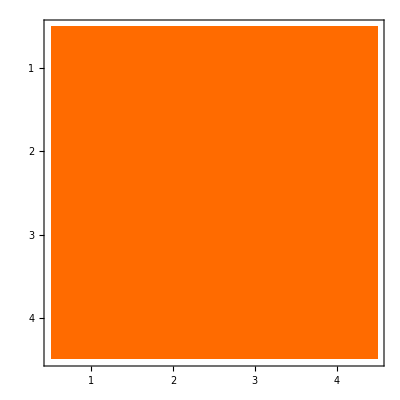
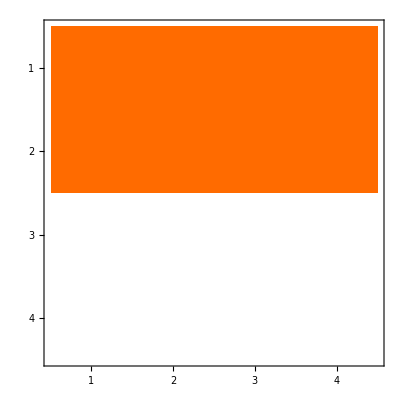
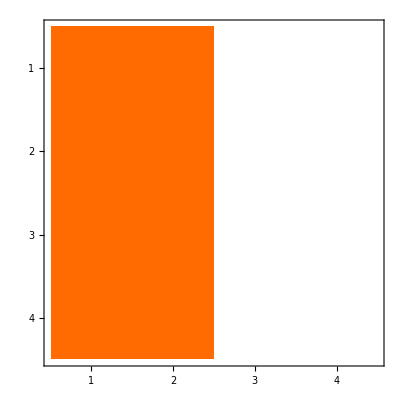
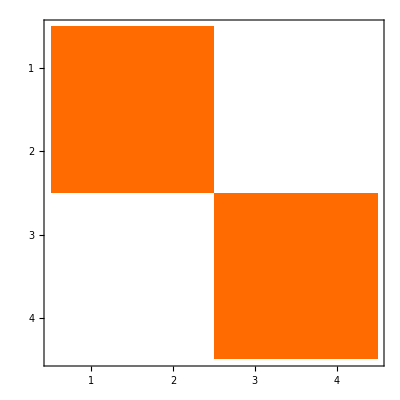
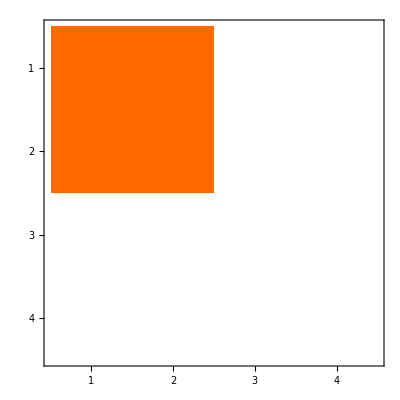
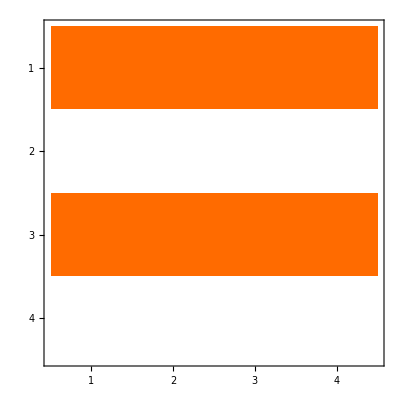
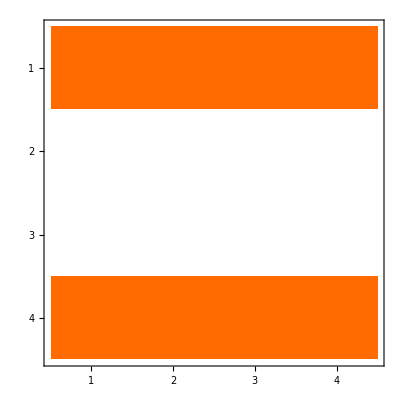
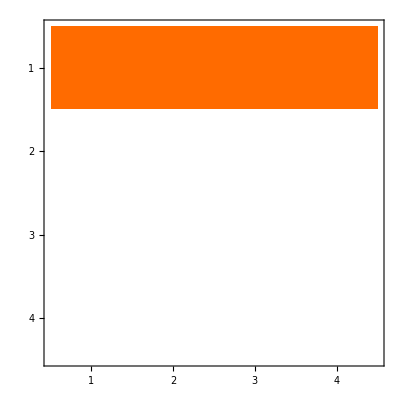
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
Grid[tab[[All,{2,4}]],Frame->All]
```

### Failing minors example 1

```mathematica
badchannel={1,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0};Partition[badchannel,4]//MatrixPlot
```

-Graphics-

```mathematica
important={{1,{0.125,0.}},{2,{0.,0.015625,0.01171875,-0.00390625}},{3,{0.,0.001953125,0.00146484375,0.0009765625,-0.00048828125}},{4,{0.,0.000244140625,0.00018310546875,0.0001220703125,-0.00006103515625,-0.0000457763671875,0.0001373291015625,0.0000152587890625}},{5,{0.,0.0000152587890625,-7.62939453125*^-6,-5.7220458984375*^-6,-3.814697265625*^-6,0.000011444091796875,1.9073486328125*^-6}},{6,{0.,-9.5367431640625*^-7,-7.152557373046875*^-7,-4.76837158203125*^-7,9.5367431640625*^-7,-5.364418029785156*^-7,2.384185791015625*^-7,1.7881393432617188*^-7}},{7,{0.,-5.960464477539063*^-8,-4.470348358154297*^-8,2.9802322387695312*^-8,2.2351741790771484*^-8,1.4901161193847656*^-8}},{8,{0.,-3.725290298461914*^-9,3.725290298461914*^-9,2.7939677238464355*^-9,1.862645149230957*^-9,2.0954757928848267*^-9}},{9,{0.,2.3283064365386963*^-10,1.7462298274040222*^-10}},{10,{0.,1.4551915228366852*^-11}},{11,{0.}},{12,{0.}},{13,{0.}},{14,{0.}},{15,{0.}},{16,{0.}}};
```

```mathematica
badchoi=1.0*ChoiJamiStateFromPauliProductBasis[DiagonalMatrix[badchannel]];
```

```mathematica
important=Table[{i,Principalminors[badchoi,{i}]},{i,1,16}];
```

```mathematica
important=%;
```

```mathematica
important//Chop//TableForm
```

1 | 0.125
0
2 | 0
0.015625
0.0117188
-0.00390625
3 | 0
0.00195313
0.00146484
0.000976563
-0.000488281
4 | 0
0.000244141
0.000183105
0.00012207
-0.0000610352
-0.0000457764
0.000137329
0.0000152588
5 | 0
0.0000152588
-7.62939×10^-6
-5.72205×10^-6
-3.8147×10^-6
0.0000114441
1.90735×10^-6
6 | 0
-9.53674×10^-7
-7.15256×10^-7
-4.76837×10^-7
9.53674×10^-7
-5.36442×10^-7
2.38419×10^-7
1.78814×10^-7
7 | 0
-5.96046×10^-8
-4.47035×10^-8
2.98023×10^-8
2.23517×10^-8
1.49012×10^-8
8 | 0
-3.72529×10^-9
3.72529×10^-9
2.79397×10^-9
1.86265×10^-9
2.09548×10^-9
9 | 0
2.32831×10^-10
1.74623×10^-10
10 | 0
0
11 | 0
12 | 0
13 | 0
14 | 0
15 | 0
16 | 0

### Failing minors example 2

```mathematica
badchannel={1,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0};Partition[badchannel,4]//MatrixPlot
```

-Graphics-

```mathematica
important2={{1,{0.125,0.}},{2,{0.,0.015625,0.01171875,-0.00390625}},{3,{0.,0.001953125,0.00146484375,-0.00048828125}},{4,{0.,0.000244140625,0.00018310546875,-0.00006103515625,-0.0000457763671875,0.0001373291015625,0.0000152587890625}},{5,{0.,0.00002288818359375,-7.62939453125*^-6,-5.7220458984375*^-6,0.0000171661376953125,1.9073486328125*^-6}},{6,{0.,-9.5367431640625*^-7,-7.152557373046875*^-7,2.1457672119140625*^-6,-5.364418029785156*^-7,2.384185791015625*^-7,1.7881393432617188*^-7,-5.960464477539063*^-8,1.6093254089355469*^-6}},{7,{0.,-8.940696716308594*^-8,-6.705522537231445*^-8,2.9802322387695312*^-8,2.2351741790771484*^-8,-7.450580596923828*^-9,2.0116567611694336*^-7}},{8,{0.,-8.381903171539307*^-9,3.725290298461914*^-9,2.7939677238464355*^-9,2.0954757928848267*^-9,-9.313225746154785*^-10,-6.984919309616089*^-10,-6.28642737865448*^-9,2.3283064365386963*^-10,1.885928213596344*^-8}},{9,{0.,3.4924596548080444*^-10,2.6193447411060333*^-10,-1.1641532182693481*^-10,-8.731149137020111*^-11,-7.8580342233181*^-10,2.9103830456733704*^-11}},{10,{0.,3.2741809263825417*^-11,-1.4551915228366852*^-11,-1.0913936421275139*^-11,-8.185452315956354*^-12,2.4556356947869062*^-11,3.637978807091713*^-12,2.7284841053187847*^-12,-7.366907084360719*^-11}},{11,{0.,-1.3642420526593924*^-12,-1.0231815394945443*^-12,3.069544618483633*^-12,4.547473508864641*^-13,3.410605131648481*^-13}},{12,{0.,-1.2789769243681803*^-13,-9.592326932761353*^-14,5.684341886080802*^-14,4.263256414560601*^-14,3.197442310920451*^-14,2.877698079828406*^-13}},{13,{0.,-1.199040866595169*^-14,5.329070518200751*^-15,3.9968028886505635*^-15}},{14,{0.,4.996003610813204*^-16,3.7470027081099033*^-16,-1.124100812432971*^-15}},{15,{4.683753385137379*^-17,0.}},{16,{4.391018798566293*^-18}}};
```

```mathematica
badchoi=1.0*ChoiJamiStateFromPauliProductBasis[DiagonalMatrix[badchannel]];
```

```mathematica
important2=Table[{i,Principalminors[badchoi,{i}]},{i,1,16}];
```

```mathematica
important2//Chop//TableForm
```

1 | 0.125
0
2 | 0
0.015625
0.0117188
-0.00390625
3 | 0
0.00195313
0.00146484
-0.000488281
4 | 0
0.000244141
0.000183105
-0.0000610352
-0.0000457764
0.000137329
0.0000152588
5 | 0
0.0000228882
-7.62939×10^-6
-5.72205×10^-6
0.0000171661
1.90735×10^-6
6 | 0
-9.53674×10^-7
-7.15256×10^-7
2.14577×10^-6
-5.36442×10^-7
2.38419×10^-7
1.78814×10^-7
-5.96046×10^-8
1.60933×10^-6
7 | 0
-8.9407×10^-8
-6.70552×10^-8
2.98023×10^-8
2.23517×10^-8
-7.45058×10^-9
2.01166×10^-7
8 | 0
-8.3819×10^-9
3.72529×10^-9
2.79397×10^-9
2.09548×10^-9
-9.31323×10^-10
-6.98492×10^-10
-6.28643×10^-9
2.32831×10^-10
1.88593×10^-8
9 | 0
3.49246×10^-10
2.61934×10^-10
-1.16415×10^-10
0
-7.85803×10^-10
0
10 | 0
0
0
0
0
0
0
0
0
11 | 0
0
0
0
0
0
12 | 0
0
0
0
0
0
0
13 | 0
0
0
0
14 | 0
0
0
0
15 | 0
0
16 | 0

### Principal minors testing three qubits

```mathematica
Sum[Binomial[2^8,i],{i,1,2^8}]
```

115792089237316195423570985008687907853269984665640564039457584007913129639935

```mathematica
Principalminors[mat_,r_]:=DeleteDuplicates[Flatten[Diagonal[Map[Reverse,Minors[mat, #], {0, 1}]] & /@ r]];
```

```mathematica
Subscript[r, 0,0,0]=1;diag=Table[Subscript[r, i,j,k],{i,0,3},{j,0,3},{k,0,3}]//Flatten;
```

```mathematica
diag//Length
```

64

```mathematica
2^(2*3)
```

64

```mathematica
choi=2^(2*3)*ChoiJamiStateFromPauliProductBasis[DiagonalMatrix[diag]]//Expand//FullSimplify;
```

```mathematica
choi//Expand//FullSimplify//MatrixForm
```

(1)
 |  |  |  |

```mathematica
Principalminors[choi,{1}]//Expand//Transpose//TableForm
```

1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3)
1-r_(0,0,3)+r_(0,3,0)-r_(0,3,3)+r_(3,0,0)-r_(3,0,3)+r_(3,3,0)-r_(3,3,3)
1+r_(0,0,3)-r_(0,3,0)-r_(0,3,3)+r_(3,0,0)+r_(3,0,3)-r_(3,3,0)-r_(3,3,3)
1-r_(0,0,3)-r_(0,3,0)+r_(0,3,3)+r_(3,0,0)-r_(3,0,3)-r_(3,3,0)+r_(3,3,3)
1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)-r_(3,0,0)-r_(3,0,3)-r_(3,3,0)-r_(3,3,3)
1-r_(0,0,3)+r_(0,3,0)-r_(0,3,3)-r_(3,0,0)+r_(3,0,3)-r_(3,3,0)+r_(3,3,3)
1+r_(0,0,3)-r_(0,3,0)-r_(0,3,3)-r_(3,0,0)-r_(3,0,3)+r_(3,3,0)+r_(3,3,3)
1-r_(0,0,3)-r_(0,3,0)+r_(0,3,3)-r_(3,0,0)+r_(3,0,3)+r_(3,3,0)-r_(3,3,3)

```mathematica
%//Length
```

```mathematica
Principalminors[choi,{2}]//DeleteDuplicates//FullSimplify//Transpose//TableForm
```

-((-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)-r_(3,0,0)+r_(3,0,3)-r_(3,3,0)+r_(3,3,3)) (1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3)))
(1+r_(0,0,3)-r_(0,3,0)-r_(0,3,3)+r_(3,0,0)+r_(3,0,3)-r_(3,3,0)-r_(3,3,3)) (1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3))
-((1+r_(0,0,3)-r_(0,3,0)-r_(0,3,3)+r_(3,0,0)+r_(3,0,3)-r_(3,3,0)-r_(3,3,3)) (-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)-r_(3,0,0)+r_(3,0,3)-r_(3,3,0)+r_(3,3,3)))
-((-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)-r_(3,0,0)+r_(3,0,3)+r_(3,3,0)-r_(3,3,3)) (1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3)))
(-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)-r_(3,0,0)+r_(3,0,3)+r_(3,3,0)-r_(3,3,3)) (-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)-r_(3,0,0)+r_(3,0,3)-r_(3,3,0)+r_(3,3,3))
-((1+r_(0,0,3)-r_(0,3,0)-r_(0,3,3)+r_(3,0,0)+r_(3,0,3)-r_(3,3,0)-r_(3,3,3)) (-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)-r_(3,0,0)+r_(3,0,3)+r_(3,3,0)-r_(3,3,3)))
(1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)-r_(3,0,0)-r_(3,0,3)-r_(3,3,0)-r_(3,3,3)) (1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3))
-((1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)-r_(3,0,0)-r_(3,0,3)-r_(3,3,0)-r_(3,3,3)) (-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)-r_(3,0,0)+r_(3,0,3)-r_(3,3,0)+r_(3,3,3)))
(1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)-r_(3,0,0)-r_(3,0,3)-r_(3,3,0)-r_(3,3,3)) (1+r_(0,0,3)-r_(0,3,0)-r_(0,3,3)+r_(3,0,0)+r_(3,0,3)-r_(3,3,0)-r_(3,3,3))
-((1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)-r_(3,0,0)-r_(3,0,3)-r_(3,3,0)-r_(3,3,3)) (-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)-r_(3,0,0)+r_(3,0,3)+r_(3,3,0)-r_(3,3,3)))
-((-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)+r_(3,0,0)-r_(3,0,3)+r_(3,3,0)-r_(3,3,3)) (1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3)))
(-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)+r_(3,0,0)-r_(3,0,3)+r_(3,3,0)-r_(3,3,3)) (-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)-r_(3,0,0)+r_(3,0,3)-r_(3,3,0)+r_(3,3,3))
-((1+r_(0,0,3)-r_(0,3,0)-r_(0,3,3)+r_(3,0,0)+r_(3,0,3)-r_(3,3,0)-r_(3,3,3)) (-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)+r_(3,0,0)-r_(3,0,3)+r_(3,3,0)-r_(3,3,3)))
(-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)+r_(3,0,0)-r_(3,0,3)+r_(3,3,0)-r_(3,3,3)) (-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)-r_(3,0,0)+r_(3,0,3)+r_(3,3,0)-r_(3,3,3))
-((1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)-r_(3,0,0)-r_(3,0,3)-r_(3,3,0)-r_(3,3,3)) (-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)+r_(3,0,0)-r_(3,0,3)+r_(3,3,0)-r_(3,3,3)))
(1+r_(0,0,3)-r_(0,3,0)-r_(0,3,3)-r_(3,0,0)-r_(3,0,3)+r_(3,3,0)+r_(3,3,3)) (1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3))
-((-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)-r_(3,0,0)+r_(3,0,3)-r_(3,3,0)+r_(3,3,3)) (1+r_(0,0,3)-r_(0,3,0)-r_(0,3,3)-r_(3,0,0)-r_(3,0,3)+r_(3,3,0)+r_(3,3,3)))
(1+r_(0,0,3)-r_(0,3,0)-r_(0,3,3)+r_(3,0,0)+r_(3,0,3)-r_(3,3,0)-r_(3,3,3)) (1+r_(0,0,3)-r_(0,3,0)-r_(0,3,3)-r_(3,0,0)-r_(3,0,3)+r_(3,3,0)+r_(3,3,3))
-((-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)-r_(3,0,0)+r_(3,0,3)+r_(3,3,0)-r_(3,3,3)) (1+r_(0,0,3)-r_(0,3,0)-r_(0,3,3)-r_(3,0,0)-r_(3,0,3)+r_(3,3,0)+r_(3,3,3)))
(1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)-r_(3,0,0)-r_(3,0,3)-r_(3,3,0)-r_(3,3,3)) (1+r_(0,0,3)-r_(0,3,0)-r_(0,3,3)-r_(3,0,0)-r_(3,0,3)+r_(3,3,0)+r_(3,3,3))
-((-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)+r_(3,0,0)-r_(3,0,3)+r_(3,3,0)-r_(3,3,3)) (1+r_(0,0,3)-r_(0,3,0)-r_(0,3,3)-r_(3,0,0)-r_(3,0,3)+r_(3,3,0)+r_(3,3,3)))
-((-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)+r_(3,0,0)-r_(3,0,3)-r_(3,3,0)+r_(3,3,3)) (1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3)))
(-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)+r_(3,0,0)-r_(3,0,3)-r_(3,3,0)+r_(3,3,3)) (-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)-r_(3,0,0)+r_(3,0,3)-r_(3,3,0)+r_(3,3,3))
-((1+r_(0,0,3)-r_(0,3,0)-r_(0,3,3)+r_(3,0,0)+r_(3,0,3)-r_(3,3,0)-r_(3,3,3)) (-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)+r_(3,0,0)-r_(3,0,3)-r_(3,3,0)+r_(3,3,3)))
(-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)-r_(3,0,0)+r_(3,0,3)+r_(3,3,0)-r_(3,3,3)) (-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)+r_(3,0,0)-r_(3,0,3)-r_(3,3,0)+r_(3,3,3))
-((1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)-r_(3,0,0)-r_(3,0,3)-r_(3,3,0)-r_(3,3,3)) (-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)+r_(3,0,0)-r_(3,0,3)-r_(3,3,0)+r_(3,3,3)))
(-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)+r_(3,0,0)-r_(3,0,3)+r_(3,3,0)-r_(3,3,3)) (-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)+r_(3,0,0)-r_(3,0,3)-r_(3,3,0)+r_(3,3,3))
-((-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)+r_(3,0,0)-r_(3,0,3)-r_(3,3,0)+r_(3,3,3)) (1+r_(0,0,3)-r_(0,3,0)-r_(0,3,3)-r_(3,0,0)-r_(3,0,3)+r_(3,3,0)+r_(3,3,3)))
-(r_(0,0,1)-r_(0,0,2)+r_(0,3,1)-r_(0,3,2)+r_(3,0,1)-r_(3,0,2)+r_(3,3,1)-r_(3,3,2))^2+(-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)-r_(3,0,0)+r_(3,0,3)-r_(3,3,0)+r_(3,3,3))^2
-(r_(0,0,1)+r_(0,0,2)+r_(0,3,1)+r_(0,3,2)+r_(3,0,1)+r_(3,0,2)+r_(3,3,1)+r_(3,3,2))^2+(1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(0,0,1)-r_(0,0,2)-r_(0,3,1)+r_(0,3,2)+r_(3,0,1)-r_(3,0,2)-r_(3,3,1)+r_(3,3,2))^2+(-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)-r_(3,0,0)+r_(3,0,3)+r_(3,3,0)-r_(3,3,3))^2
-(r_(0,0,1)+r_(0,0,2)-r_(0,3,1)-r_(0,3,2)+r_(3,0,1)+r_(3,0,2)-r_(3,3,1)-r_(3,3,2))^2+(-1-r_(0,0,3)+r_(0,3,0)+r_(0,3,3)-r_(3,0,0)-r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(0,0,1)-r_(0,0,2)+r_(0,3,1)-r_(0,3,2)-r_(3,0,1)+r_(3,0,2)-r_(3,3,1)+r_(3,3,2))^2+(-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)+r_(3,0,0)-r_(3,0,3)+r_(3,3,0)-r_(3,3,3))^2
-(r_(0,0,1)+r_(0,0,2)+r_(0,3,1)+r_(0,3,2)-r_(3,0,1)-r_(3,0,2)-r_(3,3,1)-r_(3,3,2))^2+(-1-r_(0,0,3)-r_(0,3,0)-r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(0,0,1)-r_(0,0,2)-r_(0,3,1)+r_(0,3,2)-r_(3,0,1)+r_(3,0,2)+r_(3,3,1)-r_(3,3,2))^2+(-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)+r_(3,0,0)-r_(3,0,3)-r_(3,3,0)+r_(3,3,3))^2
-(r_(0,0,1)+r_(0,0,2)-r_(0,3,1)-r_(0,3,2)-r_(3,0,1)-r_(3,0,2)+r_(3,3,1)+r_(3,3,2))^2+(-1-r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)-r_(3,3,0)-r_(3,3,3))^2
-(r_(0,1,0)+r_(0,1,3)-r_(0,2,0)-r_(0,2,3)+r_(3,1,0)+r_(3,1,3)-r_(3,2,0)-r_(3,2,3))^2+(-1-r_(0,0,3)+r_(0,3,0)+r_(0,3,3)-r_(3,0,0)-r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(0,1,1)+r_(0,1,2)-r_(0,2,1)-r_(0,2,2)+r_(3,1,1)+r_(3,1,2)-r_(3,2,1)-r_(3,2,2))^2+(-1-r_(0,0,3)+r_(0,3,0)+r_(0,3,3)-r_(3,0,0)-r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(0,1,0)-r_(0,1,3)-r_(0,2,0)+r_(0,2,3)+r_(3,1,0)-r_(3,1,3)-r_(3,2,0)+r_(3,2,3))^2+(-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)-r_(3,0,0)+r_(3,0,3)+r_(3,3,0)-r_(3,3,3))^2
-(r_(0,1,1)-r_(0,1,2)-r_(0,2,1)+r_(0,2,2)+r_(3,1,1)-r_(3,1,2)-r_(3,2,1)+r_(3,2,2))^2+(-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)-r_(3,0,0)+r_(3,0,3)+r_(3,3,0)-r_(3,3,3))^2
-(r_(0,1,0)+r_(0,1,3)+r_(0,2,0)+r_(0,2,3)+r_(3,1,0)+r_(3,1,3)+r_(3,2,0)+r_(3,2,3))^2+(1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(0,1,1)+r_(0,1,2)+r_(0,2,1)+r_(0,2,2)+r_(3,1,1)+r_(3,1,2)+r_(3,2,1)+r_(3,2,2))^2+(1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(0,1,0)-r_(0,1,3)+r_(0,2,0)-r_(0,2,3)+r_(3,1,0)-r_(3,1,3)+r_(3,2,0)-r_(3,2,3))^2+(-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)-r_(3,0,0)+r_(3,0,3)-r_(3,3,0)+r_(3,3,3))^2
-(r_(0,1,1)-r_(0,1,2)+r_(0,2,1)-r_(0,2,2)+r_(3,1,1)-r_(3,1,2)+r_(3,2,1)-r_(3,2,2))^2+(-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)-r_(3,0,0)+r_(3,0,3)-r_(3,3,0)+r_(3,3,3))^2
-(r_(0,1,0)+r_(0,1,3)-r_(0,2,0)-r_(0,2,3)-r_(3,1,0)-r_(3,1,3)+r_(3,2,0)+r_(3,2,3))^2+(-1-r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)-r_(3,3,0)-r_(3,3,3))^2
-(r_(0,1,1)+r_(0,1,2)-r_(0,2,1)-r_(0,2,2)-r_(3,1,1)-r_(3,1,2)+r_(3,2,1)+r_(3,2,2))^2+(-1-r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)-r_(3,3,0)-r_(3,3,3))^2
-(r_(0,1,0)-r_(0,1,3)-r_(0,2,0)+r_(0,2,3)-r_(3,1,0)+r_(3,1,3)+r_(3,2,0)-r_(3,2,3))^2+(-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)+r_(3,0,0)-r_(3,0,3)-r_(3,3,0)+r_(3,3,3))^2
-(r_(0,1,1)-r_(0,1,2)-r_(0,2,1)+r_(0,2,2)-r_(3,1,1)+r_(3,1,2)+r_(3,2,1)-r_(3,2,2))^2+(-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)+r_(3,0,0)-r_(3,0,3)-r_(3,3,0)+r_(3,3,3))^2
-(r_(0,1,0)+r_(0,1,3)+r_(0,2,0)+r_(0,2,3)-r_(3,1,0)-r_(3,1,3)-r_(3,2,0)-r_(3,2,3))^2+(-1-r_(0,0,3)-r_(0,3,0)-r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(0,1,1)+r_(0,1,2)+r_(0,2,1)+r_(0,2,2)-r_(3,1,1)-r_(3,1,2)-r_(3,2,1)-r_(3,2,2))^2+(-1-r_(0,0,3)-r_(0,3,0)-r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(0,1,0)-r_(0,1,3)+r_(0,2,0)-r_(0,2,3)-r_(3,1,0)+r_(3,1,3)-r_(3,2,0)+r_(3,2,3))^2+(-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)+r_(3,0,0)-r_(3,0,3)+r_(3,3,0)-r_(3,3,3))^2
-(r_(0,1,1)-r_(0,1,2)+r_(0,2,1)-r_(0,2,2)-r_(3,1,1)+r_(3,1,2)-r_(3,2,1)+r_(3,2,2))^2+(-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)+r_(3,0,0)-r_(3,0,3)+r_(3,3,0)-r_(3,3,3))^2
-(r_(1,0,0)+r_(1,0,3)+r_(1,3,0)+r_(1,3,3)-r_(2,0,0)-r_(2,0,3)-r_(2,3,0)-r_(2,3,3))^2+(-1-r_(0,0,3)-r_(0,3,0)-r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(1,0,1)+r_(1,0,2)+r_(1,3,1)+r_(1,3,2)-r_(2,0,1)-r_(2,0,2)-r_(2,3,1)-r_(2,3,2))^2+(-1-r_(0,0,3)-r_(0,3,0)-r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(1,1,0)+r_(1,1,3)+r_(1,2,0)+r_(1,2,3)-r_(2,1,0)-r_(2,1,3)-r_(2,2,0)-r_(2,2,3))^2+(-1-r_(0,0,3)-r_(0,3,0)-r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(1,1,1)+r_(1,1,2)+r_(1,2,1)+r_(1,2,2)-r_(2,1,1)-r_(2,1,2)-r_(2,2,1)-r_(2,2,2))^2+(-1-r_(0,0,3)-r_(0,3,0)-r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(1,0,0)-r_(1,0,3)+r_(1,3,0)-r_(1,3,3)-r_(2,0,0)+r_(2,0,3)-r_(2,3,0)+r_(2,3,3))^2+(-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)+r_(3,0,0)-r_(3,0,3)+r_(3,3,0)-r_(3,3,3))^2
-(r_(1,0,1)-r_(1,0,2)+r_(1,3,1)-r_(1,3,2)-r_(2,0,1)+r_(2,0,2)-r_(2,3,1)+r_(2,3,2))^2+(-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)+r_(3,0,0)-r_(3,0,3)+r_(3,3,0)-r_(3,3,3))^2
-(r_(1,1,0)-r_(1,1,3)+r_(1,2,0)-r_(1,2,3)-r_(2,1,0)+r_(2,1,3)-r_(2,2,0)+r_(2,2,3))^2+(-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)+r_(3,0,0)-r_(3,0,3)+r_(3,3,0)-r_(3,3,3))^2
-(r_(1,1,1)-r_(1,1,2)+r_(1,2,1)-r_(1,2,2)-r_(2,1,1)+r_(2,1,2)-r_(2,2,1)+r_(2,2,2))^2+(-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)+r_(3,0,0)-r_(3,0,3)+r_(3,3,0)-r_(3,3,3))^2
-(r_(1,0,0)+r_(1,0,3)-r_(1,3,0)-r_(1,3,3)-r_(2,0,0)-r_(2,0,3)+r_(2,3,0)+r_(2,3,3))^2+(-1-r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)-r_(3,3,0)-r_(3,3,3))^2
-(r_(1,0,1)+r_(1,0,2)-r_(1,3,1)-r_(1,3,2)-r_(2,0,1)-r_(2,0,2)+r_(2,3,1)+r_(2,3,2))^2+(-1-r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)-r_(3,3,0)-r_(3,3,3))^2
-(r_(1,1,0)+r_(1,1,3)-r_(1,2,0)-r_(1,2,3)-r_(2,1,0)-r_(2,1,3)+r_(2,2,0)+r_(2,2,3))^2+(-1-r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)-r_(3,3,0)-r_(3,3,3))^2
-(r_(1,1,1)+r_(1,1,2)-r_(1,2,1)-r_(1,2,2)-r_(2,1,1)-r_(2,1,2)+r_(2,2,1)+r_(2,2,2))^2+(-1-r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)-r_(3,3,0)-r_(3,3,3))^2
-(r_(1,0,0)-r_(1,0,3)-r_(1,3,0)+r_(1,3,3)-r_(2,0,0)+r_(2,0,3)+r_(2,3,0)-r_(2,3,3))^2+(-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)+r_(3,0,0)-r_(3,0,3)-r_(3,3,0)+r_(3,3,3))^2
-(r_(1,0,1)-r_(1,0,2)-r_(1,3,1)+r_(1,3,2)-r_(2,0,1)+r_(2,0,2)+r_(2,3,1)-r_(2,3,2))^2+(-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)+r_(3,0,0)-r_(3,0,3)-r_(3,3,0)+r_(3,3,3))^2
-(r_(1,1,0)-r_(1,1,3)-r_(1,2,0)+r_(1,2,3)-r_(2,1,0)+r_(2,1,3)+r_(2,2,0)-r_(2,2,3))^2+(-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)+r_(3,0,0)-r_(3,0,3)-r_(3,3,0)+r_(3,3,3))^2
-(r_(1,1,1)-r_(1,1,2)-r_(1,2,1)+r_(1,2,2)-r_(2,1,1)+r_(2,1,2)+r_(2,2,1)-r_(2,2,2))^2+(-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)+r_(3,0,0)-r_(3,0,3)-r_(3,3,0)+r_(3,3,3))^2
-(r_(1,0,0)+r_(1,0,3)+r_(1,3,0)+r_(1,3,3)+r_(2,0,0)+r_(2,0,3)+r_(2,3,0)+r_(2,3,3))^2+(1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(1,0,1)+r_(1,0,2)+r_(1,3,1)+r_(1,3,2)+r_(2,0,1)+r_(2,0,2)+r_(2,3,1)+r_(2,3,2))^2+(1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(1,1,0)+r_(1,1,3)+r_(1,2,0)+r_(1,2,3)+r_(2,1,0)+r_(2,1,3)+r_(2,2,0)+r_(2,2,3))^2+(1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(1,1,1)+r_(1,1,2)+r_(1,2,1)+r_(1,2,2)+r_(2,1,1)+r_(2,1,2)+r_(2,2,1)+r_(2,2,2))^2+(1+r_(0,0,3)+r_(0,3,0)+r_(0,3,3)+r_(3,0,0)+r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(1,0,0)-r_(1,0,3)+r_(1,3,0)-r_(1,3,3)+r_(2,0,0)-r_(2,0,3)+r_(2,3,0)-r_(2,3,3))^2+(-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)-r_(3,0,0)+r_(3,0,3)-r_(3,3,0)+r_(3,3,3))^2
-(r_(1,0,1)-r_(1,0,2)+r_(1,3,1)-r_(1,3,2)+r_(2,0,1)-r_(2,0,2)+r_(2,3,1)-r_(2,3,2))^2+(-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)-r_(3,0,0)+r_(3,0,3)-r_(3,3,0)+r_(3,3,3))^2
-(r_(1,1,0)-r_(1,1,3)+r_(1,2,0)-r_(1,2,3)+r_(2,1,0)-r_(2,1,3)+r_(2,2,0)-r_(2,2,3))^2+(-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)-r_(3,0,0)+r_(3,0,3)-r_(3,3,0)+r_(3,3,3))^2
-(r_(1,1,1)-r_(1,1,2)+r_(1,2,1)-r_(1,2,2)+r_(2,1,1)-r_(2,1,2)+r_(2,2,1)-r_(2,2,2))^2+(-1+r_(0,0,3)-r_(0,3,0)+r_(0,3,3)-r_(3,0,0)+r_(3,0,3)-r_(3,3,0)+r_(3,3,3))^2
-(r_(1,0,0)+r_(1,0,3)-r_(1,3,0)-r_(1,3,3)+r_(2,0,0)+r_(2,0,3)-r_(2,3,0)-r_(2,3,3))^2+(-1-r_(0,0,3)+r_(0,3,0)+r_(0,3,3)-r_(3,0,0)-r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(1,0,1)+r_(1,0,2)-r_(1,3,1)-r_(1,3,2)+r_(2,0,1)+r_(2,0,2)-r_(2,3,1)-r_(2,3,2))^2+(-1-r_(0,0,3)+r_(0,3,0)+r_(0,3,3)-r_(3,0,0)-r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(1,1,0)+r_(1,1,3)-r_(1,2,0)-r_(1,2,3)+r_(2,1,0)+r_(2,1,3)-r_(2,2,0)-r_(2,2,3))^2+(-1-r_(0,0,3)+r_(0,3,0)+r_(0,3,3)-r_(3,0,0)-r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(1,1,1)+r_(1,1,2)-r_(1,2,1)-r_(1,2,2)+r_(2,1,1)+r_(2,1,2)-r_(2,2,1)-r_(2,2,2))^2+(-1-r_(0,0,3)+r_(0,3,0)+r_(0,3,3)-r_(3,0,0)-r_(3,0,3)+r_(3,3,0)+r_(3,3,3))^2
-(r_(1,0,0)-r_(1,0,3)-r_(1,3,0)+r_(1,3,3)+r_(2,0,0)-r_(2,0,3)-r_(2,3,0)+r_(2,3,3))^2+(-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)-r_(3,0,0)+r_(3,0,3)+r_(3,3,0)-r_(3,3,3))^2
-(r_(1,0,1)-r_(1,0,2)-r_(1,3,1)+r_(1,3,2)+r_(2,0,1)-r_(2,0,2)-r_(2,3,1)+r_(2,3,2))^2+(-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)-r_(3,0,0)+r_(3,0,3)+r_(3,3,0)-r_(3,3,3))^2
-(r_(1,1,0)-r_(1,1,3)-r_(1,2,0)+r_(1,2,3)+r_(2,1,0)-r_(2,1,3)-r_(2,2,0)+r_(2,2,3))^2+(-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)-r_(3,0,0)+r_(3,0,3)+r_(3,3,0)-r_(3,3,3))^2
-(r_(1,1,1)-r_(1,1,2)-r_(1,2,1)+r_(1,2,2)+r_(2,1,1)-r_(2,1,2)-r_(2,2,1)+r_(2,2,2))^2+(-1+r_(0,0,3)+r_(0,3,0)-r_(0,3,3)-r_(3,0,0)+r_(3,0,3)+r_(3,3,0)-r_(3,3,3))^2

## Lindblad generator approach

```mathematica
L={0}~Join~Table[-Subscript[μ, i]t,{i,1,15}]//DiagonalMatrix;
```

```mathematica
ωort=IdentityMatrix[16]-Proyector[Bell[4]];
```

```mathematica
set=16*ωort.ChoiJamiStateFromPauliProductBasis[L].ωort//Eigenvalues
```

{0,-t (μ_1+μ_2+μ_3+μ_4+μ_5+μ_6+μ_7-μ_8-μ_9-μ_10-μ_11-μ_12-μ_13-μ_14-μ_15),-t (μ_1+μ_2+μ_3-μ_4-μ_5-μ_6-μ_7+μ_8+μ_9+μ_10+μ_11-μ_12-μ_13-μ_14-μ_15),-t (μ_1-μ_2-μ_3+μ_4+μ_5-μ_6-μ_7+μ_8+μ_9-μ_10-μ_11+μ_12+μ_13-μ_14-μ_15),-t (μ_1-μ_2-μ_3-μ_4-μ_5+μ_6+μ_7-μ_8-μ_9+μ_10+μ_11+μ_12+μ_13-μ_14-μ_15),t (μ_1-μ_2+μ_3-μ_4+μ_5-μ_6+μ_7+μ_8-μ_9+μ_10-μ_11+μ_12-μ_13+μ_14-μ_15),t (μ_1-μ_2+μ_3+μ_4-μ_5+μ_6-μ_7-μ_8+μ_9-μ_10+μ_11+μ_12-μ_13+μ_14-μ_15),t (μ_1+μ_2-μ_3-μ_4+μ_5+μ_6-μ_7-μ_8+μ_9+μ_10-μ_11-μ_12+μ_13+μ_14-μ_15),t (μ_1+μ_2-μ_3+μ_4-μ_5-μ_6+μ_7+μ_8-μ_9-μ_10+μ_11-μ_12+μ_13+μ_14-μ_15),t (μ_1+μ_2-μ_3+μ_4-μ_5-μ_6+μ_7-μ_8+μ_9+μ_10-μ_11+μ_12-μ_13-μ_14+μ_15),t (μ_1+μ_2-μ_3-μ_4+μ_5+μ_6-μ_7+μ_8-μ_9-μ_10+μ_11+μ_12-μ_13-μ_14+μ_15),t (μ_1-μ_2+μ_3+μ_4-μ_5+μ_6-μ_7+μ_8-μ_9+μ_10-μ_11-μ_12+μ_13-μ_14+μ_15),t (μ_1-μ_2+μ_3-μ_4+μ_5-μ_6+μ_7-μ_8+μ_9-μ_10+μ_11-μ_12+μ_13-μ_14+μ_15),-t (μ_1-μ_2-μ_3-μ_4-μ_5+μ_6+μ_7+μ_8+μ_9-μ_10-μ_11-μ_12-μ_13+μ_14+μ_15),-t (μ_1-μ_2-μ_3+μ_4+μ_5-μ_6-μ_7-μ_8-μ_9+μ_10+μ_11-μ_12-μ_13+μ_14+μ_15),-t (μ_1+μ_2+μ_3-μ_4-μ_5-μ_6-μ_7-μ_8-μ_9-μ_10-μ_11+μ_12+μ_13+μ_14+μ_15)}

```mathematica
set2=set/t;set2//FullSimplify//TableForm
```

0
-μ_1-μ_2-μ_3-μ_4-μ_5-μ_6-μ_7+μ_8+μ_9+μ_10+μ_11+μ_12+μ_13+μ_14+μ_15
-μ_1-μ_2-μ_3+μ_4+μ_5+μ_6+μ_7-μ_8-μ_9-μ_10-μ_11+μ_12+μ_13+μ_14+μ_15
-μ_1+μ_2+μ_3-μ_4-μ_5+μ_6+μ_7-μ_8-μ_9+μ_10+μ_11-μ_12-μ_13+μ_14+μ_15
-μ_1+μ_2+μ_3+μ_4+μ_5-μ_6-μ_7+μ_8+μ_9-μ_10-μ_11-μ_12-μ_13+μ_14+μ_15
μ_1-μ_2+μ_3-μ_4+μ_5-μ_6+μ_7+μ_8-μ_9+μ_10-μ_11+μ_12-μ_13+μ_14-μ_15
μ_1-μ_2+μ_3+μ_4-μ_5+μ_6-μ_7-μ_8+μ_9-μ_10+μ_11+μ_12-μ_13+μ_14-μ_15
μ_1+μ_2-μ_3-μ_4+μ_5+μ_6-μ_7-μ_8+μ_9+μ_10-μ_11-μ_12+μ_13+μ_14-μ_15
μ_1+μ_2-μ_3+μ_4-μ_5-μ_6+μ_7+μ_8-μ_9-μ_10+μ_11-μ_12+μ_13+μ_14-μ_15
μ_1+μ_2-μ_3+μ_4-μ_5-μ_6+μ_7-μ_8+μ_9+μ_10-μ_11+μ_12-μ_13-μ_14+μ_15
μ_1+μ_2-μ_3-μ_4+μ_5+μ_6-μ_7+μ_8-μ_9-μ_10+μ_11+μ_12-μ_13-μ_14+μ_15
μ_1-μ_2+μ_3+μ_4-μ_5+μ_6-μ_7+μ_8-μ_9+μ_10-μ_11-μ_12+μ_13-μ_14+μ_15
μ_1-μ_2+μ_3-μ_4+μ_5-μ_6+μ_7-μ_8+μ_9-μ_10+μ_11-μ_12+μ_13-μ_14+μ_15
-μ_1+μ_2+μ_3+μ_4+μ_5-μ_6-μ_7-μ_8-μ_9+μ_10+μ_11+μ_12+μ_13-μ_14-μ_15
-μ_1+μ_2+μ_3-μ_4-μ_5+μ_6+μ_7+μ_8+μ_9-μ_10-μ_11+μ_12+μ_13-μ_14-μ_15
-μ_1-μ_2-μ_3+μ_4+μ_5+μ_6+μ_7+μ_8+μ_9+μ_10+μ_11-μ_12-μ_13-μ_14-μ_15

```mathematica
CoefficientArrays[set2][[2]]//Normal
```

```mathematica
{{-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1},{-1,-1,-1,1,1,1,1,-1,-1,-1,-1,1,1,1,1},{-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1},{-1,1,1,1,1,-1,-1,1,1,-1,-1,-1,-1,1,1},{1,-1,1,-1,1,-1,1,1,-1,1,-1,1,-1,1,-1},{1,-1,1,1,-1,1,-1,-1,1,-1,1,1,-1,1,-1},{1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1},{1,1,-1,1,-1,-1,1,1,-1,-1,1,-1,1,1,-1},{1,1,-1,1,-1,-1,1,-1,1,1,-1,1,-1,-1,1},{1,1,-1,-1,1,1,-1,1,-1,-1,1,1,-1,-1,1},{1,-1,1,1,-1,1,-1,1,-1,1,-1,-1,1,-1,1},{1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1},{-1,1,1,1,1,-1,-1,-1,-1,1,1,1,1,-1,-1},{-1,1,1,-1,-1,1,1,1,1,-1,-1,1,1,-1,-1},{-1,-1,-1,1,1,1,1,1,1,1,1,-1,-1,-1,-1}}//Eigenvalues//N//ComplexListPlot
```

-Graphics-

```mathematica
Reduce[And@@Thread[set/t>=0],Reals]
```

memory limit exceded

## Estudiando bases factorizables

### Thrash

```mathematica
list={{1,1,1,1},{1,1,0,0},{1,0,1,0},{1,0,0,1},{1,0,0,0},{1,0,-1,-1},{1,-1,0,-1},{1,-1,-1,0}};
```

```mathematica
Table[Dot[list[[i]],list[[ j]]],{i,Length[list]},{j,Length[list]}]//MatrixRank
```

4

```mathematica
base=Flatten[Table[KroneckerProduct[list[[i]],list[[ j]]]//Flatten,{i,Length[list]},{j,Length[list]}],1]//DeleteDuplicates;
```

```mathematica
Table[Dot[base[[i]],base[[ j]]],{i,Length[base]},{j,Length[base]}]//MatrixRank
```

16

```mathematica
{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
vec={{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}//Flatten
```

{1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}

### Thrash

```mathematica
list={{1,1,1,1},{1,1,0,0},{1,0,1,0},{1,0,0,1},{1,0,0,0},{1,0,-1,-1},{1,-1,0,-1},{1,-1,-1,0}};
```

```mathematica
Table[Dot[list[[i]],list[[ j]]],{i,Length[list]},{j,Length[list]}]//MatrixRank
```

4

```mathematica
base=Flatten[Table[KroneckerProduct[list[[i]],list[[ j]]]//Flatten,{i,Length[list]},{j,Length[list]}],1]//DeleteDuplicates;
```

```mathematica
Table[Dot[base[[i]],base[[ j]]],{i,Length[base]},{j,Length[base]}]//MatrixRank
```

16

```mathematica
{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
vec={{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}//Flatten
```

{1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[Dot[base[[i]],vec],{i,1,Length[base]}]
```

{2,2,1,1,1,1,0,0,2,2,1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,1,1,1,2,2,0,0,1,1,1,1,2,2}

```mathematica
vec={{1,1,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}//Flatten
```

{1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0}

```mathematica
coef=Table[Dot[base[[i]],vec],{i,1,Length[base]}]
```

{3,3,1,1,1,1,-1,-1,3,3,1,1,1,1,-1,-1,2,2,1,1,1,1,0,0,2,2,1,1,1,1,0,0,2,2,1,1,1,1,0,0,2,2,1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
a=1/2{{1,1,1,1},{1,1,-1,-1},{1,-1,1,-1},{1,-1,-1,1}};a//MatrixForm
```

(1/2 | 1/2 | 1/2 | 1/2
1/2 | 1/2 | -1/2 | -1/2
1/2 | -1/2 | 1/2 | -1/2
1/2 | -1/2 | -1/2 | 1/2)

```mathematica
Table[KroneckerProduct[a,a].base[[i]],{i,1,Length[base]}]
```

```mathematica
KroneckerProduct[a,a].vec
```

{3,3,-1,-1,3,3,-1,-1,1,1,1,1,1,1,1,1}

```mathematica
Sum[coef[[i]] KroneckerProduct[a,a].base[[i]],{i,Length[base]}]
```

{784,208,80,80,176,48,16,16,128,32,16,16,128,32,16,16}

```mathematica
KroneckerProduct[{-1,1,1,1},{-1,1,1,1}]//Flatten//DiagonalMatrix
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
Table[Dot[base[[i]],vec],{i,1,Length[base]}]
```

{2,2,1,1,1,1,0,0,2,2,1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,1,1,1,2,2,0,0,1,1,1,1,2,2}

```mathematica
vec={{1,1,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}//Flatten
```

{1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0}

```mathematica
coef=Table[Dot[base[[i]],vec],{i,1,Length[base]}]
```

{3,3,1,1,1,1,-1,-1,3,3,1,1,1,1,-1,-1,2,2,1,1,1,1,0,0,2,2,1,1,1,1,0,0,2,2,1,1,1,1,0,0,2,2,1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
a=1/2{{1,1,1,1},{1,1,-1,-1},{1,-1,1,-1},{1,-1,-1,1}};a//MatrixForm
```

(1/2 | 1/2 | 1/2 | 1/2
1/2 | 1/2 | -1/2 | -1/2
1/2 | -1/2 | 1/2 | -1/2
1/2 | -1/2 | -1/2 | 1/2)

```mathematica
a//Eigensystem
```

{{-1,1,1,1},{{-1,1,1,1},{1,0,0,1},{1,0,1,0},{1,1,0,0}}}

```mathematica
a.DiagonalMatrix[{1,-1,-1,-1}].Transpose[a]
```

{{-1/2,1/2,1/2,1/2},{1/2,-1/2,1/2,1/2},{1/2,1/2,-1/2,1/2},{1/2,1/2,1/2,-1/2}}

```mathematica
a.{l,x,y,z}
```

```mathematica
a.{l/2+x/2+y/2+z/2,l/2+x/2-y/2-z/2,l/2-x/2+y/2-z/2,l/2-x/2-y/2+z/2}
```

{1/2 (l/2+x/2-y/2-z/2)+1/2 (l/2-x/2+y/2-z/2)+1/2 (l/2-x/2-y/2+z/2)+1/2 (l/2+x/2+y/2+z/2),1/2 (l/2+x/2-y/2-z/2)+1/2 (-l/2+x/2+y/2-z/2)+1/2 (-l/2+x/2-y/2+z/2)+1/2 (l/2+x/2+y/2+z/2),1/2 (l/2-x/2+y/2-z/2)+1/2 (-l/2+x/2+y/2-z/2)+1/2 (-l/2-x/2+y/2+z/2)+1/2 (l/2+x/2+y/2+z/2),1/2 (l/2-x/2-y/2+z/2)+1/2 (-l/2+x/2-y/2+z/2)+1/2 (-l/2-x/2+y/2+z/2)+1/2 (l/2+x/2+y/2+z/2)}

```mathematica
Table[KroneckerProduct[a,a].base[[i]],{i,1,Length[base]}]
```

```mathematica
KroneckerProduct[a,a].vec
```

{3,3,-1,-1,3,3,-1,-1,1,1,1,1,1,1,1,1}

```mathematica
Sum[coef[[i]] KroneckerProduct[a,a].base[[i]],{i,Length[base]}]
```

{784,208,80,80,176,48,16,16,128,32,16,16,128,32,16,16}

```mathematica
KroneckerProduct[{-1,1,1,1},{-1,1,1,1}]//Flatten//DiagonalMatrix
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

### Ejemplo

```mathematica
Map[a.#&,{{1,1,-1,-1},{1,-1,1,-1},{1,-1,-1,1},{1,0,0,0}}]
```

{{0,4,0,0},{0,0,4,0},{0,0,0,4},{1,1,1,1}}

```mathematica
Map[(a/2).#&,{{1,1,0,0},{1,0,1,0},{1,0,0,1},{1,0,0,0},{1,1,1,1}}]
```

{{1,1,0,0},{1,0,1,0},{1,0,0,1},{1/2,1/2,1/2,1/2},{2,0,0,0}}

```mathematica
a={{1,1,1,1},{1,1,-1,-1},{1,-1,1,-1},{1,-1,-1,1}};a//MatrixForm
```

(1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1)

```mathematica
list={{-1,1,1,1},{1,-1,1,1},{1,1,-1,1},{1,1,1,-1}};list//MatrixRank
base=Flatten[Table[KroneckerProduct[list[[i]],list[[ j]]]//Flatten,{i,Length[list]},{j,Length[list]}],1]//DeleteDuplicates;
list
```

4

{{-1,1,1,1},{1,-1,1,1},{1,1,-1,1},{1,1,1,-1}}

```mathematica
base//MatrixPlot
```

-Graphics-

```mathematica
Map[a.#&,list]
```

{{2,-2,-2,-2},{2,-2,2,2},{2,2,-2,2},{2,2,2,-2}}

```mathematica
KroneckerProduct[list[[1]],list[[2]]]//Flatten
```

```mathematica
{-1,1,-1,-1,1,-1,1,1,1,-1,1,1,1,-1,1,1}//DiagonalMatrix//ChoiJamiStateFromPauliProductBasis//PositiveSemidefiniteMatrixQ
```

False

```mathematica
Table[KroneckerProduct[a.list[[i]],a.list[[j]]]//Flatten//DiagonalMatrix//ChoiJamiStateFromPauliProductBasis//PositiveSemidefiniteMatrixQ,{i,1,Length[list]},{j,1,Length[list]}]
```

{{False,False,False,False},{False,False,False,False},{False,False,False,False},{False,False,False,False}}

```mathematica
vec={{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}//Flatten
```

{1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[Dot[base[[i]],vec],{i,1,Length[base]}]
```

{2,0,0,1,0,2,2,1,0,2,2,1,1,1,1,1}

```mathematica
vec={{1,1,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}//Flatten
```

{1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0}

```mathematica
coef=Table[Dot[base[[i]],vec],{i,1,Length[base]}]
```

{1,1,1,1,-1,3,3,1,-1,3,3,1,0,2,2,1}

```mathematica
Table[Dot[list[[i]],vec],{i,1,4}]
```

Dot::dotsh: Tensors {1,-1,1,1} and {1,1,0,0,0,1,0,0,0,0,«6»} have incompatible shapes.

Dot::dotsh: Tensors {1,1,-1,1} and {1,1,0,0,0,1,0,0,0,0,«6»} have incompatible shapes.

Dot::dotsh: Tensors {1,1,1,-1} and {1,1,0,0,0,1,0,0,0,0,«6»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

{{1,-1,1,1}.{1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{1,1,-1,1}.{1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{1,1,1,-1}.{1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{-1,0,0,0}.{1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Table[Dot[list[[i]],list[[ j]]],{i,Length[list]},{j,Length[list]}]//MatrixRank
```

4

```mathematica
Table[Dot[base[[i]],base[[ j]]],{i,Length[base]},{j,Length[base]}]//MatrixRank
```

16

```mathematica
vec={{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}//Flatten
```

{1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[Dot[base[[i]],vec],{i,1,Length[base]}]
```

{2,-2,0,0,-2,2,0,0,0,0,2,2,0,0,2,2}

```mathematica
vec={{1,1,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}//Flatten
```

{1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[Dot[base[[i]],vec],{i,1,Length[base]}]
```

{}

## Graficando diagonales

```mathematica
listvalid//MatrixPlot
```

-Graphics-

```mathematica
list=KroneckerProduct[a,a]//Eigensystem;list//TableForm
```

-4 | -4 | -4 | -4 | -4 | -4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4
1
-1
-1
-2
1
-1
-1
0
1
-1
-1
0
0
0
0
1 | -1
1
0
1
0
0
1
0
0
0
1
0
0
0
1
0 | -1
0
1
1
0
1
0
0
0
1
0
0
0
1
0
0 | 0
-1
-1
-1
1
0
0
0
1
0
0
0
1
0
0
0 | -1
1
1
1
0
0
0
0
-1
1
1
1
0
0
0
0 | -1
1
1
1
-1
1
1
1
0
0
0
0
0
0
0
0 | -1
-1
-1
0
-1
0
0
0
-1
0
0
0
0
0
0
1 | -1
-1
0
-1
-1
0
0
0
-1
0
0
0
0
0
1
0 | -1
0
-1
-1
-1
0
0
0
-1
0
0
0
0
1
0
0 | 2
1
1
1
1
0
0
0
1
0
0
0
1
0
0
0 | 1
0
0
1
0
0
0
0
1
0
0
1
0
0
0
0 | 1
0
1
0
0
0
0
0
1
0
1
0
0
0
0
0 | 1
1
0
0
0
0
0
0
1
1
0
0
0
0
0
0 | 1
0
0
1
1
0
0
1
0
0
0
0
0
0
0
0 | 1
0
1
0
1
0
1
0
0
0
0
0
0
0
0
0 | 1
1
0
0
1
1
0
0
0
0
0
0
0
0
0
0

```mathematica
{1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0}//DiagonalMatrix//ChoiJamiStateFromPauliProductBasis//PositiveSemidefiniteMatrixQ
```

True

```mathematica
Length[list[[2]]]
```

16

```mathematica
1/6list[[2]][[11]]+1/6list[[2]][[12]]+1/6list[[2]][[13]]+1/6list[[2]][[14]]+1/6list[[2]][[15]]+1/6list[[2]][[16]]
```

{1,1/3,1/3,1/3,1/2,1/6,1/6,1/6,1/2,1/6,1/6,1/6,0,0,0,0}

```mathematica
Table[Dot[listvalid[[i]],listvalid[[j]]],{i,1,Length[listvalid]},{j,1,Length[listvalid]}]//MatrixRank
```

16

```mathematica
a//Eigensystem//TableForm
```

-2 | 2 | 2 | 2
-1
1
1
1 | 1
0
0
1 | 1
0
1
0 | 1
1
0
0

## Developing complementary channel

```mathematica
ComplementaryChannelFromKrausList[list_][ρ_]:=Module[{dim},
dim=Length[list];
Sum[Tr[list[[i]].ρ.Dagger[list[[j]]]]Proyector[BasisState[i-1,dim],BasisState[j-1,dim]],{i,dim},{j,dim}]
]
```

```mathematica
$Assumptions=Element[p,Reals]&&p>0;
```

```mathematica
chn[ρ_]:=p Proyector[{1,0}]Tr[ρ]+(1-p)ρ
```

```mathematica
depo[ρ_]:=IdentityMatrix[2]/2Tr[ρ]
```

```mathematica
depo//QuantumMapInPauliBasis//KrausRank
list=KrausQubitParticles[depo,1];
```

4

```mathematica
M=Table[Flatten[Table[Tr[KroneckerProduct[PauliMatrix[i]/Sqrt[2],PauliMatrix[j]/Sqrt[2]].ComplementaryChannelFromKrausList[list][Proyector[PauliMatrix[k]/Sqrt[2]]]],{i,0,3},{j,0,3}],1],{k,0,3}];M//MatrixForm
```

(1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4
1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4
-1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4
1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4)

```mathematica
M.Transpose[M]//FromUnitToPauli//MatrixForm
```

(1/4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1/4 | 0
0 | 0 | 0 | 0)

```mathematica
Transpose[M].M//MatrixForm
```

(1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4)

4

```mathematica
chn[]
```

```mathematica
list=KrausQubitParticles[chn,1];
```

```mathematica
list[[1]]
```

{{0,√p},{0,0}}

```mathematica
ComplementaryChannelFromKrausList[list][Proyector[{1,0}]]
```

{{0,0,0},{0,(√(2-p-√(4-8 p+5 p^2)) (p-√(4-8 p+5 p^2)) (Conjugate[p]-Conjugate[√(4-8 p+5 p^2)]) Conjugate[√(2-p-√(4-8 p+5 p^2))])/(8 (-1+p) (-1+Conjugate[p])),(√(2-p-√(4-8 p+5 p^2)) (p-√(4-8 p+5 p^2)) Conjugate[√(2-p+√(4-8 p+5 p^2)) (p+√(4-8 p+5 p^2))])/(8 (-1+p) (-1+Conjugate[p]))},{0,(√(2-p+√(4-8 p+5 p^2)) (p+√(4-8 p+5 p^2)) (Conjugate[p]-Conjugate[√(4-8 p+5 p^2)]) Conjugate[√(2-p-√(4-8 p+5 p^2))])/(8 (-1+p) (-1+Conjugate[p])),(√(2-p+√(4-8 p+5 p^2)) (p+√(4-8 p+5 p^2)) Conjugate[√(2-p+√(4-8 p+5 p^2)) (p+√(4-8 p+5 p^2))])/(8 (-1+p) (-1+Conjugate[p]))}}

```mathematica
??Kraus
```

```mathematica
KrausQubitParticlesFromPauliProductBasis[listvalid[[2]]//DiagonalMatrix,2]//Length
```

2

```mathematica
??KrausQubitParticlesFromPauliProductBasis
```

```mathematica
list=KrausQubitParticlesFromPauliProductBasis[listvalid[[5]]//DiagonalMatrix]
```

{{{0,0,0,0},{0,0,0,0},{0,0,1/2,0},{0,0,0,1/2}},{{0,0,1/2,0},{0,0,0,1/2},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{1/2,0,0,0},{0,1/2,0,0}},{{1/2,0,0,0},{0,1/2,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
Table[KrausQubitParticlesFromPauliProductBasis[listvalid[[i]]//DiagonalMatrix]//Length,{i,Length[listvalid]}]
```

{1,2,2,2,4,2,2,4,2,2,4,4,4,4,4,8,2,2,4,2,2,4,4,4,4,4,8,2,2,4,2,2,4,4,4,4,4,8,4,4,4,4,8,4,4,4,4,8,4,4,4,4,8,4,4,4,4,8,8,8,8,8,8,8,8,8,16}

```mathematica
?QuantumMapInProductPauliBasis
```

```mathematica
QuantumMapInProductPauliBasis[ComplementaryChannelFromKrausList[list],2]//MatrixForm
```

(1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
list=KrausQubitParticles[depo,1];
```

## Qutrits

```mathematica
qutritb={IdentityMatrix[3]}~Join~(GellMann[3]//Normal);qutritb//Length
```

9

```mathematica
KroneckerProduct[qutritb[[1]],qutritb[[1]]]
```

{{1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1}}

```mathematica
channel[ρ_]:=Sum[Subscript[λ, i,j] ρ[[i+1,j+1]]KroneckerProduct[qutritb[[i+1]],qutritb[[j+1]]],{i,0,8},{j,0,8}]
```

```mathematica
BasisState[0,3]
```

{1,0,0}

```mathematica
Tr[Dagger[qutritb[[1]]].qutritb[[1]]]
```

3

```mathematica
corrqutrit[ρ_]:=Table[Tr[Dagger[KroneckerProduct[qutritb[[i]],qutritb[[j]]]].ρ],{i,1,9},{j,1,9}]
```

```mathematica
corrqutrit[Proyector[BasisState[0,9]]]
```

{{1,0,0,0,0,0,0,1,1/(√3)},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,1,1/(√3)},{1/(√3),0,0,0,0,0,0,1/(√3),1/3}}

```mathematica
choi=ArrayFlatten[Table[channel[KroneckerProduct[BasisState[i,9],BasisState[j,9]]//corrqutrit],{i,0,8},{j,0,8}]];
```

```mathematica
coef=CoefficientArrays[choi,Table[Subscript[λ, i,j],{i,0,8},{j,0,8}]//Flatten]
```

{SparseArray[…],SparseArray[…]}

```mathematica
A=Table[Subscript[a, i,j],{i,1,81},{j,1,81}];
```

```mathematica
Solve[Thread[Flatten[A]==Flatten[choi]],Table[Subscript[a, i,j],{i,1,81},{j,1,81}]//Flatten]
```

{{a_(1,1)→1/9 (9 λ_(0,0)+9 λ_(0,7)+3 λ_(0,8)+9 λ_(7,0)+9 λ_(7,7)+3 λ_(7,8)+3 λ_(8,0)+3 λ_(8,7)+λ_(8,8)),a_(1,2)→0,a_(1,3)→0,a_(1,4)→0,a_(1,5)→0,a_(1,6)→0,a_(1,7)→0,a_(1,8)→0,a_(1,9)→0,a_(1,10)→0,a_(1,11)→1/3 (3 λ_(0,1)+3 λ_(0,4)+3 λ_(7,1)+3 λ_(7,4)+λ_(8,1)+λ_(8,4)),a_(1,12)→0,a_(1,13)→0,a_(1,14)→0,6534,a_(81,69)→0,a_(81,70)→0,a_(81,71)→1/3 (3 λ_(0,3)+3 λ_(0,6)+4 λ_(8,3)+4 λ_(8,6)),a_(81,72)→0,a_(81,73)→0,a_(81,74)→0,a_(81,75)→0,a_(81,76)→0,a_(81,77)→0,a_(81,78)→0,a_(81,79)→0,a_(81,80)→0,a_(81,81)→1/9 (9 λ_(0,0)+12 λ_(0,8)+12 λ_(8,0)+16 λ_(8,8))}}
 |  |  |  |

```mathematica
lambdas=Table[Subscript[λ, i,j],{i,0,8},{j,0,8}]//Flatten;
```

```mathematica
list1=RandomReal[{0,1},{81}];
```

```mathematica
list2=RandomReal[{0,1},{81}];
```

```mathematica
eig1=Eigenvalues[choi/.Thread[lambdas->list1]];
```

```mathematica
eig2=Eigenvalues[choi/.Thread[lambdas->list2]];
```

```mathematica
eigcomb=Eigenvalues[choi/.Thread[lambdas->list1+list2]];
```

```mathematica
Table[(eig1[[i]]+eig2[[i]])-eigcomb[[i]],{i,81}]
```

{0.0723605,1.55507,1.69354,-4.7638,1.54163,1.22143,-4.03009,1.0051,-3.44667,8.34986,1.19169,-2.928,1.17508,-0.980575,6.73422,2.51008,-2.51371,2.46172,-2.39156,-2.33151,-2.49069,-0.991884,-2.35009,2.23742,2.32267,-2.03013,4.84266,-1.9941,1.79856,0.805462,1.86907,1.68419,-4.13239,-4.05343,-1.24932,0.689281,-3.4576,-1.61972,-1.08331,-0.60276,1.41264,1.38602,0.894223,-0.867443,-0.821784,1.23232,-0.827352,2.34939,-2.26067,2.19536,1.17845,0.344511,-1.97542,1.00038,-0.576634,0.302476,0.880693,0.876425,0.231078,-1.45354,1.33422,0.17567,-0.247538,-0.204649,-1.13108,-0.752711,-0.243817,-0.933165,-0.241525,0.807985,-0.483513,0.236665,-0.2484,-0.0143407,0.176403,0.0110955,-0.168005,0.0995034,0.0850668,-0.0666274,-0.0120804}

```mathematica
eigcomb[[1]]
```

40.749

```mathematica
Eigenvalues[choi/.lambdas->list1]
```

$Aborted

```mathematica
choi//Eigenvalues
```

memory limit exceded